```mathematica
plotError[n_,chan_,plotColors_:{Red,Green,Blue}, opts:OptionsPattern[]]:=Module[{pts,ptsB,pltFun},
pltFun[fun_,plotColor_,θ_, ops:OptionsPattern[]]:= Plot[fun,{θ,0,Pi},PlotRange->{All,{-2,2}},ExclusionsStyle-> None,Frame -> True,PlotStyle->plotColor,PlotLabel->Row[{StringJoin["The error in channel ",ToString[chan]," with R ∈ "],2^ToString[n]}],Evaluate[FilterRules[{ops}, Options[Plot]]]];
SetAttributes[pltFun,HoldFirst];
pts=Table[N[pointsIn[n,m,chan]],{m,0,6 2^( (n-1))}];
Show[{
pltFun[error[θ,θ][[chan,1]],plotColors[[1]],θ,opts],
pltFun[error[θ,θ][[chan,2]],plotColors[[2]],θ,opts],
pltFun[error[θ,θ][[chan,3]],plotColors[[3]],θ,opts],
pltFun[maxError[θ,θ][[chan,1]],Darker[plotColors[[1]]],θ,opts],
pltFun[maxError[θ,θ][[chan,2]],Darker[plotColors[[2]]],θ,opts],
pltFun[maxError[θ,θ][[chan,3]],Darker[plotColors[[3]]],θ,opts],ListPlot[pts[[All,3]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->{PointSize[0.03/2],Darker[plotColors[[3]]]}],
ListPlot[pts[[All,2]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->{PointSize[0.02/2],Darker[plotColors[[2]]]}],
ListPlot[pts[[All,1]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->{PointSize[0.01/2],Darker[plotColors[[1]]]}]
}]
]
```

```mathematica
MatrixFormCubeColor[RGBCube[RGB],0.7]
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

# Representations of the Rotation

There are two matrices we are interested in approximating.
The reduced Rotation

```mathematica
Row[{"rR[θ] = ",MatrixForm[rR[θ]]}]
```

rR[θ] = (1 | 1 | 1
-Sin[π/6+θ] | Cos[θ] | -Sin[π/6-θ]
-Cos[π/6+θ] | -Sin[θ] | Cos[π/6-θ])

and the factored Rotation

```mathematica
mat = fR[θ];
factor=scale["rR","fR"][θ];
Row[{"rR[θ] = scale[rR,fR][θ] fR[θ] = ",TableForm[Table[{MatrixForm[factor[[1,i,1]]]⊗  MatrixForm[mat[[1,i,1]]],mat[[1,i,2]]},{i,1,6}]]}]
```

rR[θ] = scale[rR,fR][θ] fR[θ] = (1
Cos[θ]
Cos[π/6-θ])⊗(1 | 1 | 1
-Sec[θ] Sin[π/6+θ] | 1 | -Sec[θ] Sin[π/6-θ]
-Cos[π/6+θ] Sec[π/6-θ] | -Sec[π/6-θ] Sin[θ] | 1) | 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6
(1
-Sin[π/6+θ]
Cos[π/6-θ])⊗(1 | 1 | 1
1 | -Cos[θ] Csc[π/6+θ] | Csc[π/6+θ] Sin[π/6-θ]
-Cos[π/6+θ] Sec[π/6-θ] | -Sec[π/6-θ] Sin[θ] | 1) | π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3
(1
-Sin[π/6+θ]
-Sin[θ])⊗(1 | 1 | 1
1 | -Cos[θ] Csc[π/6+θ] | Csc[π/6+θ] Sin[π/6-θ]
Cos[π/6+θ] Csc[θ] | 1 | -Cos[π/6-θ] Csc[θ]) | π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2
(1
-Sin[π/6-θ]
-Sin[θ])⊗(1 | 1 | 1
Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ] | 1
Cos[π/6+θ] Csc[θ] | 1 | -Cos[π/6-θ] Csc[θ]) | π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3
(1
-Sin[π/6-θ]
-Cos[π/6+θ])⊗(1 | 1 | 1
Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ] | 1
1 | Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ]) | (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6
(1
Cos[θ]
-Cos[π/6+θ])⊗(1 | 1 | 1
-Sec[θ] Sin[π/6+θ] | 1 | -Sec[θ] Sin[π/6-θ]
1 | Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ]) | (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π

## Approximating rR

```mathematica
rRError=Function[{θ,n,round},Evaluate[simpleError[θ,n,rR,round]]];
rRErrorCube=Function[{θ,n,round},Evaluate[rRError[θ,n,round].(2^n RGBCube[RGB])]];
```

```mathematica
Row[{"rRError[θ] = rR[θ]- Approx[rR[θ]] = ",TraditionalForm[rRError[θ,n,Round]]}]
```

rRError[θ] = rR[θ]- Approx[rR[θ]] = (0 | 0 | 0
sin(θ+π/6)-2^-n Round[2^n sin(θ+π/6)] | 2^-n Round[2^n cos(θ)]-cos(θ) | sin(π/6-θ)-2^-n Round[2^n sin(π/6-θ)]
cos(θ+π/6)-2^-n Round[2^n cos(θ+π/6)] | sin(θ)-2^-n Round[2^n sin(θ)] | 2^-n Round[2^n cos(π/6-θ)]-cos(π/6-θ))

```mathematica
Row[{"rRErrorCube[θ] = rRError[θ].RGBCube = ",MatrixFormCubeColor[rRErrorCube[θ,n,Round],0.7]}]
```

rRErrorCube[θ] = rRError[θ].RGBCube = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^-n Round[2^n Sin[π/6+θ]]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^-n Round[2^n Cos[θ]])+2^n (-2^-n Round[2^n Sin[π/6+θ]]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^-n Round[2^n Cos[θ]]) | 2^n (-Cos[θ]+2^-n Round[2^n Cos[θ]])+2^n (-2^-n Round[2^n Sin[π/6-θ]]+Sin[π/6-θ]) | 2^n (-2^-n Round[2^n Sin[π/6-θ]]+Sin[π/6-θ]) | 2^n (-2^-n Round[2^n Sin[π/6-θ]]+Sin[π/6-θ])+2^n (-2^-n Round[2^n Sin[π/6+θ]]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^-n Round[2^n Cos[θ]])+2^n (-2^-n Round[2^n Sin[π/6-θ]]+Sin[π/6-θ])+2^n (-2^-n Round[2^n Sin[π/6+θ]]+Sin[π/6+θ])
0 | 2^n (Cos[π/6+θ]-2^-n Round[2^n Cos[π/6+θ]]) | 2^n (Cos[π/6+θ]-2^-n Round[2^n Cos[π/6+θ]])+2^n (-2^-n Round[2^n Sin[θ]]+Sin[θ]) | 2^n (-2^-n Round[2^n Sin[θ]]+Sin[θ]) | 2^n (-Cos[π/6-θ]+2^-n Round[2^n Cos[π/6-θ]])+2^n (-2^-n Round[2^n Sin[θ]]+Sin[θ]) | 2^n (-Cos[π/6-θ]+2^-n Round[2^n Cos[π/6-θ]]) | 2^n (-Cos[π/6-θ]+2^-n Round[2^n Cos[π/6-θ]])+2^n (Cos[π/6+θ]-2^-n Round[2^n Cos[π/6+θ]]) | 2^n (-Cos[π/6-θ]+2^-n Round[2^n Cos[π/6-θ]])+2^n (Cos[π/6+θ]-2^-n Round[2^n Cos[π/6+θ]])+2^n (-2^-n Round[2^n Sin[θ]]+Sin[θ]))

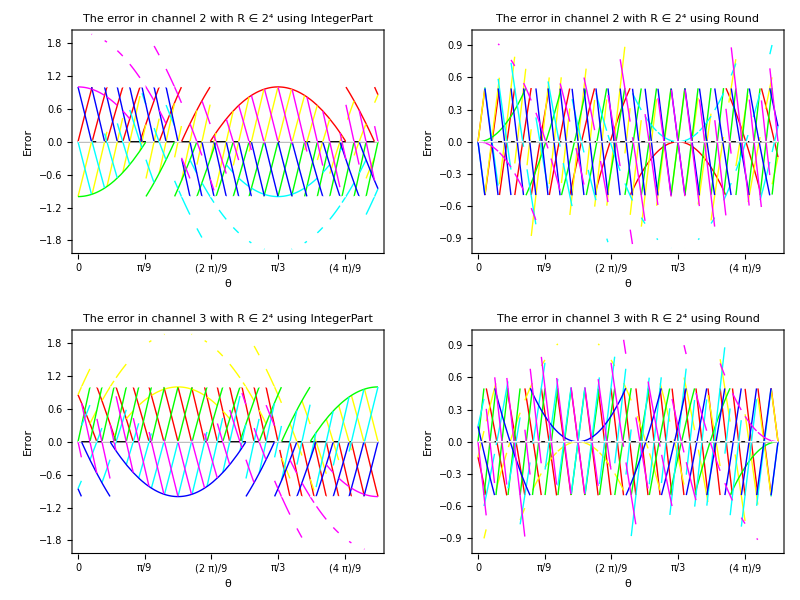

```mathematica
simpleErrorPlot[{0,Pi/2},rRErrorCube,4]
```

## Approximating fR

We are attempting to represent the matrix fR, which is the factored rotation, as an integer matrix with elements in the range -2^(n-2)< fR < 2^(n-2). We assume that n>3 for this reason.

```mathematica
approxSimplify=Function[{expr},Assuming[Element[m,Integers]&&m>0&&m≤ n&&Element[n,Integers]&&n>3&&Element[θ,Reals]&& θ≥ 0 && θ< Pi/6,FullSimplify[expr]]];
```

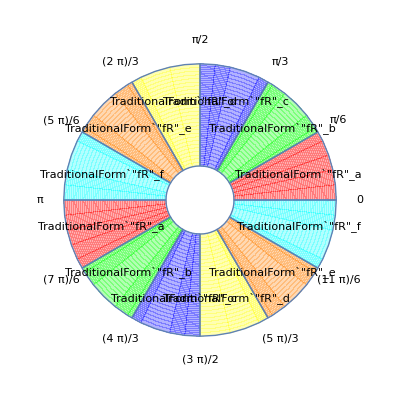
-Graphics-fR_a = (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
fR_b = (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
fR_c = (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
fR_d = (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
fR_e = (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))
fR_f = (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))

```mathematica
Row[{
partShow[Piecewise[{{Subscript["fR",a],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{Subscript["fR",b],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{Subscript["fR",c],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{Subscript["fR",d],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{Subscript["fR",e],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{Subscript["fR",f],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]],
Column[{
Row[{Subscript["fR",a]," = ",TraditionalForm[fR[θ][[1,1,1]]]}],
Row[{Subscript["fR",b]," = ",TraditionalForm[fR[θ][[1,2,1]]]}],
Row[{Subscript["fR",c]," = ",TraditionalForm[fR[θ][[1,3,1]]]}],
Row[{Subscript["fR",d]," = ",TraditionalForm[fR[θ][[1,4,1]]]}],
Row[{Subscript["fR",e]," = ",TraditionalForm[fR[θ][[1,5,1]]]}],
Row[{Subscript["fR",f]," = ",TraditionalForm[fR[θ][[1,6,1]]]}]}]}]
```

```mathematica
Row[{
partShow[Piecewise[{{Subscript["fR",a],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{Subscript["fR",b],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{Subscript["fR",c],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{Subscript["fR",d],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{Subscript["fR",e],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{Subscript["fR",f],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]],
Column[{
Row[{Subscript["fR",a]," = ",TraditionalForm[TrigToExp[fR[0 Pi/6 +δθ][[1,1,1]]]]}],
Row[{Subscript["fR",b]," = ",TraditionalForm[TrigToExp[fR[1 Pi/6 +δθ][[1,2,1]]]]}],
Row[{Subscript["fR",c]," = ",TraditionalForm[TrigToExp[fR[2 Pi/6 +δθ][[1,3,1]]]]}],
Row[{Subscript["fR",d]," = ",TraditionalForm[TrigToExp[fR[3 Pi/6 +δθ][[1,4,1]]]]}],
Row[{Subscript["fR",e]," = ",TraditionalForm[TrigToExp[fR[4 Pi/6 +δθ][[1,5,1]]]]}],
Row[{Subscript["fR",f]," = ",TraditionalForm[TrigToExp[fR[5 Pi/6 +δθ][[1,6,1]]]]}]}]}]
```

-Graphics-fR_a = (1 | 1 | 1
(ⅈ ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(-ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)) | 1 | (ⅈ ⅇ^((ⅈ π)/6-ⅈ δθ))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))
-(ⅇ^(-ⅈ δθ-(ⅈ π)/6)+ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)) | -(ⅈ (ⅇ^(-ⅈ δθ)-ⅇ^(ⅈ δθ)))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)) | 1)
fR_b = (1 | 1 | 1
1 | -(ⅇ^(-ⅈ δθ-(ⅈ π)/6)+ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)) | -(ⅈ (ⅇ^(-ⅈ δθ)-ⅇ^(ⅈ δθ)))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6))
(ⅈ ⅇ^((ⅈ π)/6-ⅈ δθ))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)) | (ⅈ ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(-ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)) | 1)
fR_c = (1 | 1 | 1
1 | (ⅈ ⅇ^((ⅈ π)/6-ⅈ δθ))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)) | (ⅈ ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(-ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))
-(ⅈ (ⅇ^(-ⅈ δθ)-ⅇ^(ⅈ δθ)))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)) | 1 | -(ⅇ^(-ⅈ δθ-(ⅈ π)/6)+ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)))
fR_d = (1 | 1 | 1
-(ⅇ^(-ⅈ δθ-(ⅈ π)/6)+ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)) | -(ⅈ (ⅇ^(-ⅈ δθ)-ⅇ^(ⅈ δθ)))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)) | 1
(ⅈ ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(-ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)) | 1 | (ⅈ ⅇ^((ⅈ π)/6-ⅈ δθ))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)))
fR_e = (1 | 1 | 1
(ⅈ ⅇ^((ⅈ π)/6-ⅈ δθ))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)) | (ⅈ ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(-ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)) | 1
1 | -(ⅇ^(-ⅈ δθ-(ⅈ π)/6)+ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)) | -(ⅈ (ⅇ^(-ⅈ δθ)-ⅇ^(ⅈ δθ)))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)))
fR_f = (1 | 1 | 1
-(ⅈ (ⅇ^(-ⅈ δθ)-ⅇ^(ⅈ δθ)))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6)) | 1 | -(ⅇ^(-ⅈ δθ-(ⅈ π)/6)+ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^((ⅈ π)/6-ⅈ δθ)+ⅇ^(ⅈ δθ-(ⅈ π)/6))
1 | (ⅈ ⅇ^((ⅈ π)/6-ⅈ δθ))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)) | (ⅈ ⅇ^(ⅈ δθ+(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ))-(ⅈ ⅇ^(-ⅈ δθ-(ⅈ π)/6))/(ⅇ^(-ⅈ δθ)+ⅇ^(ⅈ δθ)))

To evaluate the error we approximate fR as

```mathematica
approx["fR"]=Function[{θ,n},Evaluate[ApplyToPiecewise[approxSimplify[(scale["fR","qR"][θ,n] # )]&,qR[θ,n]]]];
ApplyToPiecewise[mForm,approx["fR"][θ,n]]
```

Piecewise[{{1 | 1 | 1
-2^2 - n Round[2^n - 2 sin(θ + π/6) sec(θ)] | 1 | 2^2 - n Round[√3 2^n - 3 tan(θ)] - 1/2
-2^2 - n Round[2^n - 2 cos(θ + π/6) sec(π/6 - θ)] | -2^2 - n Round[2^n - 2 sin(θ) sec(π/6 - θ)] | 1, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {1 | 1 | 1
1 | -2^2 - n Round[2^n - 2 cos(θ) csc(θ + π/6)] | 2^2 - n Round[2^n - 2 sin(π/6 - θ) csc(θ + π/6)]
-2^2 - n Round[2^n - 2 cos(θ + π/6) sec(π/6 - θ)] | -2^2 - n Round[2^n - 2 sin(θ) sec(π/6 - θ)] | 1, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {1 | 1 | 1
1 | -2^2 - n Round[2^n - 2 cos(θ) csc(θ + π/6)] | 2^2 - n Round[2^n - 2 sin(π/6 - θ) csc(θ + π/6)]
2^2 - n Round[2^n - 2 cos(θ + π/6) csc(θ)] | 1 | -2^2 - n Round[2^n - 3 (√3 cot(θ) + 1)], π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {1 | 1 | 1
2^2 - n Round[2^n - 2 sin(θ + π/6) csc(π/6 - θ)] | -2^2 - n Round[2^n - 2 cos(θ) csc(π/6 - θ)] | 1
2^2 - n Round[2^n - 2 cos(θ + π/6) csc(θ)] | 1 | -2^2 - n Round[2^n - 3 (√3 cot(θ) + 1)], π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {1 | 1 | 1
2^2 - n Round[2^n - 2 sin(θ + π/6) csc(π/6 - θ)] | -2^2 - n Round[2^n - 2 cos(θ) csc(π/6 - θ)] | 1
1 | 2^2 - n Round[2^n - 2 sin(θ) sec(θ + π/6)] | -2^2 - n Round[2^n - 2 cos(π/6 - θ) sec(θ + π/6)], (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {1 | 1 | 1
-2^2 - n Round[2^n - 2 sin(θ + π/6) sec(θ)] | 1 | 2^2 - n Round[√3 2^n - 3 tan(θ)] - 1/2
1 | 2^2 - n Round[2^n - 2 sin(θ) sec(θ + π/6)] | -2^2 - n Round[2^n - 2 cos(π/6 - θ) sec(θ + π/6)], (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

the error is then the difference

```mathematica
error2Bit["fR"]=Function[{θ,n},Evaluate[ApplyToPiecewise[approxSimplify[(# (2^n ))]&,PiecewiseExpand[ApplyToPiecewise[(scale["fR","qR"][θ,n] # )&,qR[θ,n]]-fR[θ]]]]];
ApplyToPiecewise[mForm,error2Bit["fR"][θ,n]];
```

```mathematica
ApplyToPiecewise[mForm,error2Bit["fR"][θ,n]]
```

Piecewise[{{0 | 0 | 0
0 | 2^n cos(θ) csc(θ + π/6) - 4 Round[2^n - 2 cos(θ) csc(θ + π/6)] | 4 Round[2^n - 2 sin(π/6 - θ) csc(θ + π/6)] - 2^n sin(π/6 - θ) csc(θ + π/6)
4 Round[2^n - 2 cos(θ + π/6) csc(θ)] - 2^n cos(θ + π/6) csc(θ) | 0 | √3 2^n - 1 cot(θ) - 4 Round[√3 2^n - 3 cot(θ)], π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {0 | 0 | 0
0 | 2^n cos(θ) csc(θ + π/6) - 4 Round[2^n - 2 cos(θ) csc(θ + π/6)] | 4 Round[2^n - 2 sin(π/6 - θ) csc(θ + π/6)] - 2^n sin(π/6 - θ) csc(θ + π/6)
2^n cos(θ + π/6) sec(π/6 - θ) - 4 Round[2^n - 2 cos(θ + π/6) sec(π/6 - θ)] | 2^n sin(θ) sec(π/6 - θ) - 4 Round[2^n - 2 sin(θ) sec(π/6 - θ)] | 0, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {0 | 0 | 0
4 Round[2^n - 2 sin(θ + π/6) csc(π/6 - θ)] - 2^n sin(θ + π/6) csc(π/6 - θ) | 2^n cos(θ) csc(π/6 - θ) - 4 Round[2^n - 2 cos(θ) csc(π/6 - θ)] | 0
0 | 4 Round[2^n - 2 sin(θ) sec(θ + π/6)] - 2^n sin(θ) sec(θ + π/6) | 2^n cos(π/6 - θ) sec(θ + π/6) - 4 Round[2^n - 2 cos(π/6 - θ) sec(θ + π/6)], (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {0 | 0 | 0
4 Round[2^n - 2 sin(θ + π/6) csc(π/6 - θ)] - 2^n sin(θ + π/6) csc(π/6 - θ) | 2^n cos(θ) csc(π/6 - θ) - 4 Round[2^n - 2 cos(θ) csc(π/6 - θ)] | 0
4 Round[2^n - 2 cos(θ + π/6) csc(θ)] - 2^n cos(θ + π/6) csc(θ) | 0 | √3 2^n - 1 cot(θ) - 4 Round[√3 2^n - 3 cot(θ)], π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {0 | 0 | 0
√3 2^n - 1 tan(θ) - 4 Round[√3 2^n - 3 tan(θ)] | 0 | 4 Round[√3 2^n - 3 tan(θ)] - √3 2^n - 1 tan(θ)
0 | 4 Round[2^n - 2 sin(θ) sec(θ + π/6)] - 2^n sin(θ) sec(θ + π/6) | 2^n cos(π/6 - θ) sec(θ + π/6) - 4 Round[2^n - 2 cos(π/6 - θ) sec(θ + π/6)], (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0 | 0 | 0
√3 2^n - 1 tan(θ) - 4 Round[√3 2^n - 3 tan(θ)] | 0 | 4 Round[√3 2^n - 3 tan(θ)] - √3 2^n - 1 tan(θ)
2^n cos(θ + π/6) sec(π/6 - θ) - 4 Round[2^n - 2 cos(θ + π/6) sec(π/6 - θ)] | 2^n sin(θ) sec(π/6 - θ) - 4 Round[2^n - 2 sin(θ) sec(π/6 - θ)] | 0, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {0, True}}]

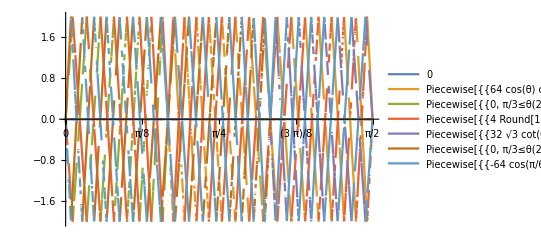

```mathematica
Plot[Evaluate[Union[Flatten[Table[ApplyToPiecewise[(#[[i,j]])&,error2Bit["fR"][θ,6]],{i,1,3},{j,1,3}]]]],{θ,0,Pi/2},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All}]
```

```mathematica
nonZeroErrors=Function[{θ,n,round},Evaluate[ApplyToPiecewise[ (((#)/. 0->Sequence[])/. List[]-> List[0,0])&,error2Bit["fR"][θ,n]]]];
ApplyToPiecewise[ MatrixForm,nonZeroErrors[θ,n,Round]]
```

Piecewise[{{(0 | 0
2^n Cos[θ] Csc[π/6+θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6+θ]] | 4 Round[2^(-2+n) Csc[π/6+θ] Sin[π/6-θ]]-2^n Csc[π/6+θ] Sin[π/6-θ]
-2^n Cos[π/6+θ] Csc[θ]+4 Round[2^(-2+n) Cos[π/6+θ] Csc[θ]] | 2^(-1+n) √3 Cot[θ]-4 Round[2^(-3+n) √3 Cot[θ]]), π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {(0 | 0
2^n Cos[θ] Csc[π/6+θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6+θ]] | 4 Round[2^(-2+n) Csc[π/6+θ] Sin[π/6-θ]]-2^n Csc[π/6+θ] Sin[π/6-θ]
-4 Round[2^(-2+n) Cos[π/6+θ] Sec[π/6-θ]]+2^n Cos[π/6+θ] Sec[π/6-θ] | -4 Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+2^n Sec[π/6-θ] Sin[θ]), π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {(0 | 0
4 Round[2^(-2+n) Csc[π/6-θ] Sin[π/6+θ]]-2^n Csc[π/6-θ] Sin[π/6+θ] | 2^n Cos[θ] Csc[π/6-θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6-θ]]
4 Round[2^(-2+n) Sec[π/6+θ] Sin[θ]]-2^n Sec[π/6+θ] Sin[θ] | -4 Round[2^(-2+n) Cos[π/6-θ] Sec[π/6+θ]]+2^n Cos[π/6-θ] Sec[π/6+θ]), (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {(0 | 0
4 Round[2^(-2+n) Csc[π/6-θ] Sin[π/6+θ]]-2^n Csc[π/6-θ] Sin[π/6+θ] | 2^n Cos[θ] Csc[π/6-θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6-θ]]
-2^n Cos[π/6+θ] Csc[θ]+4 Round[2^(-2+n) Cos[π/6+θ] Csc[θ]] | 2^(-1+n) √3 Cot[θ]-4 Round[2^(-3+n) √3 Cot[θ]]), π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {(0 | 0
-4 Round[2^(-3+n) √3 Tan[θ]]+2^(-1+n) √3 Tan[θ] | 4 Round[2^(-3+n) √3 Tan[θ]]-2^(-1+n) √3 Tan[θ]
4 Round[2^(-2+n) Sec[π/6+θ] Sin[θ]]-2^n Sec[π/6+θ] Sin[θ] | -4 Round[2^(-2+n) Cos[π/6-θ] Sec[π/6+θ]]+2^n Cos[π/6-θ] Sec[π/6+θ]), (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {(0 | 0
-4 Round[2^(-3+n) √3 Tan[θ]]+2^(-1+n) √3 Tan[θ] | 4 Round[2^(-3+n) √3 Tan[θ]]-2^(-1+n) √3 Tan[θ]
-4 Round[2^(-2+n) Cos[π/6+θ] Sec[π/6-θ]]+2^n Cos[π/6+θ] Sec[π/6-θ] | -4 Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+2^n Sec[π/6-θ] Sin[θ]), 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {0, True}}]

Put the Piecewise function in the correct order

```mathematica
nonZeroErrors=Function[{θ,n,round},Evaluate[Piecewise[Evaluate[Sort[nonZeroErrors[θ,n,Round][[1]],#1[[2,1,1]]<#2[[2,1,1]]&]]]]];
ApplyToPiecewise[ MatrixForm,nonZeroErrors[θ,n,Round]]
```

Piecewise[{{(0 | 0
-4 Round[2^(-3+n) √3 Tan[θ]]+2^(-1+n) √3 Tan[θ] | 4 Round[2^(-3+n) √3 Tan[θ]]-2^(-1+n) √3 Tan[θ]
-4 Round[2^(-2+n) Cos[π/6+θ] Sec[π/6-θ]]+2^n Cos[π/6+θ] Sec[π/6-θ] | -4 Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+2^n Sec[π/6-θ] Sin[θ]), 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {(0 | 0
2^n Cos[θ] Csc[π/6+θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6+θ]] | 4 Round[2^(-2+n) Csc[π/6+θ] Sin[π/6-θ]]-2^n Csc[π/6+θ] Sin[π/6-θ]
-4 Round[2^(-2+n) Cos[π/6+θ] Sec[π/6-θ]]+2^n Cos[π/6+θ] Sec[π/6-θ] | -4 Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+2^n Sec[π/6-θ] Sin[θ]), π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {(0 | 0
2^n Cos[θ] Csc[π/6+θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6+θ]] | 4 Round[2^(-2+n) Csc[π/6+θ] Sin[π/6-θ]]-2^n Csc[π/6+θ] Sin[π/6-θ]
-2^n Cos[π/6+θ] Csc[θ]+4 Round[2^(-2+n) Cos[π/6+θ] Csc[θ]] | 2^(-1+n) √3 Cot[θ]-4 Round[2^(-3+n) √3 Cot[θ]]), π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {(0 | 0
4 Round[2^(-2+n) Csc[π/6-θ] Sin[π/6+θ]]-2^n Csc[π/6-θ] Sin[π/6+θ] | 2^n Cos[θ] Csc[π/6-θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6-θ]]
-2^n Cos[π/6+θ] Csc[θ]+4 Round[2^(-2+n) Cos[π/6+θ] Csc[θ]] | 2^(-1+n) √3 Cot[θ]-4 Round[2^(-3+n) √3 Cot[θ]]), π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {(0 | 0
4 Round[2^(-2+n) Csc[π/6-θ] Sin[π/6+θ]]-2^n Csc[π/6-θ] Sin[π/6+θ] | 2^n Cos[θ] Csc[π/6-θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6-θ]]
4 Round[2^(-2+n) Sec[π/6+θ] Sin[θ]]-2^n Sec[π/6+θ] Sin[θ] | -4 Round[2^(-2+n) Cos[π/6-θ] Sec[π/6+θ]]+2^n Cos[π/6-θ] Sec[π/6+θ]), (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {(0 | 0
-4 Round[2^(-3+n) √3 Tan[θ]]+2^(-1+n) √3 Tan[θ] | 4 Round[2^(-3+n) √3 Tan[θ]]-2^(-1+n) √3 Tan[θ]
4 Round[2^(-2+n) Sec[π/6+θ] Sin[θ]]-2^n Sec[π/6+θ] Sin[θ] | -4 Round[2^(-2+n) Cos[π/6-θ] Sec[π/6+θ]]+2^n Cos[π/6-θ] Sec[π/6+θ]), (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

```mathematica
Definition[nonZeroErrors]
```

nonZeroErrors=Function[{θ,n,round},Piecewise[{{{{0,0},{-4 Round[2^(-3+n) √3 Tan[θ]]+2^(-1+n) √3 Tan[θ],4 Round[2^(-3+n) √3 Tan[θ]]-2^(-1+n) √3 Tan[θ]},{-4 Round[2^(-2+n) Cos[π/6+θ] Sec[π/6-θ]]+2^n Cos[π/6+θ] Sec[π/6-θ],-4 Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+2^n Sec[π/6-θ] Sin[θ]}}, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {{{0,0},{2^n Cos[θ] Csc[π/6+θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6+θ]],4 Round[2^(-2+n) Csc[π/6+θ] Sin[π/6-θ]]-2^n Csc[π/6+θ] Sin[π/6-θ]},{-4 Round[2^(-2+n) Cos[π/6+θ] Sec[π/6-θ]]+2^n Cos[π/6+θ] Sec[π/6-θ],-4 Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+2^n Sec[π/6-θ] Sin[θ]}}, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {{{0,0},{2^n Cos[θ] Csc[π/6+θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6+θ]],4 Round[2^(-2+n) Csc[π/6+θ] Sin[π/6-θ]]-2^n Csc[π/6+θ] Sin[π/6-θ]},{-2^n Cos[π/6+θ] Csc[θ]+4 Round[2^(-2+n) Cos[π/6+θ] Csc[θ]],2^(-1+n) √3 Cot[θ]-4 Round[2^(-3+n) √3 Cot[θ]]}}, π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {{{0,0},{4 Round[2^(-2+n) Csc[π/6-θ] Sin[π/6+θ]]-2^n Csc[π/6-θ] Sin[π/6+θ],2^n Cos[θ] Csc[π/6-θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6-θ]]},{-2^n Cos[π/6+θ] Csc[θ]+4 Round[2^(-2+n) Cos[π/6+θ] Csc[θ]],2^(-1+n) √3 Cot[θ]-4 Round[2^(-3+n) √3 Cot[θ]]}}, π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {{{0,0},{4 Round[2^(-2+n) Csc[π/6-θ] Sin[π/6+θ]]-2^n Csc[π/6-θ] Sin[π/6+θ],2^n Cos[θ] Csc[π/6-θ]-4 Round[2^(-2+n) Cos[θ] Csc[π/6-θ]]},{4 Round[2^(-2+n) Sec[π/6+θ] Sin[θ]]-2^n Sec[π/6+θ] Sin[θ],-4 Round[2^(-2+n) Cos[π/6-θ] Sec[π/6+θ]]+2^n Cos[π/6-θ] Sec[π/6+θ]}}, (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {{{0,0},{-4 Round[2^(-3+n) √3 Tan[θ]]+2^(-1+n) √3 Tan[θ],4 Round[2^(-3+n) √3 Tan[θ]]-2^(-1+n) √3 Tan[θ]},{4 Round[2^(-2+n) Sec[π/6+θ] Sin[θ]]-2^n Sec[π/6+θ] Sin[θ],-4 Round[2^(-2+n) Cos[π/6-θ] Sec[π/6+θ]]+2^n Cos[π/6-θ] Sec[π/6+θ]}}, (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]]

Check that there are only 4 distinct functions which repeat every Pi/6 intival

```mathematica
distinctErrorFunc=Function[{θ,n,round},Evaluate[nonZeroErrors[θ,n,round][[1,1,1,{2,3}]]/. θ -> Mod[θ,Pi/6]]];
```

```mathematica
Definition[distinctErrorFunc]
```

distinctErrorFunc=Function[{θ,n,round},{{-4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]+2^(-1+n) √3 Tan[Mod[θ,π/6]],4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]-2^(-1+n) √3 Tan[Mod[θ,π/6]]},{-4 Round[2^(-2+n) Cos[π/6+Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]]]+2^n Cos[π/6+Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]],-4 Round[2^(-2+n) Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]]+2^n Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]}}]

```mathematica
distinctErrorFunc=Function[{θ,n,round},{{-4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]+2^(-1+n) √3 Tan[Mod[θ,π/6]],4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]-2^(-1+n) √3 Tan[Mod[θ,π/6]]},{-4 Round[2^(-2+n) Cos[π/6+Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]]]+2^n Cos[π/6+Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]],-4 Round[2^(-2+n) Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]]+2^n Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]}}]
```

Function[{θ,n,round},{{-4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]+2^(-1+n) √3 Tan[Mod[θ,π/6]],4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]-2^(-1+n) √3 Tan[Mod[θ,π/6]]},{-4 Round[2^(-2+n) Cos[π/6+Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]]]+2^n Cos[π/6+Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]],-4 Round[2^(-2+n) Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]]+2^n Sec[π/6-Mod[θ,π/6]] Sin[Mod[θ,π/6]]}}]

Using the following Identity

```mathematica
FullSimplify[Cos[π/6+θ] Sec[π/6-θ]==1-Sec[π/6-θ] Sin[θ]]
```

```mathematica
2^n (1-sin(θπ/6) sec(π/6-θπ/6))-4 Round[2^(n-2) (1-sin(θπ/6) sec(π/6-θπ/6))]
4 Round[2^(n-2) sin(θπ/6) sec(π/6-θπ/6)]+2^n (1-sin(θπ/6) sec(π/6-θπ/6))-4 2^(n-2)
-2^n (sin(θπ/6) sec(π/6-θπ/6))+4 Round[2^(n-2) sin(θπ/6) sec(π/6-θπ/6)]
```

We find

```mathematica
distinctErrorFunc=Function[{θ,n,round},{{-4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]+2^(-1+n) √3 Tan[Mod[θ,π/6]],4 Round[2^(-3+n) √3 Tan[Mod[θ,π/6]]]-2^(-1+n) √3 Tan[Mod[θ,π/6]]},{4 Round[2^(-2+n) Sin[Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]]]-2^n Sin[Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]],-4 Round[2^(-2+n) Sin[Mod[θ,π/6]]Sec[π/6-Mod[θ,π/6]] ]+2^n Sin[Mod[θ,π/6]] Sec[π/6-Mod[θ,π/6]] }}];
```

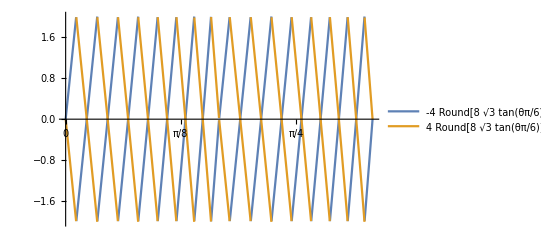
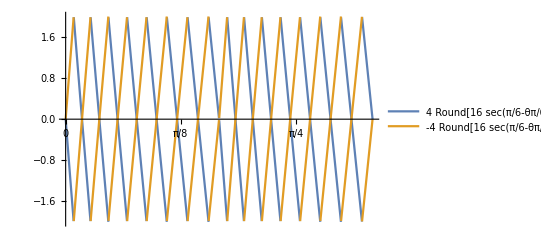
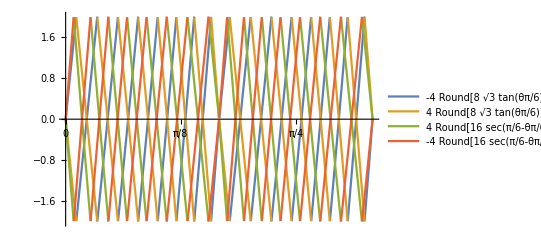

```mathematica
Column[{Plot[Evaluate[distinctErrorFunc[θ,6,Round][[1]]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All}],
Plot[Evaluate[distinctErrorFunc[θ,6,Round][[2]]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All}],
Plot[Evaluate[distinctErrorFunc[θ,6,Round]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All}]}]
```

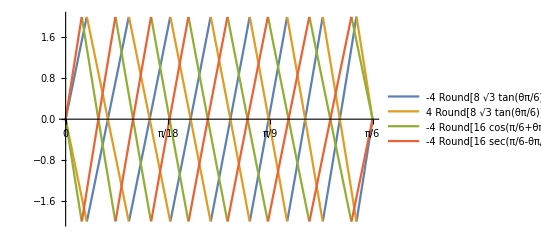

```mathematica
Plot[Evaluate[Flatten[distinctErrorFunc[θ,6,Round]]],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"]
```

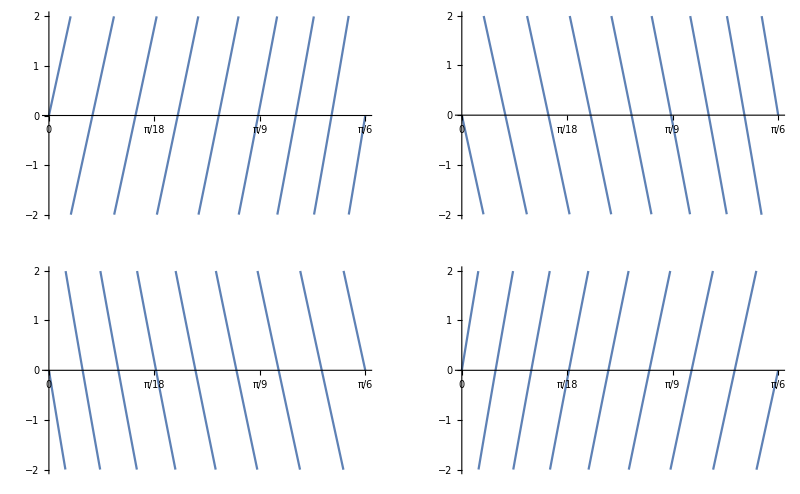

```mathematica
GraphicsGrid[{{Plot[Evaluate[distinctErrorFunc[θ,6,Round][[1,1]]],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"],Plot[Evaluate[distinctErrorFunc[θ,6,Round][[1,2]]],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"]},
{Plot[Evaluate[distinctErrorFunc[θ,6,Round][[2,1]]],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"],Plot[Evaluate[distinctErrorFunc[θ,6,Round][[2,2]]],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"]}}]
```

There are infact only two functions

#### Points of intersection

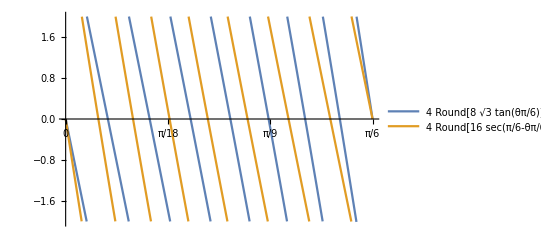

```mathematica
Block[{n=6},Plot[Evaluate[{distinctErrorFunc[θ,n,Round][[1,2]],distinctErrorFunc[θ,n,Round][[2,1]]}],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"]]
```

These functions are parallell and never intersect so we solve

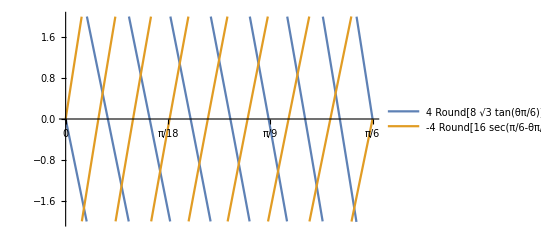

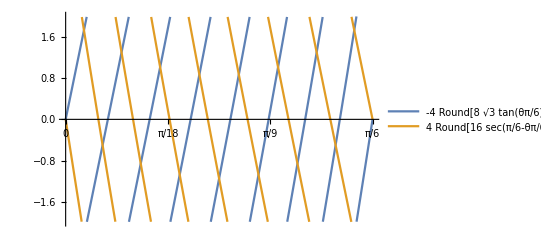

```mathematica
Block[{n=6},Plot[Evaluate[{distinctErrorFunc[θ,n,Round][[1,2]],-distinctErrorFunc[θ,n,Round][[2,1]]}],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"]]
Block[{n=6},Plot[Evaluate[{-distinctErrorFunc[θ,n,Round][[1,2]],distinctErrorFunc[θ,n,Round][[2,1]]}],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"]]
```

The Points of intersection are found by solving

```mathematica
Assuming[Element[n,Integers]&&n>3&&Element[θ,Reals]&& θ≥ 0 && θ< Pi/6,FullSimplify[α distinctErrorFunc[θ,n,Round][[1,2]]==-β distinctErrorFunc[θ,n,Round][[2,1]]]]
```

8 β Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+8 α Round[2^(-3+n) √3 Tan[θ]]==2^n (2 β Sec[π/6-θ] Sin[θ]+√3 α Tan[θ])

```mathematica
Manipulate[
Plot[{2^(n-3) (2 β Sec[π/6-θ] Sin[θ]+√3 α Tan[θ]), β Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+ α Round[2^(-3+n) √3 Tan[θ]]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],{{α,1},0,1},{{β,1},0,1},{{n,6},3,8,1}]
```

We have to assume that α=β so the following trick can be used.

```mathematica
Assuming[Element[n,Integers]&&n>3&&Element[θ,Reals]&& θ≥ 0 && θ< Pi/6,FullSimplify[distinctErrorFunc[θ,n,Round][[1,2]]==-distinctErrorFunc[θ,n,Round][[2,1]]]]
```

8 (Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+Round[2^(-3+n) √3 Tan[θ]])==2^n (√3+2 Cos[θ] Sec[π/6-θ]) Tan[θ]

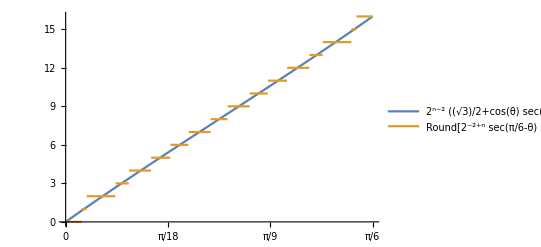

```mathematica
Block[{n=6},
Plot[{2^(n-2) (√3/2+ Cos[θ] Sec[π/6-θ]) Tan[θ],Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]+Round[2^(-3+n) √3 Tan[θ]]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"]]
```

The rounded part takes all integer values between 0 and 2^(n-2)

Essentially we are discretising  ((√3)/2+ Cos[θ] Sec[π/6-θ]) Tan[θ] into steps of 1/2^(n-2).
If we find the inverse function we can plug in integers and generate a table of theta values.

```mathematica
θ/.Assuming[Element[m,Integers]&&m>0&&m≤ n&&Element[n,Integers]&&n>3&&Element[θ,Reals]&& θ≥ 0 && θ< Pi/6&&y≥0&&y≤1,Simplify[Solve[y==  (√3/2+ Cos[θ] Sec[π/6-θ]) Tan[θ],θ]/.C[1]->0]]
```

{ArcTan[2 √3 (-7+2 y),(-7+2 y) (-7+2 y+√(49-4 y+4 y^2))],ArcTan[(-7+2 y+√(49-4 y+4 y^2))/(2 √3)],π-ArcTan[(7-2 y+√(49-4 y+4 y^2))/(2 √3)],-ArcTan[(7-2 y+√(49-4 y+4 y^2))/(2 √3)]}

Apply 0 < θ <= π/6 selecting the correct inverse functions

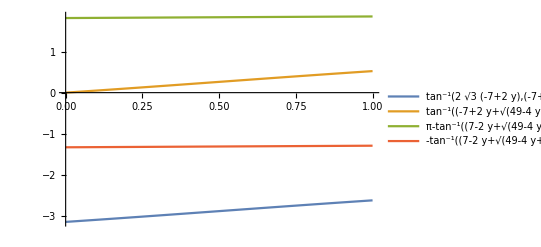

```mathematica
Plot[{ArcTan[2 √3 (-7+2 y),(-7+2 y) (-7+2 y+√(49-4 y+4 y^2))],ArcTan[(-7+2 y+√(49-4 y+4 y^2))/(2 √3)],π-ArcTan[(7-2 y+√(49-4 y+4 y^2))/(2 √3)],-ArcTan[(7-2 y+√(49-4 y+4 y^2))/(2 √3)]},{y,0,1},PlotLegends->"Expressions"]
```

```mathematica
thetaIntersection=Function[{m,n},Evaluate[ArcTan[(-7+2 y+√(49-4 y+4 y^2))/(2 √3)]/.{y-> m 2^(2-n)}]];
```

```mathematica
thetaIntersections=Function[{n}, Table[thetaIntersection[i,n],{i,0,2^(n-2)}]];
```

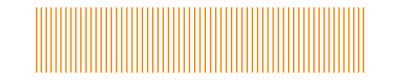

```mathematica
Graphics[Flatten[Map[{Orange,Line[{{#,0},{#,Pi/(16 6)}}]}&,thetaIntersections[8]]]]
```

#### Locating the Minima for each channel

```mathematica
discCond=Map[approxSimplify[#==0]&,distinctErrorFunc[θ,n,Round][[All,2]],{1}]
```

{8 Round[2^(-3+n) √3 Tan[θ]]==2^n √3 Tan[θ],4 Round[2^(-2+n) Sec[π/6-θ] Sin[θ]]==2^n Sec[π/6-θ] Sin[θ]}

If we allow a coordinate transform then there is only one function

```mathematica
disc=Function[{θ,n},{2^(-3+n)(-1+2 Cos[π/6+θ] Sec[π/6-θ]),2^(-3+n) √3 Tan[θ]}];
```

proof

```mathematica
FullSimplify[disc[θ,3][[1]]==disc[π/6-θ,3][[2]]]
```

True

```mathematica
disc=Function[{θ,n},{2^(-3+n) √3 Tan[π/6-θ],2^(-3+n) √3 Tan[θ]}];
```

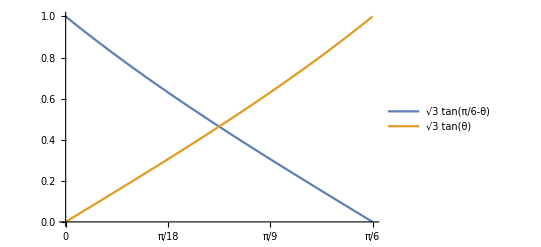

```mathematica
Plot[Evaluate[disc[θ,3]],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotLegends->"Expressions"]
```

Get The inverse functions for θ

```mathematica
Clear[θ,theta,n]
(θ==theta)/.Map[(Assuming[Element[θ,Reals]&& θ≥ 0 && θ< Pi/6&&y≥0&&y≤1,Simplify[Solve[y== #,theta]/.C[1]->0]])&,disc[theta,3]]
```

{{θ==ArcTan[-3-y,√3 (-1+y)],θ==-ArcTan[(√3 (-1+y))/(3+y)]},{θ==ArcTan[y/(√3)]}}

Apply 0 < θ <= π/6 selecting the inverse functions

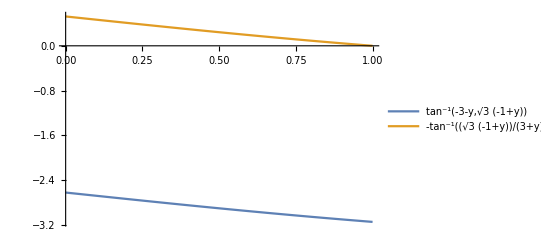

```mathematica
Plot[{ArcTan[-3-y,√3 (-1+y)],-ArcTan[(√3 (-1+y))/(3+y)]},{y,0,1},PlotLegends->"Expressions"]
```

So for a discrete value y ∈ {0 , 2^(3-n), .. , 1} we can now find the corresponding value of theta. Where y

```mathematica
thetaFun=Function[{y},{ArcTan[(√3 (1-y))/(3+y)],ArcTan[y/(√3)]},Listable];
```

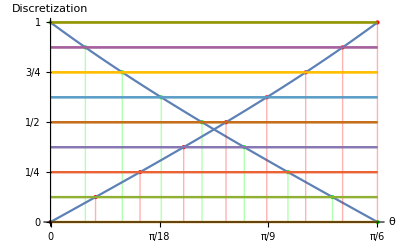

```mathematica
Clear[dev,fun,thetaFun,pts];
Block[{n=6},
dev=Table[m 2^(3-n),{m,0,2^(n-3)}];
fun=(Flatten[{#1,dev}]&)/@disc[θ,3];thetaFun=Function[{y},{-ArcTan[(√3 (y-1))/(3+y)],ArcTan[y/(√3)]},Listable];pts=Transpose/@Thread[{Transpose[thetaFun[dev]],{dev,dev}}];

lines=Map[{Green,Line[{{#[[1]],0},{#[[1]],#[[2]]}}],Red,Line[{{#[[2]],0},{#[[2]],#[[2]]}}]}&,pts];GraphicsColumn[{GraphicsRow[{Show[{ListPlot[pts⟦1⟧,PlotStyle->{Green,PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],All},Filling->Axis],Plot[Evaluate[fun⟦1⟧],{θ,0,π/6}]}],Show[{ListPlot[pts⟦2⟧,PlotStyle->{Red,PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],All},Filling->Axis],Plot[Evaluate[fun⟦2⟧],{θ,0,π/6}]}]}],
Show[{ListPlot[pts⟦1⟧,PlotStyle->{Green,PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],dev},Filling->Axis,AxesLabel->{"θ","Discretization"}],Plot[Evaluate[fun⟦1⟧],{θ,0,π/6}],ListPlot[pts⟦2⟧,PlotStyle->{Red,PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],All},Filling->Axis],Plot[Evaluate[fun⟦2⟧],{θ,0,π/6}]}]}]
]
```

For a given value of n there are 2^(n - 3) + 1 zeros between 0 and Pi/6. 
The channel one and chanel two zeros are related by zeros[2] = Pi/6 - zeros[1]

```mathematica
thetaMin = Function[{m, n}, Evaluate[approxSimplify[{-ArcTan[(Sqrt[3]*(ya - 1))/(3 + ya)], ArcTan[yb/Sqrt[3]]} /. 
      {ya -> (2^(n - 3) - m)/2^(n - 3), yb -> m/2^(n - 3)}]]];
thetaMax = Function[{m, n}, Evaluate[approxSimplify[{-ArcTan[(Sqrt[3]*(ya - 1))/(3 + ya)], ArcTan[yb/Sqrt[3]]} /. 
       {ya -> (2^(n - 3) - m - 1/2)/2^(n - 3), yb -> (m + 1/2)/2^(n - 3)} /. y -> (m + 1/2)/2^(n - 3)]]];
```

```mathematica
Definition[thetaMin]
Definition[thetaMax]
```

thetaMin=Function[{m,n},{ArcTan[(2 √3 m)/(2^n-2 m)],ArcTan[(2^(3-n) m)/(√3)]}]

thetaMax=Function[{m,n},{ArcTan[(√3 (1+2 m))/(-1+2^n-2 m)],ArcTan[(2^(2-n) (1+2 m))/(√3)]}]

```mathematica
thetaMins=Function[{n}, Table[thetaMin[i,n],{i,0,2^(n-3)}]];
thetaMaxs=Function[{n}, Table[thetaMax[i,n],{i,0,2^(n-3)}]];
thetaIntersections
```

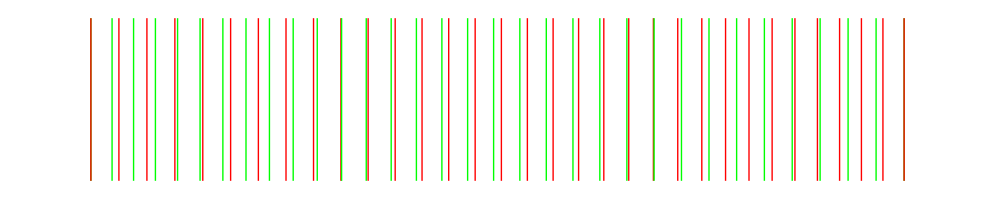

```mathematica
Graphics[Flatten[Map[{Green,Line[{{#[[1]],0},{#[[1]],Pi/(16 6)}}],Red,Line[{{#[[2]],0},{#[[2]],Pi/(16 6)}}]}&,thetaMins[8]]]]
```

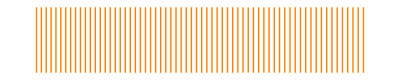

```mathematica
Graphics[Flatten[Map[{Orange,Line[{{#,0},{#,Pi/(16 6)}}]}&,thetaIntersections[8]]]]
```

The maximum points are approximately half way between minimum points.

```mathematica
Clear[plt,maxradius]
maxradius={};
Do[
minThetaPts=thetaMins[n];
maxThetaPts=thetaMaxs[n];
maxThetaPtsApprox=(Most[minThetaPts]+Rest[minThetaPts])/2;
LAErr[n]=maxThetaPtsApprox-Most[maxThetaPts];
plt[n]=ListPlot[N[LAErr[n]],AspectRatio->1];
radius[n]=Map[Sqrt[#[[1]]^2+#[[2]]^2]&,LAErr[n]];
AppendTo[maxradius,{n,Max[N[radius[n]]]}];
,{n,3,8}]
```

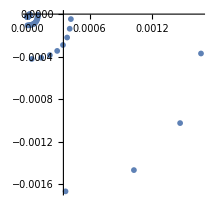

```mathematica
Block[{nn=5},
Show[Table[plt[i],{i,nn,8}],PlotRange->{{0,Max[PlotRange[plt[nn]]]},{0,Min[PlotRange[plt[nn]]]}}]
]
```

```mathematica
Definition[maxradius]
```

maxradius={{3,0.0272031},{4,0.00692566},{5,0.00178846},{6,0.000451428},{7,0.000113139},{8,0.0000283027},{9,7.07679×10^-6},{10,1.76927×10^-6},{11,4.42321×10^-7},{12,1.10581×10^-7},{13,2.76451×10^-8},{14,6.91129×10^-9},{15,1.72782×10^-9},{16,4.31956×10^-10},{17,1.07989×10^-10},{18,2.69973×10^-11},{19,6.74942×10^-12},{20,1.68744×10^-12},{21,4.21947×10^-13},{22,1.05582×10^-13}}

1.80502 ⅇ^(-1.3846 x)

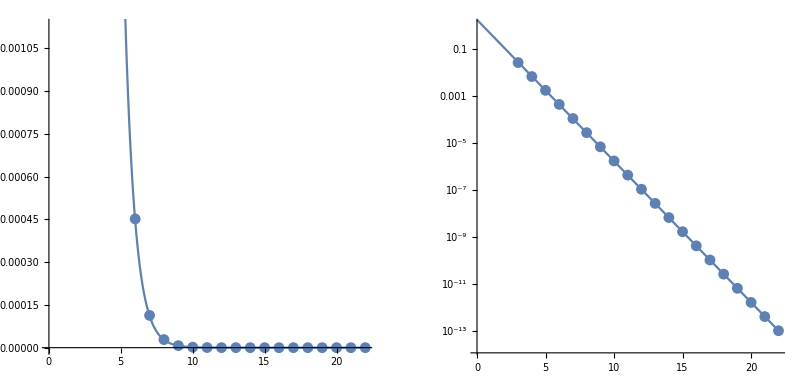

```mathematica
maxRadiusLog=Map[{#[[1]],Log[#[[2]]]}&,maxradius];
fit=FullSimplify[Exp[Evaluate[Fit[maxRadiusLog,{1,x},x]]]]
GraphicsRow[{Show[{ListPlot[maxradius,AspectRatio->1],Plot[fit,{x,0,22}]}],Show[{ListLogPlot[maxradius,AspectRatio->1],Plot[Evaluate[Log[fit]],{x,0,22}]}]}]
```

#### The channel mins and maxs are simply related.

```mathematica
thetaMins=Function[{n}, pts=Table[ArcTan[(i/(2^(n-3)))/(√3)],{i,0,2^(n-3)}];{pts,Reverse[ArcTan[1/(√3)]-pts]}];
```

Proof

```mathematica
pts=Transpose[Table[thetaFun[i/(2^(6-3))],{i,0,2^(6-3)}]]
N[ArcTan[1/(√3)]-pts[[1]]]==N[pts[[2]]]
```

{{π/6,ArcTan[(7 √3)/25],ArcTan[(3 √3)/13],ArcTan[5/(9 √3)],ArcTan[(√3)/7],ArcTan[(3 √3)/29],ArcTan[1/(5 √3)],ArcTan[(√3)/31],0},{0,ArcTan[1/(8 √3)],ArcTan[1/(4 √3)],ArcTan[(√3)/8],ArcTan[1/(2 √3)],ArcTan[5/(8 √3)],ArcTan[(√3)/4],ArcTan[7/(8 √3)],π/6}}

True

#### The Points

```mathematica
pointMins=Function[{n},Block[{θ},Transpose[Table[θ=thetaMin[i,n];{{θ[[1]],0},{θ[[2]],0}},{i,0,2^(n-3)}]]]];
pointMaxs=Function[{n},Block[{θ},Transpose[Table[θ=thetaMax[i,n];{{θ[[1]],2},{θ[[2]],2}},{i,0,2^(n-3)}]]]];
pointIntersections=Function[{n},Block[{θ},Transpose[Table[θ=thetaIntersection[i,n];{{θ,Max[distinctErrorFunc[θ,n,Round][[1]]]},{θ,Max[distinctErrorFunc[θ,n,Round][[2]]]}},{i,0,2^(n-2)}]]]];
```

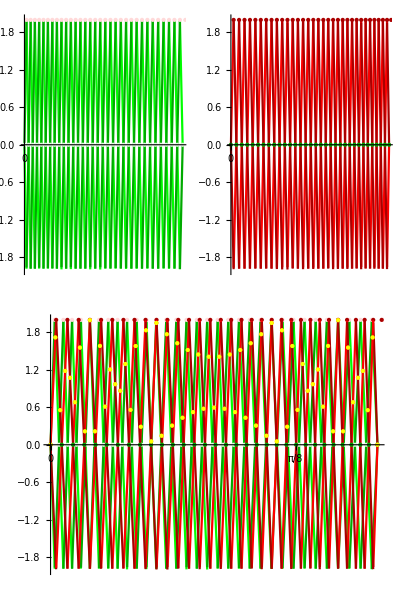

```mathematica
Clear[θ]
colorMins={LightGreen,Darker[Green]};
colorMaxs={LightRed,Darker[Red]};
colorInter={Orange,Yellow};
Block[{n=8},
pntMins=pointMins[n];
pntMaxs=pointMaxs[n];
pntInter=pointIntersections[n];
plt1=Show[{Plot[Evaluate[distinctErrorFunc[θ,n,Round][[2]]],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/2,12],All},PlotStyle->{Green,Darker[Green]}],
ListPlot[pntMaxs[[1]],PlotStyle->{colorMaxs[[1]],PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[pntMins[[1]],PlotStyle->{colorMins[[1]],PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],All}]}];
plt2=Show[{Plot[Evaluate[distinctErrorFunc[θ,n,Round][[1]]],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/2,12],All},PlotStyle->{Red,Darker[Red]}],
ListPlot[pntMaxs[[2]],PlotStyle->{colorMaxs[[2]],PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[pntMins[[2]],PlotStyle->{colorMins[[2]],PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],All}]}];
plt3=Show[{plt1,plt2,ListPlot[pntInter[[1]],PlotStyle->{colorInter[[1]],PointSize[Large]},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[pntInter[[2]],PlotStyle->{colorInter[[2]],PointSize[Medium]},Ticks->{PiTicks[0,Pi/6,6],All}]}];
Column[{GraphicsRow[{plt1,plt2}],plt3}]
]
```

The min and max points are then found by using the values for theta

```mathematica
Clear[points]
points[n_]:=Module[{thetaPts},
minThetaPts=thetaZeros[n];
maxThetaPts=thetaMaxs[n];
(* maxThetaPts = {(Most[minThetaPts[[1]]] + Rest[minThetaPts[[1]]])/2, (Most[minThetaPts[[2]]] + Rest[minThetaPts[[2]]])/2};*) 
minPts=Map[List[#,0]&,minThetaPts,{2}];
maxPts=Map[List[#,2]&,maxThetaPts,{2}];
{Riffle[minPts[[1]],maxPts[[1]]],
Riffle[minPts[[2]],maxPts[[2]]]}]
```

```mathematica
Clear[plotErrorWithLinesAndPointsOne,plotErrorWithLinesAndPointsTwo];
plotErrorWithLinesAndPointsOne[nn_,color_:{Green,Red},size_:0.02]:=Module[{minMaxPts},minMaxPts=points[nn][[1]];Show[{Plot[Evaluate[{distinctErrorFunc[θ,nn,Round][[1]]}],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotStyle-> {Green,Darker[Green]}],ListPlot[minMaxPts,PlotStyle->{PointSize[size],Darker[color[[1]]]}]}]]
plotErrorWithLinesAndPointsTwo[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=points[nn][[2]];Show[{Plot[Evaluate[{distinctErrorFunc[θ,nn,IntegerPart][[2]]}],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All},PlotStyle-> {Red,Darker[Red]}],ListPlot[minMaxPts,PlotStyle->{PointSize[size],Darker[color[[1]]]}]}]]
```

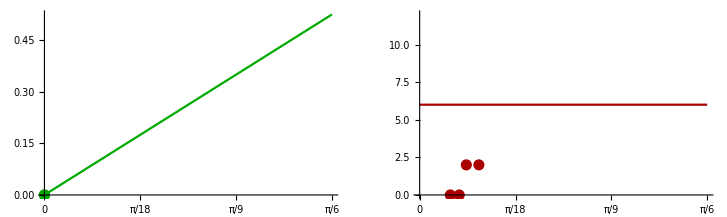

```mathematica
GraphicsRow[{plotErrorWithLinesAndPointsOne[6],plotErrorWithLinesAndPointsTwo[6]}]
```

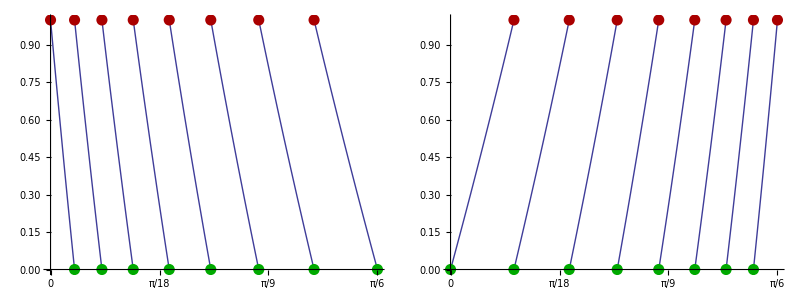

```mathematica
Grid[{{plotErrorWithLinesAndPointsOne[4],plotErrorWithLinesAndPointsTwo[4]}}]
```

We now need to find the intersecting points between the channels.
  To do this we first need to divide up the range into regions where there is only one intersection.

```mathematica
N[points[6]]
```

{{{0.,0.},{0.0360219,2.},{0.0720439,0.},{0.107696,2.},{0.143348,0.},{0.178282,2.},{0.213216,0.},{0.247125,2.},{0.281035,0.},{0.313669,2.},{0.346302,0.},{0.37747,2.},{0.408638,0.},{0.438211,2.},{0.467784,0.},{0.495691,2.},{0.523599,0.}},{{0.,0.},{0.0279073,2.},{0.0558146,0.},{0.0853877,2.},{0.114961,0.},{0.146129,2.},{0.177296,0.},{0.20993,2.},{0.242564,0.},{0.276474,2.},{0.310383,0.},{0.345317,2.},{0.380251,0.},{0.415903,2.},{0.451555,0.},{0.487577,2.},{0.523599,0.}}}

```mathematica
minThetaPts=thetaZeros[6];
maxThetaPts={(Most[minThetaPts[[1]]]+Rest[minThetaPts[[1]]])/2,(Most[minThetaPts[[2]]]+Rest[minThetaPts[[2]]])/2};
posRange={Thread[Inequality[Most[minThetaPts[[1]]],Less,Mod[ θ,Pi/6],LessEqual,maxThetaPts[[1]]]],   Thread[Inequality[Most[minThetaPts[[2]]],Less,Mod[ θ,Pi/6],LessEqual,maxThetaPts[[2]] ]]};
negRange={Thread[Inequality[maxThetaPts[[1]],Less,Mod[ θ,Pi/6],LessEqual,Rest[minThetaPts[[1]]]]],Thread[Inequality[maxThetaPts[[2]],Less,Mod[ θ,Pi/6],LessEqual,Rest[minThetaPts[[2]]]]]};
```

```mathematica
nearestRange={Thread[Inequality[Prepend[maxThetaPts[[1]],0],Less,Mod[ θ,Pi/6],LessEqual,Append[maxThetaPts[[1]],Pi/6]]],Thread[Inequality[Prepend[maxThetaPts[[2]],0],Less,Mod[ θ,Pi/6],LessEqual,Append[maxThetaPts[[2]],Pi/6]]]}
```

{{0<Mod[θ,π/6]≤1/2 ArcTan[1/(8 √3)],1/2 ArcTan[1/(8 √3)]<Mod[θ,π/6]≤1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)])<Mod[θ,π/6]≤1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8])<Mod[θ,π/6]≤1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8])<Mod[θ,π/6]≤1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)])<Mod[θ,π/6]≤1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4])<Mod[θ,π/6]≤1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4])<Mod[θ,π/6]≤1/2 (π/6+ArcTan[7/(8 √3)]),1/2 (π/6+ArcTan[7/(8 √3)])<Mod[θ,π/6]≤π/6},{0<Mod[θ,π/6]≤1/2 (π/6-ArcTan[7/(8 √3)]),1/2 (π/6-ArcTan[7/(8 √3)])<Mod[θ,π/6]≤1/2 (π/3-ArcTan[7/(8 √3)]-ArcTan[(√3)/4]),1/2 (π/3-ArcTan[7/(8 √3)]-ArcTan[(√3)/4])<Mod[θ,π/6]≤1/2 (π/3-ArcTan[5/(8 √3)]-ArcTan[(√3)/4]),1/2 (π/3-ArcTan[5/(8 √3)]-ArcTan[(√3)/4])<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[5/(8 √3)]),1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[5/(8 √3)])<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[(√3)/8]),1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[(√3)/8])<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(4 √3)]-ArcTan[(√3)/8]),1/2 (π/3-ArcTan[1/(4 √3)]-ArcTan[(√3)/8])<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(8 √3)]-ArcTan[1/(4 √3)]),1/2 (π/3-ArcTan[1/(8 √3)]-ArcTan[1/(4 √3)])<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(8 √3)]),1/2 (π/3-ArcTan[1/(8 √3)])<Mod[θ,π/6]≤π/6}}

```mathematica
Append[maxThetaPts,0]
```

{{1/2 ArcTan[1/(8 √3)],1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),1/2 (π/6+ArcTan[7/(8 √3)])},{1/2 (π/6-ArcTan[7/(8 √3)]),1/2 (π/3-ArcTan[7/(8 √3)]-ArcTan[(√3)/4]),1/2 (π/3-ArcTan[5/(8 √3)]-ArcTan[(√3)/4]),1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[5/(8 √3)]),1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[(√3)/8]),1/2 (π/3-ArcTan[1/(4 √3)]-ArcTan[(√3)/8]),1/2 (π/3-ArcTan[1/(8 √3)]-ArcTan[1/(4 √3)]),1/2 (π/3-ArcTan[1/(8 √3)])},0}

```mathematica
posRange
```

{{0<Mod[θ,π/6]≤1/2 ArcTan[1/(8 √3)],ArcTan[1/(8 √3)]<Mod[θ,π/6]≤1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),ArcTan[1/(4 √3)]<Mod[θ,π/6]≤1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),ArcTan[(√3)/8]<Mod[θ,π/6]≤1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),ArcTan[1/(2 √3)]<Mod[θ,π/6]≤1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),ArcTan[5/(8 √3)]<Mod[θ,π/6]≤1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),ArcTan[(√3)/4]<Mod[θ,π/6]≤1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),ArcTan[7/(8 √3)]<Mod[θ,π/6]≤1/2 (π/6+ArcTan[7/(8 √3)])},{0<Mod[θ,π/6]≤1/2 (π/6-ArcTan[7/(8 √3)]),π/6-ArcTan[7/(8 √3)]<Mod[θ,π/6]≤1/2 (π/3-ArcTan[7/(8 √3)]-ArcTan[(√3)/4]),π/6-ArcTan[(√3)/4]<Mod[θ,π/6]≤1/2 (π/3-ArcTan[5/(8 √3)]-ArcTan[(√3)/4]),π/6-ArcTan[5/(8 √3)]<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[5/(8 √3)]),π/6-ArcTan[1/(2 √3)]<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[(√3)/8]),π/6-ArcTan[(√3)/8]<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(4 √3)]-ArcTan[(√3)/8]),π/6-ArcTan[1/(4 √3)]<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(8 √3)]-ArcTan[1/(4 √3)]),π/6-ArcTan[1/(8 √3)]<Mod[θ,π/6]≤1/2 (π/3-ArcTan[1/(8 √3)])}}

```mathematica
toRange = Function[{ptsMin, ptsMax}, Thread[Inequality[ptsMin, Less, Mod[θ, Pi/6], LessEqual, ptsMax]]]; 
setupThetaRanges[n_] := Module[{}, 
minThetaPts=thetaZeros[n];
maxThetaPts=thetaMaxs[n];
(* maxThetaPts = {(Most[minThetaPts[[1]]] + Rest[minThetaPts[[1]]])/2, (Most[minThetaPts[[2]]] + Rest[minThetaPts[[2]]])/2};*) 
posRange = {toRange[Most[minThetaPts[[1]]],     maxThetaPts[[1]]], toRange[Most[minThetaPts[[2]]],     maxThetaPts[[2]]]}; 
negRange = {toRange[     maxThetaPts[[1]], Rest[minThetaPts[[1]]]],toRange[     maxThetaPts[[2]], Rest[minThetaPts[[2]]]]}; 
  nearestRange = {toRange[Prepend[maxThetaPts[[1]], 0], Append[maxThetaPts[[1]], Pi/6]], 
              toRange[Prepend[maxThetaPts[[2]], 0], Append[maxThetaPts[[2]], Pi/6]]}; 
thetaOneToPoint = Function[{θ}, 
Evaluate[Piecewise[{{0, θ == 0}, Sequence @@ Table[{i, nearestRange[[1,i]]}, {i, 1, Length[nearestRange[[1]]]}]}, 
        Length[nearestRange[[1]]] + 1]], Listable]; 
thetaTwoToPoint = Function[{θ}, 
Evaluate[Piecewise[{{0, θ == 0}, Sequence @@ Table[{i, nearestRange[[2,i]]}, {i, 1, Length[nearestRange[[2]]]}]}, 
        Length[nearestRange[[2]]] + 1]], Listable]; 
thetaMinVals = Sort[Union[Flatten[minThetaPts]], Less]; 
thetaMaxVals = Sort[Union[Flatten[maxThetaPts]], Less]; 
  thetaToPoint = Function[{θ}, {thetaOneToPoint[θ], thetaTwoToPoint[θ]}, Listable];
 ]
```

```mathematica
nn=6;
setupThetaRanges[nn];
```

```mathematica
TableForm[minThetaPts]
```

0 | ArcTan[1/(8 √3)] | ArcTan[1/(4 √3)] | ArcTan[(√3)/8] | ArcTan[1/(2 √3)] | ArcTan[5/(8 √3)] | ArcTan[(√3)/4] | ArcTan[7/(8 √3)] | π/6
0 | π/6-ArcTan[7/(8 √3)] | π/6-ArcTan[(√3)/4] | π/6-ArcTan[5/(8 √3)] | π/6-ArcTan[1/(2 √3)] | π/6-ArcTan[(√3)/8] | π/6-ArcTan[1/(4 √3)] | π/6-ArcTan[1/(8 √3)] | π/6

in each range we want to find the point of intersection between the errors for this we need to know which of the individual regions we are in for each of the channels.

```mathematica
Map[thetaToPoint,maxThetaPts]
```

{{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9}},{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8}}}

```mathematica
thetaVals
```

{0,π/6-ArcTan[7/(8 √3)],ArcTan[1/(8 √3)],π/6-ArcTan[(√3)/4],ArcTan[1/(4 √3)],π/6-ArcTan[5/(8 √3)],ArcTan[(√3)/8],π/6-ArcTan[1/(2 √3)],ArcTan[1/(2 √3)],π/6-ArcTan[(√3)/8],ArcTan[5/(8 √3)],π/6-ArcTan[1/(4 √3)],ArcTan[(√3)/4],π/6-ArcTan[1/(8 √3)],ArcTan[7/(8 √3)],π/6}

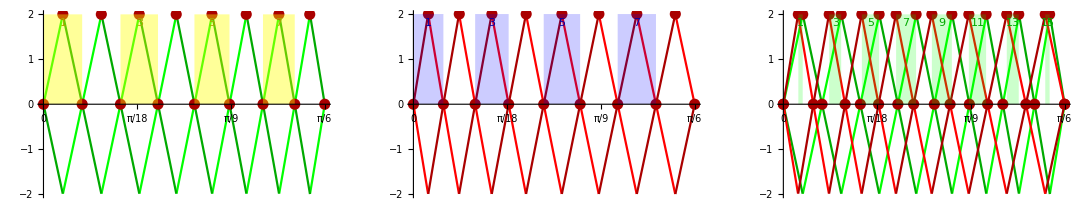

```mathematica
GraphicsRow[{Show[{plotErrorWithLinesAndPointsOne[nn],plotRegionsFromList[minThetaPts[[1]],Yellow,0.4]}],Show[{plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[minThetaPts[[2]],Blue,0.2]}],Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaMaxVals,Green,0.2]}]
}]
```

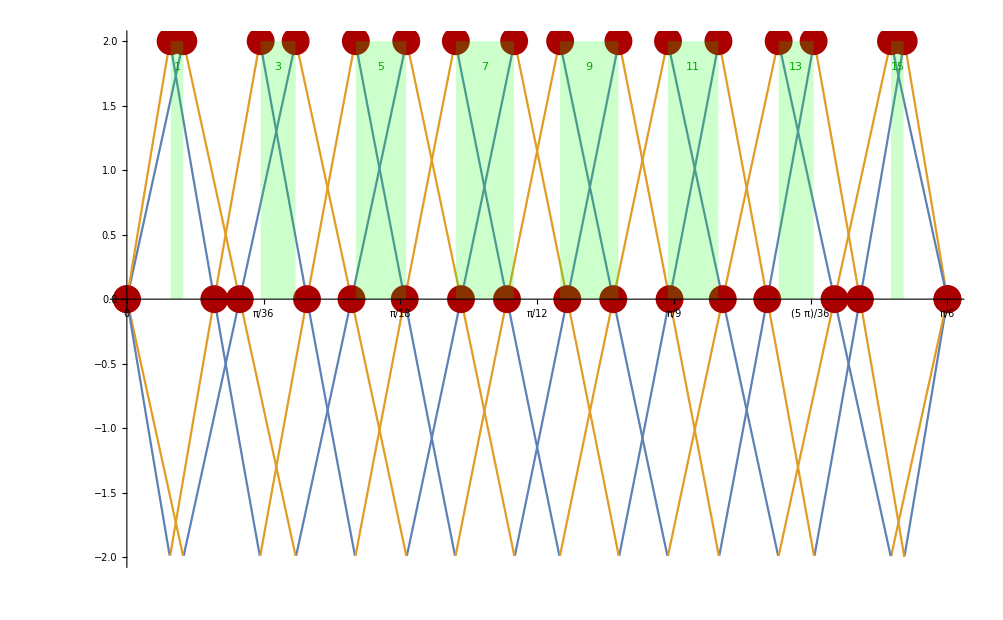

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaMaxVals,Green,0.2]}]
```

in each of the green intersecting regions we need the equatiuon of the lines to find the point of intersection. We use a linear approximation to find the points of intersection.

```mathematica
pts=points[nn];
intersect=Table[
intersectionFromPoints[{pts[[1,i]],
pts[[1,i+1]]},{pts[[2,i+1]],
pts[[2,i+2]]}],{i,1,Length[pts[[1]]]-2}];
```

```mathematica
Clear[intersections,correct]
correct[{x_,y_}]:=Module[{yOut,q},
yOut=Abs[y];
q=Quotient[yOut,2];
If[OddQ[q],{x,2(q+1)-yOut},{x,yOut-2 q}]
];
intersections[nn_,crit_:1,lowQ_:True]:=Module[{interPts,k,ratio},
pts=points[nn];
k=2/crit -1; (* turn crit into a ratio limit *)
interPts=Table[ intersectionFromPoints[{pts[[1,i]],pts[[1,i+1]]},{pts[[2,i+1]],pts[[2,i+2]]}],{i,1,Length[pts[[1]]]-2}];
interPts=Map[correct,interPts];
maxThetaRange=Rest[Sort[Union[Flatten[maxThetaPts]],Less]]-Most[Sort[Union[Flatten[maxThetaPts]],Less]];
minThetaRange=Rest[Sort[Union[Flatten[minThetaPts]],Less]]-Most[Sort[Union[Flatten[minThetaPts]],Less]];
ratio=maxThetaRange/minThetaRange;
Pick[interPts,Thread[Less[k,ratio]],lowQ]
];
```

```mathematica
plotErrorIntersect[nn_,crit_:2,lowQ_:True,color_:Red,size_:0.02]:=Module[{minMaxPts},
pts=points[nn];
intersect=intersections[nn,crit,True];
ListPlot[intersect,PlotStyle->{PointSize[size],color},PlotRange->{All,{0,2}}]]
```

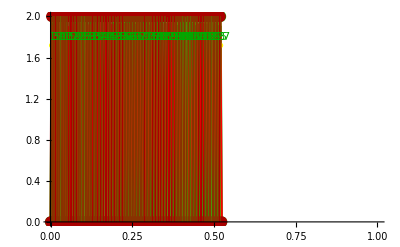

```mathematica
nn=9;setupThetaRanges[nn];Show[{plotErrorIntersect[nn,2,True,Red,0.008],plotErrorIntersect[nn,1,True,Orange,0.008],plotErrorIntersect[nn,1/2,True,Yellow,0.01],plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaMaxVals,Green,0.2]}]
```

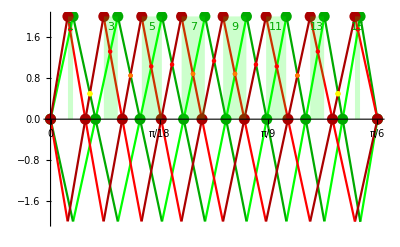

```mathematica
nn=6;setupThetaRanges[nn];Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaMaxVals,Green,0.2],plotErrorIntersect[nn,2,True,Red,0.008],plotErrorIntersect[nn,1,True,Orange,0.008],plotErrorIntersect[nn,1/2,True,Yellow,0.01]}]
```

We now need to classify the points as greater or less than one.

```mathematica
Clear[DrawAngle];
DrawAngle[pt1_,pt2_,pt3_]:={
Angle1=VectorAngle[{1,0},pt1-pt2];
Angle2=VectorAngle[pt3-pt2,{1,0}];
If[(pt1-pt2)[[2]]<0,Angle1=-Angle1];
If[(pt3-pt2)[[2]]<0,Angle2=-Angle2];
sAngle=Min[Angle1,Angle2];
eAngle=Max[Angle1,Angle2];
If[eAngle-sAngle<Pi,
Disk[pt2,0.2,{sAngle,eAngle}],
Disk[pt2,0.2,{eAngle,2Pi+sAngle}]]
};
h1=Subscript["h","1"];
h2=Subscript["h","2"];
Manipulate[
pts={{{0,2},{a,2}},{{(a-b)/2,0},{(a+b)/2,0}}};
inter=intersectionFromPoints[{pts[[1,1]],pts[[2,2]]},{pts[[2,1]],pts[[1,2]]}];
ht1=inter[[2]];
ht2=(2-inter[[2]]);
hights1={Black,Dashed,Line[{{a/2,0},inter}],Text[Style[h1,Medium,Bold],{a/2,ht1/2},{0,0},{1,0},Background->White]};
hights2={Darker[Orange],Dashed,Line[{{a/2,2},inter}],Text[Style[h2,Medium,Bold],{a/2,2-ht2/2},{0,0},{1,0},Background->White]};
base1={Darker[Orange],Dashed,Line[{{0,2},{a,2}}],Text[Style["a",Medium,Bold],{a/2,2},{0,-1},{1,0},Background->White]};
base2={Darker[Orange],Dashed,Line[{pts[[2,1]],pts[[2,2]]}],Text[Style["b",Medium,Bold],(pts[[2,1]]+pts[[2,2]])/2,{0,1},{1,0},Background->White]};

Row[{Graphics[{Line[{pts[[1,1]],pts[[2,2]]}],Line[{pts[[2,1]],pts[[1,2]]}],Green,DrawAngle[pts[[1,2]],pts[[2,1]],pts[[2,2]]],DrawAngle[pts[[1,1]],pts[[2,2]],pts[[2,1]]],DrawAngle[pts[[1,2]],pts[[1,1]],pts[[2,2]]],DrawAngle[pts[[1,1]],pts[[1,2]],pts[[2,1]]],Orange,DrawAngle[pts[[1,1]],inter,pts[[1,2]]],DrawAngle[pts[[2,1]],inter,pts[[2,2]]],hights1,hights2,base1,base2},Frame->True,FrameTicks->{None,{{0,0},{1,1},{2,2}}},PlotRange->{{Min[pts[[1,1,1]],pts[[2,1,1]]],2+Min[pts[[1,1,1]],pts[[2,1,1]]]},{-0.2,2.2}} ],Grid[{{TraditionalForm[h1/h2 =="b"/"a"]},{TraditionalForm[h1 + h2==2  ]},{TraditionalForm[h1 ==2 "b"/("a"+"b") ]}},Frame->True,Dividers->All,ItemSize->All]},Alignment->{Left,Top},BaselinePosition-> Top],
{{a,2},0,2},{{b,1},0,2}]
```

```mathematica
|
```

```mathematica
TraditionalForm[h1/h2 == b/a]
TraditionalForm[h1/(2-h1) == b/a]
TraditionalForm[h1==(2-h1) b/a]
TraditionalForm[h1==2 b/a -h1 b/a]
TraditionalForm[h1+h1 b/a==2 b/a ]
TraditionalForm[h1 (1+b/a)==2 b/a ]
TraditionalForm[h1 ==2 b/(a(1+b/a)) ]
TraditionalForm[h1 ==2 b/(a+b) ]
```

h1/h2==b/a

h1/(2-h1)==b/a

h1==(b (2-h1))/a

h1==(2 b)/a-(b h1)/a

(b h1)/a+h1==(2 b)/a

h1 (b/a+1)==(2 b)/a

h1==(2 b)/(a (b/a+1))

h1==(2 b)/(a+b)

```mathematica
maxThetaRange=Rest[Sort[Union[Flatten[maxThetaPts]],Less]]-Most[Sort[Union[Flatten[maxThetaPts]],Less]];
minThetaRange=Rest[Sort[Union[Flatten[minThetaPts]],Less]]-Most[Sort[Union[Flatten[minThetaPts]],Less]];
```

```mathematica
maxThetaRange=Rest[Sort[Union[Flatten[maxThetaPts]],Less]]-Most[Sort[Union[Flatten[maxThetaPts]],Less]];
minThetaRange=Rest[Sort[Union[Flatten[minThetaPts]],Less]]-Most[Sort[Union[Flatten[minThetaPts]],Less]];intersectHigh=Pick[intersect,Thread[Less[minThetaRange,maxThetaRange]],False];
intersectLow=Pick[intersect,Thread[Less[minThetaRange,maxThetaRange]],True];
```

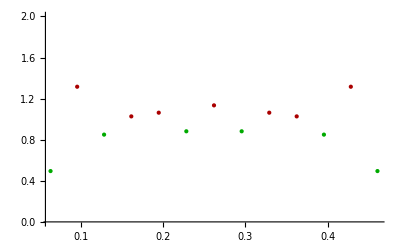

```mathematica
Show[{ListPlot[intersectLow,PlotStyle->{PointSize[Large],Darker[Green]},PlotRange->{All,{0,2}}],ListPlot[intersectHigh,PlotStyle->{PointSize[Large],Darker[Red]}]}]
```

```mathematica
midPoints=(Most[thetaMaxVals]+Rest[thetaMaxVals])/2;
```

```mathematica
N[midPoints]
```

{0.0319646,0.0607048,0.0965417,0.126912,0.162205,0.194106,0.228528,0.261799,0.295071,0.329493,0.361394,0.396687,0.427057,0.462894,0.491634}

```mathematica
thetaMaxVals
```

{1/2 (π/6-ArcTan[7/(8 √3)]),1/2 ArcTan[1/(8 √3)],1/2 (π/3-ArcTan[7/(8 √3)]-ArcTan[(√3)/4]),1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),1/2 (π/3-ArcTan[5/(8 √3)]-ArcTan[(√3)/4]),1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[5/(8 √3)]),1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),1/2 (π/3-ArcTan[1/(2 √3)]-ArcTan[(√3)/8]),1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),1/2 (π/3-ArcTan[1/(4 √3)]-ArcTan[(√3)/8]),1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),1/2 (π/3-ArcTan[1/(8 √3)]-ArcTan[1/(4 √3)]),1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),1/2 (π/3-ArcTan[1/(8 √3)]),1/2 (π/6+ArcTan[7/(8 √3)])}

```mathematica
minThetaPts[[1]]
```

{0,ArcTan[1/(8 √3)],ArcTan[1/(4 √3)],ArcTan[(√3)/8],ArcTan[1/(2 √3)],ArcTan[5/(8 √3)],ArcTan[(√3)/4],ArcTan[7/(8 √3)],π/6}

```mathematica
maxThetaPts[[1]]
```

{1/2 ArcTan[1/(8 √3)],1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),1/2 (π/6+ArcTan[7/(8 √3)])}

```mathematica
thetaOneToPoint[θ]
```

Piecewise[{{0, θ==0}, {1, 0<Mod[θ,π/6]≤1/2 ArcTan[1/(8 √3)]}, {2, 1/2 ArcTan[1/(8 √3)]<Mod[θ,π/6]≤1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)])}, {3, 1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)])<Mod[θ,π/6]≤1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8])}, {4, 1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8])<Mod[θ,π/6]≤1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8])}, {5, 1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8])<Mod[θ,π/6]≤1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)])}, {6, 1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)])<Mod[θ,π/6]≤1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4])}, {7, 1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4])<Mod[θ,π/6]≤1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4])}, {8, 1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4])<Mod[θ,π/6]≤1/2 (π/6+ArcTan[7/(8 √3)])}, {9, 1/2 (π/6+ArcTan[7/(8 √3)])<Mod[θ,π/6]≤π/6}, {10, True}}]

```mathematica
thetaToPoint
```

Function[{θ},{thetaOneToPoint[θ],thetaTwoToPoint[θ]},Listable]

```mathematica
thetaMidPoints =Map[thetaToPoint,midPoints]
```

{{1,2},{2,2},{2,3},{3,3},{3,4},{4,4},{4,5},{5,5},{5,6},{6,6},{6,7},{7,7},{7,8},{8,8},{8,9}}

```mathematica
pts1
```

{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}

```mathematica
Table[{pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]},{i,1,Length[thetaMidPoints]}]
```

Part::partw: Part 3 of {0, 0} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{{0,1/2 ArcTan[1/(8 √3)],ArcTan[1/(8 √3)],1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),ArcTan[1/(4 √3)],1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),ArcTan[(√3)/8],1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),ArcTan[1/(2 √3)],1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),ArcTan[5/(8 √3)],1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),ArcTan[(√3)/4],1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),ArcTan[7/(8 √3)],1/2 (π/6+ArcTan[7/(8 √3)]),π/6},{0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0}},{{0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0},{0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0}},{{0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0},{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,3⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,3⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,3⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,3⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,4⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,4⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,4⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,4⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,5⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,5⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,5⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,5⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,6⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,6⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,6⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,6⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,7⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,7⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,7⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,7⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,8⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,8⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,8⟧},{{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,8⟧,{{0,0},{1/2 ArcTan[1/(8 √3)],2},{ArcTan[1/(8 √3)],0},{1/2 (ArcTan[1/(8 √3)]+ArcTan[1/(4 √3)]),2},{ArcTan[1/(4 √3)],0},{1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/8]),2},{ArcTan[(√3)/8],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[(√3)/8]),2},{ArcTan[1/(2 √3)],0},{1/2 (ArcTan[1/(2 √3)]+ArcTan[5/(8 √3)]),2},{ArcTan[5/(8 √3)],0},{1/2 (ArcTan[5/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[(√3)/4],0},{1/2 (ArcTan[7/(8 √3)]+ArcTan[(√3)/4]),2},{ArcTan[7/(8 √3)],0},{1/2 (π/6+ArcTan[7/(8 √3)]),2},{π/6,0}}⟦All,9⟧}}

```mathematica
pts1=points[nn][[1]];
pts2=points[nn][[1]];
```

```mathematica
midPoints=(Most[thetaMaxVals]+Rest[thetaMaxVals])/2;
thetaMidPoints =Map[thetaToPoint,thetaMid];
pts1=ptsOne[nn];
pts2=ptsTwo[nn];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]]
```

{{0.0278999,0.274781},{0.0574832,0.566142},{0.0886554,0.873151},{0.121276,0.222839},{0.155194,0.6057},{0.225777,0.46404},{0.261799,0.932906},{0.297822,0.46404},{0.368404,0.6057},{0.402322,0.222839},{0.434943,0.873151},{0.466116,0.566142},{0.495699,0.274781}}

```mathematica
correct[{x_,y_}]:=If[y>2,{x,4-y},If[y<0,{x,-y},{x,y}]]
```

```mathematica
Map[correct,intersect]
```

{{-(ArcTan[1/(16 √3)] (π/6-ArcTan[(5 √3)/16]))/(π/6-ArcTan[1/(16 √3)]-2 (π/6-ArcTan[(5 √3)/16])-ArcTan[(5 √3)/16]),-(4 (π/6-ArcTan[(5 √3)/16]))/(π/6-ArcTan[1/(16 √3)]-2 (π/6-ArcTan[(5 √3)/16])-ArcTan[(5 √3)/16])},{(-ArcTan[1/(16 √3)] (π/6-ArcTan[(5 √3)/16])+ArcTan[1/(16 √3)] (π/3-ArcTan[7/(8 √3)]-ArcTan[(5 √3)/16]))/(π/3+ArcTan[1/(16 √3)]-ArcTan[7/(8 √3)]-2 (π/6-ArcTan[(5 √3)/16])-ArcTan[(5 √3)/16]),(4 ArcTan[1/(16 √3)]-4 (π/6-ArcTan[(5 √3)/16]))/(π/3+ArcTan[1/(16 √3)]-ArcTan[7/(8 √3)]-2 (π/6-ArcTan[(5 √3)/16])-ArcTan[(5 √3)/16])},{(-(ArcTan[1/(16 √3)]+ArcTan[1/(8 √3)]) (π/6-ArcTan[7/(8 √3)])+ArcTan[1/(16 √3)] (π/3-ArcTan[7/(8 √3)]-ArcTan[(5 √3)/16]))/(π/3+2 (ArcTan[1/(16 √3)]+1/2 (-ArcTan[1/(16 √3)]-ArcTan[1/(8 √3)]))-2 (π/6-ArcTan[7/(8 √3)])-ArcTan[7/(8 √3)]-ArcTan[(5 √3)/16]),(4 ArcTan[1/(16 √3)]-4 (π/6-ArcTan[7/(8 √3)]))/(π/3+2 (ArcTan[1/(16 √3)]+1/2 (-ArcTan[1/(16 √3)]-ArcTan[1/(8 √3)]))-2 (π/6-ArcTan[7/(8 √3)])-ArcTan[7/(8 √3)]-ArcTan[(5 √3)/16])},{(-(ArcTan[1/(16 √3)]+ArcTan[1/(8 √3)]) (π/6-ArcTan[7/(8 √3)])+ArcTan[1/(8 √3)] (π/3-ArcTan[13/(16 √3)]-ArcTan[7/(8 √3)]))/(π/3-2 (-ArcTan[1/(8 √3)]+1/2 (ArcTan[1/(16 √3)]+ArcTan[1/(8 √3)]))-ArcTan[13/(16 √3)]-2 (π/6-ArcTan[7/(8 √3)])-ArcTan[7/(8 √3)]),(4 ArcTan[1/(8 √3)]-4 (π/6-ArcTan[7/(8 √3)]))/(π/3-2 (-ArcTan[1/(8 √3)]+1/2 (ArcTan[1/(16 √3)]+ArcTan[1/(8 √3)]))-ArcTan[13/(16 √3)]-2 (π/6-ArcTan[7/(8 √3)])-ArcTan[7/(8 √3)])},{(ArcTan[1/(8 √3)] (π/3-ArcTan[13/(16 √3)]-ArcTan[7/(8 √3)])-(π/6-ArcTan[13/(16 √3)]) (ArcTan[1/(8 √3)]+ArcTan[(√3)/16]))/(π/3-2 (π/6-ArcTan[13/(16 √3)])-ArcTan[13/(16 √3)]-ArcTan[7/(8 √3)]+2 (ArcTan[1/(8 √3)]+1/2 (-ArcTan[1/(8 √3)]-ArcTan[(√3)/16]))),(4 ArcTan[1/(8 √3)]-4 (π/6-ArcTan[13/(16 √3)]))/(π/3-2 (π/6-ArcTan[13/(16 √3)])-ArcTan[13/(16 √3)]-ArcTan[7/(8 √3)]+2 (ArcTan[1/(8 √3)]+1/2 (-ArcTan[1/(8 √3)]-ArcTan[(√3)/16])))},{(-(π/6-ArcTan[13/(16 √3)]) (ArcTan[1/(8 √3)]+ArcTan[(√3)/16])+ArcTan[(√3)/16] (π/3-ArcTan[13/(16 √3)]-ArcTan[(√3)/4]))/(π/3-2 (π/6-ArcTan[13/(16 √3)])-ArcTan[13/(16 √3)]-2 (-ArcTan[(√3)/16]+1/2 (ArcTan[1/(8 √3)]+ArcTan[(√3)/16]))-ArcTan[(√3)/4]),(-4 (π/6-ArcTan[13/(16 √3)])+4 ArcTan[(√3)/16])/(π/3-2 (π/6-ArcTan[13/(16 √3)])-ArcTan[13/(16 √3)]-2 (-ArcTan[(√3)/16]+1/2 (ArcTan[1/(8 √3)]+ArcTan[(√3)/16]))-ArcTan[(√3)/4])},{(-(ArcTan[1/(4 √3)]+ArcTan[(√3)/16]) (π/6-ArcTan[(√3)/4])+ArcTan[(√3)/16] (π/3-ArcTan[13/(16 √3)]-ArcTan[(√3)/4]))/(π/3-ArcTan[13/(16 √3)]+2 (1/2 (-ArcTan[1/(4 √3)]-ArcTan[(√3)/16])+ArcTan[(√3)/16])-2 (π/6-ArcTan[(√3)/4])-ArcTan[(√3)/4]),(4 ArcTan[(√3)/16]-4 (π/6-ArcTan[(√3)/4]))/(π/3-ArcTan[13/(16 √3)]+2 (1/2 (-ArcTan[1/(4 √3)]-ArcTan[(√3)/16])+ArcTan[(√3)/16])-2 (π/6-ArcTan[(√3)/4])-ArcTan[(√3)/4])},{(-(ArcTan[1/(4 √3)]+ArcTan[(√3)/16]) (π/6-ArcTan[(√3)/4])+ArcTan[1/(4 √3)] (π/3-ArcTan[11/(16 √3)]-ArcTan[(√3)/4]))/(π/3-ArcTan[11/(16 √3)]-2 (-ArcTan[1/(4 √3)]+1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/16]))-2 (π/6-ArcTan[(√3)/4])-ArcTan[(√3)/4]),(4 ArcTan[1/(4 √3)]-4 (π/6-ArcTan[(√3)/4]))/(π/3-ArcTan[11/(16 √3)]-2 (-ArcTan[1/(4 √3)]+1/2 (ArcTan[1/(4 √3)]+ArcTan[(√3)/16]))-2 (π/6-ArcTan[(√3)/4])-ArcTan[(√3)/4])},{(-(ArcTan[1/(4 √3)]+ArcTan[5/(16 √3)]) (π/6-ArcTan[11/(16 √3)])+ArcTan[1/(4 √3)] (π/3-ArcTan[11/(16 √3)]-ArcTan[(√3)/4]))/(π/3+2 (ArcTan[1/(4 √3)]+1/2 (-ArcTan[1/(4 √3)]-ArcTan[5/(16 √3)]))-2 (π/6-ArcTan[11/(16 √3)])-ArcTan[11/(16 √3)]-ArcTan[(√3)/4]),(4 ArcTan[1/(4 √3)]-4 (π/6-ArcTan[11/(16 √3)]))/(π/3+2 (ArcTan[1/(4 √3)]+1/2 (-ArcTan[1/(4 √3)]-ArcTan[5/(16 √3)]))-2 (π/6-ArcTan[11/(16 √3)])-ArcTan[11/(16 √3)]-ArcTan[(√3)/4])},{(-(ArcTan[1/(4 √3)]+ArcTan[5/(16 √3)]) (π/6-ArcTan[11/(16 √3)])+ArcTan[5/(16 √3)] (π/3-ArcTan[5/(8 √3)]-ArcTan[11/(16 √3)]))/(π/3-2 (-ArcTan[5/(16 √3)]+1/2 (ArcTan[1/(4 √3)]+ArcTan[5/(16 √3)]))-ArcTan[5/(8 √3)]-2 (π/6-ArcTan[11/(16 √3)])-ArcTan[11/(16 √3)]),(4 ArcTan[5/(16 √3)]-4 (π/6-ArcTan[11/(16 √3)]))/(π/3-2 (-ArcTan[5/(16 √3)]+1/2 (ArcTan[1/(4 √3)]+ArcTan[5/(16 √3)]))-ArcTan[5/(8 √3)]-2 (π/6-ArcTan[11/(16 √3)])-ArcTan[11/(16 √3)])},{(ArcTan[5/(16 √3)] (π/3-ArcTan[5/(8 √3)]-ArcTan[11/(16 √3)])-(π/6-ArcTan[5/(8 √3)]) (ArcTan[5/(16 √3)]+ArcTan[(√3)/8]))/(π/3-2 (π/6-ArcTan[5/(8 √3)])-ArcTan[5/(8 √3)]-ArcTan[11/(16 √3)]+2 (ArcTan[5/(16 √3)]+1/2 (-ArcTan[5/(16 √3)]-ArcTan[(√3)/8]))),-(4 ArcTan[5/(16 √3)]-4 (π/6-ArcTan[5/(8 √3)]))/(π/3-2 (π/6-ArcTan[5/(8 √3)])-ArcTan[5/(8 √3)]-ArcTan[11/(16 √3)]+2 (ArcTan[5/(16 √3)]+1/2 (-ArcTan[5/(16 √3)]-ArcTan[(√3)/8])))},{(-(π/6-ArcTan[5/(8 √3)]) (ArcTan[5/(16 √3)]+ArcTan[(√3)/8])+ArcTan[(√3)/8] (π/3-ArcTan[5/(8 √3)]-ArcTan[(3 √3)/16]))/(π/3-2 (π/6-ArcTan[5/(8 √3)])-ArcTan[5/(8 √3)]-2 (-ArcTan[(√3)/8]+1/2 (ArcTan[5/(16 √3)]+ArcTan[(√3)/8]))-ArcTan[(3 √3)/16]),4-(-4 (π/6-ArcTan[5/(8 √3)])+4 ArcTan[(√3)/8])/(π/3-2 (π/6-ArcTan[5/(8 √3)])-ArcTan[5/(8 √3)]-2 (-ArcTan[(√3)/8]+1/2 (ArcTan[5/(16 √3)]+ArcTan[(√3)/8]))-ArcTan[(3 √3)/16])},{(-(ArcTan[7/(16 √3)]+ArcTan[(√3)/8]) (π/6-ArcTan[(3 √3)/16])+ArcTan[(√3)/8] (π/3-ArcTan[5/(8 √3)]-ArcTan[(3 √3)/16]))/(π/3-ArcTan[5/(8 √3)]+2 (1/2 (-ArcTan[7/(16 √3)]-ArcTan[(√3)/8])+ArcTan[(√3)/8])-2 (π/6-ArcTan[(3 √3)/16])-ArcTan[(3 √3)/16]),-(4 ArcTan[(√3)/8]-4 (π/6-ArcTan[(3 √3)/16]))/(π/3-ArcTan[5/(8 √3)]+2 (1/2 (-ArcTan[7/(16 √3)]-ArcTan[(√3)/8])+ArcTan[(√3)/8])-2 (π/6-ArcTan[(3 √3)/16])-ArcTan[(3 √3)/16])},{(-(ArcTan[7/(16 √3)]+ArcTan[(√3)/8]) (π/6-ArcTan[(3 √3)/16])+ArcTan[7/(16 √3)] (π/3-ArcTan[1/(2 √3)]-ArcTan[(3 √3)/16]))/(π/3-ArcTan[1/(2 √3)]-2 (-ArcTan[7/(16 √3)]+1/2 (ArcTan[7/(16 √3)]+ArcTan[(√3)/8]))-2 (π/6-ArcTan[(3 √3)/16])-ArcTan[(3 √3)/16]),4-(4 ArcTan[7/(16 √3)]-4 (π/6-ArcTan[(3 √3)/16]))/(π/3-ArcTan[1/(2 √3)]-2 (-ArcTan[7/(16 √3)]+1/2 (ArcTan[7/(16 √3)]+ArcTan[(√3)/8]))-2 (π/6-ArcTan[(3 √3)/16])-ArcTan[(3 √3)/16])},{(-(π/6-ArcTan[1/(2 √3)]) (ArcTan[7/(16 √3)]+ArcTan[1/(2 √3)])+ArcTan[7/(16 √3)] (π/3-ArcTan[1/(2 √3)]-ArcTan[(3 √3)/16]))/(π/3+2 (ArcTan[7/(16 √3)]+1/2 (-ArcTan[7/(16 √3)]-ArcTan[1/(2 √3)]))-2 (π/6-ArcTan[1/(2 √3)])-ArcTan[1/(2 √3)]-ArcTan[(3 √3)/16]),-(4 ArcTan[7/(16 √3)]-4 (π/6-ArcTan[1/(2 √3)]))/(π/3+2 (ArcTan[7/(16 √3)]+1/2 (-ArcTan[7/(16 √3)]-ArcTan[1/(2 √3)]))-2 (π/6-ArcTan[1/(2 √3)])-ArcTan[1/(2 √3)]-ArcTan[(3 √3)/16])},{((π/3-ArcTan[7/(16 √3)]-ArcTan[1/(2 √3)]) ArcTan[1/(2 √3)]-(π/6-ArcTan[1/(2 √3)]) (ArcTan[7/(16 √3)]+ArcTan[1/(2 √3)]))/(π/3-ArcTan[7/(16 √3)]-2 (π/6-ArcTan[1/(2 √3)])-ArcTan[1/(2 √3)]-2 (-ArcTan[1/(2 √3)]+1/2 (ArcTan[7/(16 √3)]+ArcTan[1/(2 √3)]))),4-(-4 (π/6-ArcTan[1/(2 √3)])+4 ArcTan[1/(2 √3)])/(π/3-ArcTan[7/(16 √3)]-2 (π/6-ArcTan[1/(2 √3)])-ArcTan[1/(2 √3)]-2 (-ArcTan[1/(2 √3)]+1/2 (ArcTan[7/(16 √3)]+ArcTan[1/(2 √3)])))},{((π/3-ArcTan[7/(16 √3)]-ArcTan[1/(2 √3)]) ArcTan[1/(2 √3)]-(π/6-ArcTan[7/(16 √3)]) (ArcTan[1/(2 √3)]+ArcTan[(3 √3)/16]))/(π/3-2 (π/6-ArcTan[7/(16 √3)])-ArcTan[7/(16 √3)]-ArcTan[1/(2 √3)]+2 (ArcTan[1/(2 √3)]+1/2 (-ArcTan[1/(2 √3)]-ArcTan[(3 √3)/16]))),-(-4 (π/6-ArcTan[7/(16 √3)])+4 ArcTan[1/(2 √3)])/(π/3-2 (π/6-ArcTan[7/(16 √3)])-ArcTan[7/(16 √3)]-ArcTan[1/(2 √3)]+2 (ArcTan[1/(2 √3)]+1/2 (-ArcTan[1/(2 √3)]-ArcTan[(3 √3)/16])))},{((π/3-ArcTan[7/(16 √3)]-ArcTan[(√3)/8]) ArcTan[(3 √3)/16]-(π/6-ArcTan[7/(16 √3)]) (ArcTan[1/(2 √3)]+ArcTan[(3 √3)/16]))/(π/3-2 (π/6-ArcTan[7/(16 √3)])-ArcTan[7/(16 √3)]-ArcTan[(√3)/8]-2 (-ArcTan[(3 √3)/16]+1/2 (ArcTan[1/(2 √3)]+ArcTan[(3 √3)/16]))),4-(-4 (π/6-ArcTan[7/(16 √3)])+4 ArcTan[(3 √3)/16])/(π/3-2 (π/6-ArcTan[7/(16 √3)])-ArcTan[7/(16 √3)]-ArcTan[(√3)/8]-2 (-ArcTan[(3 √3)/16]+1/2 (ArcTan[1/(2 √3)]+ArcTan[(3 √3)/16])))},{((π/3-ArcTan[7/(16 √3)]-ArcTan[(√3)/8]) ArcTan[(3 √3)/16]-(π/6-ArcTan[(√3)/8]) (ArcTan[5/(8 √3)]+ArcTan[(3 √3)/16]))/(π/3-ArcTan[7/(16 √3)]-2 (π/6-ArcTan[(√3)/8])-ArcTan[(√3)/8]+2 (1/2 (-ArcTan[5/(8 √3)]-ArcTan[(3 √3)/16])+ArcTan[(3 √3)/16])),-(-4 (π/6-ArcTan[(√3)/8])+4 ArcTan[(3 √3)/16])/(π/3-ArcTan[7/(16 √3)]-2 (π/6-ArcTan[(√3)/8])-ArcTan[(√3)/8]+2 (1/2 (-ArcTan[5/(8 √3)]-ArcTan[(3 √3)/16])+ArcTan[(3 √3)/16]))},{(ArcTan[5/(8 √3)] (π/3-ArcTan[5/(16 √3)]-ArcTan[(√3)/8])-(π/6-ArcTan[(√3)/8]) (ArcTan[5/(8 √3)]+ArcTan[(3 √3)/16]))/(π/3-ArcTan[5/(16 √3)]-2 (π/6-ArcTan[(√3)/8])-ArcTan[(√3)/8]-2 (-ArcTan[5/(8 √3)]+1/2 (ArcTan[5/(8 √3)]+ArcTan[(3 √3)/16]))),4-(4 ArcTan[5/(8 √3)]-4 (π/6-ArcTan[(√3)/8]))/(π/3-ArcTan[5/(16 √3)]-2 (π/6-ArcTan[(√3)/8])-ArcTan[(√3)/8]-2 (-ArcTan[5/(8 √3)]+1/2 (ArcTan[5/(8 √3)]+ArcTan[(3 √3)/16])))},{(-(π/6-ArcTan[5/(16 √3)]) (ArcTan[5/(8 √3)]+ArcTan[11/(16 √3)])+ArcTan[5/(8 √3)] (π/3-ArcTan[5/(16 √3)]-ArcTan[(√3)/8]))/(π/3-2 (π/6-ArcTan[5/(16 √3)])-ArcTan[5/(16 √3)]+2 (ArcTan[5/(8 √3)]+1/2 (-ArcTan[5/(8 √3)]-ArcTan[11/(16 √3)]))-ArcTan[(√3)/8]),-(-4 (π/6-ArcTan[5/(16 √3)])+4 ArcTan[5/(8 √3)])/(π/3-2 (π/6-ArcTan[5/(16 √3)])-ArcTan[5/(16 √3)]+2 (ArcTan[5/(8 √3)]+1/2 (-ArcTan[5/(8 √3)]-ArcTan[11/(16 √3)]))-ArcTan[(√3)/8])},{((π/3-ArcTan[1/(4 √3)]-ArcTan[5/(16 √3)]) ArcTan[11/(16 √3)]-(π/6-ArcTan[5/(16 √3)]) (ArcTan[5/(8 √3)]+ArcTan[11/(16 √3)]))/(π/3-ArcTan[1/(4 √3)]-2 (π/6-ArcTan[5/(16 √3)])-ArcTan[5/(16 √3)]-2 (-ArcTan[11/(16 √3)]+1/2 (ArcTan[5/(8 √3)]+ArcTan[11/(16 √3)]))),(-4 (π/6-ArcTan[5/(16 √3)])+4 ArcTan[11/(16 √3)])/(π/3-ArcTan[1/(4 √3)]-2 (π/6-ArcTan[5/(16 √3)])-ArcTan[5/(16 √3)]-2 (-ArcTan[11/(16 √3)]+1/2 (ArcTan[5/(8 √3)]+ArcTan[11/(16 √3)])))},{((π/3-ArcTan[1/(4 √3)]-ArcTan[5/(16 √3)]) ArcTan[11/(16 √3)]-(π/6-ArcTan[1/(4 √3)]) (ArcTan[11/(16 √3)]+ArcTan[(√3)/4]))/(π/3-2 (π/6-ArcTan[1/(4 √3)])-ArcTan[1/(4 √3)]-ArcTan[5/(16 √3)]+2 (ArcTan[11/(16 √3)]+1/2 (-ArcTan[11/(16 √3)]-ArcTan[(√3)/4]))),(-4 (π/6-ArcTan[1/(4 √3)])+4 ArcTan[11/(16 √3)])/(π/3-2 (π/6-ArcTan[1/(4 √3)])-ArcTan[1/(4 √3)]-ArcTan[5/(16 √3)]+2 (ArcTan[11/(16 √3)]+1/2 (-ArcTan[11/(16 √3)]-ArcTan[(√3)/4])))},{((π/3-ArcTan[1/(4 √3)]-ArcTan[(√3)/16]) ArcTan[(√3)/4]-(π/6-ArcTan[1/(4 √3)]) (ArcTan[11/(16 √3)]+ArcTan[(√3)/4]))/(π/3-2 (π/6-ArcTan[1/(4 √3)])-ArcTan[1/(4 √3)]-ArcTan[(√3)/16]-2 (-ArcTan[(√3)/4]+1/2 (ArcTan[11/(16 √3)]+ArcTan[(√3)/4]))),(-4 (π/6-ArcTan[1/(4 √3)])+4 ArcTan[(√3)/4])/(π/3-2 (π/6-ArcTan[1/(4 √3)])-ArcTan[1/(4 √3)]-ArcTan[(√3)/16]-2 (-ArcTan[(√3)/4]+1/2 (ArcTan[11/(16 √3)]+ArcTan[(√3)/4])))},{((π/3-ArcTan[1/(4 √3)]-ArcTan[(√3)/16]) ArcTan[(√3)/4]-(π/6-ArcTan[(√3)/16]) (ArcTan[13/(16 √3)]+ArcTan[(√3)/4]))/(π/3-ArcTan[1/(4 √3)]-2 (π/6-ArcTan[(√3)/16])-ArcTan[(√3)/16]+2 (1/2 (-ArcTan[13/(16 √3)]-ArcTan[(√3)/4])+ArcTan[(√3)/4])),(-4 (π/6-ArcTan[(√3)/16])+4 ArcTan[(√3)/4])/(π/3-ArcTan[1/(4 √3)]-2 (π/6-ArcTan[(√3)/16])-ArcTan[(√3)/16]+2 (1/2 (-ArcTan[13/(16 √3)]-ArcTan[(√3)/4])+ArcTan[(√3)/4]))},{(ArcTan[13/(16 √3)] (π/3-ArcTan[1/(8 √3)]-ArcTan[(√3)/16])-(π/6-ArcTan[(√3)/16]) (ArcTan[13/(16 √3)]+ArcTan[(√3)/4]))/(π/3-ArcTan[1/(8 √3)]-2 (π/6-ArcTan[(√3)/16])-ArcTan[(√3)/16]-2 (-ArcTan[13/(16 √3)]+1/2 (ArcTan[13/(16 √3)]+ArcTan[(√3)/4]))),(4 ArcTan[13/(16 √3)]-4 (π/6-ArcTan[(√3)/16]))/(π/3-ArcTan[1/(8 √3)]-2 (π/6-ArcTan[(√3)/16])-ArcTan[(√3)/16]-2 (-ArcTan[13/(16 √3)]+1/2 (ArcTan[13/(16 √3)]+ArcTan[(√3)/4])))},{(-(π/6-ArcTan[1/(8 √3)]) (ArcTan[13/(16 √3)]+ArcTan[7/(8 √3)])+ArcTan[13/(16 √3)] (π/3-ArcTan[1/(8 √3)]-ArcTan[(√3)/16]))/(π/3-2 (π/6-ArcTan[1/(8 √3)])-ArcTan[1/(8 √3)]+2 (ArcTan[13/(16 √3)]+1/2 (-ArcTan[13/(16 √3)]-ArcTan[7/(8 √3)]))-ArcTan[(√3)/16]),(-4 (π/6-ArcTan[1/(8 √3)])+4 ArcTan[13/(16 √3)])/(π/3-2 (π/6-ArcTan[1/(8 √3)])-ArcTan[1/(8 √3)]+2 (ArcTan[13/(16 √3)]+1/2 (-ArcTan[13/(16 √3)]-ArcTan[7/(8 √3)]))-ArcTan[(√3)/16])},{((π/3-ArcTan[1/(16 √3)]-ArcTan[1/(8 √3)]) ArcTan[7/(8 √3)]-(π/6-ArcTan[1/(8 √3)]) (ArcTan[13/(16 √3)]+ArcTan[7/(8 √3)]))/(π/3-ArcTan[1/(16 √3)]-2 (π/6-ArcTan[1/(8 √3)])-ArcTan[1/(8 √3)]-2 (-ArcTan[7/(8 √3)]+1/2 (ArcTan[13/(16 √3)]+ArcTan[7/(8 √3)]))),(-4 (π/6-ArcTan[1/(8 √3)])+4 ArcTan[7/(8 √3)])/(π/3-ArcTan[1/(16 √3)]-2 (π/6-ArcTan[1/(8 √3)])-ArcTan[1/(8 √3)]-2 (-ArcTan[7/(8 √3)]+1/2 (ArcTan[13/(16 √3)]+ArcTan[7/(8 √3)])))},{((π/3-ArcTan[1/(16 √3)]-ArcTan[1/(8 √3)]) ArcTan[7/(8 √3)]-(π/6-ArcTan[1/(16 √3)]) (ArcTan[7/(8 √3)]+ArcTan[(5 √3)/16]))/(π/3-2 (π/6-ArcTan[1/(16 √3)])-ArcTan[1/(16 √3)]-ArcTan[1/(8 √3)]+2 (ArcTan[7/(8 √3)]+1/2 (-ArcTan[7/(8 √3)]-ArcTan[(5 √3)/16]))),(-4 (π/6-ArcTan[1/(16 √3)])+4 ArcTan[7/(8 √3)])/(π/3-2 (π/6-ArcTan[1/(16 √3)])-ArcTan[1/(16 √3)]-ArcTan[1/(8 √3)]+2 (ArcTan[7/(8 √3)]+1/2 (-ArcTan[7/(8 √3)]-ArcTan[(5 √3)/16])))},{((π/3-ArcTan[1/(16 √3)]) ArcTan[(5 √3)/16]-(π/6-ArcTan[1/(16 √3)]) (ArcTan[7/(8 √3)]+ArcTan[(5 √3)/16]))/(π/3-2 (π/6-ArcTan[1/(16 √3)])-ArcTan[1/(16 √3)]-2 (-ArcTan[(5 √3)/16]+1/2 (ArcTan[7/(8 √3)]+ArcTan[(5 √3)/16]))),(-4 (π/6-ArcTan[1/(16 √3)])+4 ArcTan[(5 √3)/16])/(π/3-2 (π/6-ArcTan[1/(16 √3)])-ArcTan[1/(16 √3)]-2 (-ArcTan[(5 √3)/16]+1/2 (ArcTan[7/(8 √3)]+ArcTan[(5 √3)/16])))},{((π/3-ArcTan[1/(16 √3)]) ArcTan[(5 √3)/16]-1/6 π (π/6+ArcTan[(5 √3)/16]))/(-ArcTan[1/(16 √3)]+2 (1/2 (-π/6-ArcTan[(5 √3)/16])+ArcTan[(5 √3)/16])),(-(2 π)/3+4 ArcTan[(5 √3)/16])/(-ArcTan[1/(16 √3)]+2 (1/2 (-π/6-ArcTan[(5 √3)/16])+ArcTan[(5 √3)/16]))}}

```mathematica
Quotient[1.9,2]
```

0

```mathematica
Clear[inter1st,inter2nd]
nn=8;setupThetaRanges[nn];
pts=points[nn];
intersect=Table[
intersectionFromPoints[{pts[[1,i]],pts[[1,i+1]]},{pts[[2,i+1]],pts[[2,i+2]]}],{i,1,Length[pts[[1]]]-2}];
intersectCorrected=Map[correct,intersect];
inter1st[nn]=Append[Prepend[intersect[[1;;All;;2]],{0,2}],{Pi/6,2}];
inter2nd[nn]=Append[Prepend[intersect[[2;;All;;2]],{0,0}],{Pi/6,0}];
```

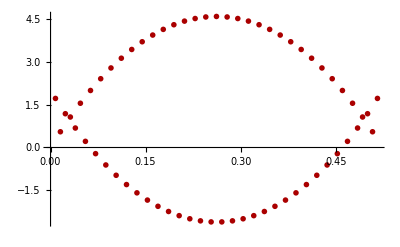

```mathematica
ListPlot[intersect,PlotStyle->{PointSize[0.01],Darker[Red]},Epilog->{Line[{{0,nn},{Pi/6,nn}}]}]
```

```mathematica
FullSimplify[Max[Transpose[inter2nd[nn]][[2]]]]
N[%]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -4\ ArcTan[29/32\ √3] - 4\ (π/6 - ArcTan[Times[« 2 »]])/π/3 - ArcTan[1/16\ Power[« 2 »]] - 2\ (-ArcTan[« 1 »] + 1/2\ Plus[« 2 »]) - 2\ (π/6 - ArcTan[« 1 »]) - ArcTan[1/32\ Power[« 2 »]] + -4\ (π/6 - ArcTan[Times[« 2 »]]) + 4\ ArcTan[√3/32]/π/3 - ArcTan[7/8\ Power[« 2 »]] - 2\ (π/6 - ArcTan[« 1 »]) - ArcTan[29/32\ Power[« 2 »]] - 2\ (-ArcTan[« 1 »] + 1/2\ Plus[« 2 »]).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -4\ ArcTan[13/16\ √3] - 4\ (π/6 - ArcTan[Times[« 2 »]])/π/3 - ArcTan[5/32\ Power[« 2 »]] - 2\ (-ArcTan[« 1 »] + 1/2\ Plus[« 2 »]) - 2\ (π/6 - ArcTan[« 1 »]) - ArcTan[1/16\ Power[« 2 »]] + -4\ (π/6 - ArcTan[Times[« 2 »]]) + 4\ ArcTan[√3/16]/π/3 - ArcTan[25/32\ Power[« 2 »]] - 2\ (π/6 - ArcTan[« 1 »]) - ArcTan[13/16\ Power[« 2 »]] - 2\ (-ArcTan[« 1 »] + 1/2\ Plus[« 2 »]).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -4\ ArcTan[23/32\ √3] - 4\ (π/6 - ArcTan[Times[« 2 »]])/π/3 - ArcTan[1/4\ Power[« 2 »]] - 2\ (-ArcTan[« 1 »] + 1/2\ Plus[« 2 »]) - 2\ (π/6 - ArcTan[« 1 »]) - ArcTan[3/32\ Power[« 2 »]] + -4\ (π/6 - ArcTan[Times[« 2 »]]) + 4\ ArcTan[3\ √3/32]/π/3 - ArcTan[11/16\ Power[« 2 »]] - 2\ (π/6 - ArcTan[« 1 »]) - ArcTan[23/32\ Power[« 2 »]] - 2\ (-ArcTan[« 1 »] + 1/2\ Plus[« 2 »]).

General::stop: Further output of N :: meprec will be suppressed during this calculation.

-(π-12 ArcCot[2 √3])/(3 ArcTan[2/(69 √3)])

4.59816

```mathematica
Fit[inter1st[nn], {1,x,x^2}, x]
```

1.96741-35.1682 x+67.1664 x^2

```mathematica
Fit[inter2nd[nn], {1,x,x^2}, x]
```

0.0578644+34.8073 x-66.4771 x^2

```mathematica
Fit[inter2nd[nn], {1,Sin[6 x]}, x]
```

0.236732+4.47552 Sin[6 x]

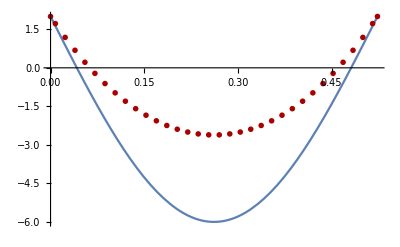

```mathematica
Show[{Plot[2-nn Sin[6 theta],{theta,0,Pi/6}],ListPlot[inter1st[nn],PlotStyle->{PointSize[0.01],Darker[Red]},Epilog->{Line[{{0,nn},{Pi/6,nn}}]}]}]
```

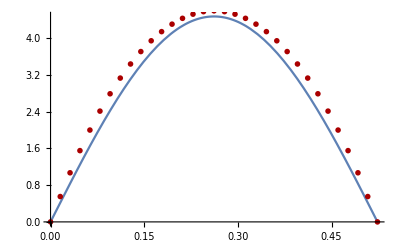

```mathematica
Show[{Plot[4.475516079223348 Sin[6 theta],{theta,0,Pi/6}],ListPlot[inter2nd[nn],PlotStyle->{PointSize[0.01],Darker[Red]},Epilog->{Line[{{0,nn},{Pi/6,nn}}]}]}]
```

```mathematica
inter2nd=intersect[[2;;All;;2]];
```

```mathematica
FullSimplify[Max[Transpose[inter2nd][[2]]]]
N[%]
```

-(π-12 ArcCot[2 √3])/(3 ArcTan[(2 √3)/415])

9.21789

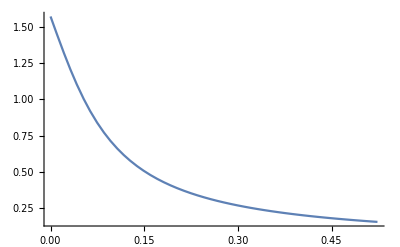

```mathematica
Plot[ArcCot[12 theta],{theta,0,Pi/6}]
```

```mathematica
realError=Map[distinctErrorFunc[#,nn,Round]&,Transpose[inter2nd[nn]][[1]]];
realErrorAvg=Map[((#[[1]]+#[[2]])/2)&,realError];
```

```mathematica
N[realErrorAvg[[30]]]
```

{-1.15389,1.15389}

```mathematica
N[realError[[30]]]
```

{{-1.15541,1.15541},{-1.15237,1.15237}}

```mathematica
realError=Map[distinctErrorFunc[#,nn,Round]&,Transpose[inter2nd[nn]][[1]]];
realErrorAvg=Map[((#[[1]]+#[[2]])/2)&,realError];realInter2ndAvg=Transpose[{Transpose[inter2nd[nn]][[1]],realErrorAvg[[All,1]]}];
realInter2ndOne=Transpose[{Transpose[inter2nd[nn]][[1]],realError[[All,1,1]]}];
realInter2ndTwo=Transpose[{Transpose[inter2nd[nn]][[1]],realError[[All,2,1]]}];
```

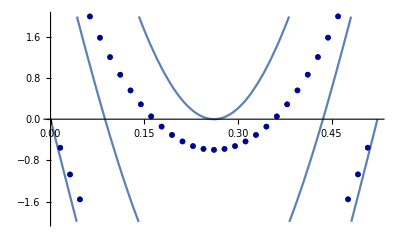

```mathematica
Show[{Plot[fit[θ,nn],{θ,0,Pi/6}],ListPlot[realInter2ndAvg,PlotStyle->{PointSize[0.01],Darker[Red]},Epilog->{Line[{{0,nn},{Pi/6,nn}}]}],ListPlot[realInter2ndOne,PlotStyle->{PointSize[0.01],Darker[Green]},Epilog->{Line[{{0,nn},{Pi/6,nn}}]}],ListPlot[realInter2ndTwo,PlotStyle->{PointSize[0.01],Darker[Blue]},Epilog->{Line[{{0,nn},{Pi/6,nn}}]}]}]
```

```mathematica
fit[θ_,nn_]:= (2-Mod[nn Sin[6 θ]-2,4])
```

```mathematica
fit[θ_]:= (1-2 Quotient[θ,Pi/12])(2-Mod[nn Sin[6 θ]-2,4])
```

```mathematica
(1-2 Quotient[1Pi/24,Pi/12])
```

1

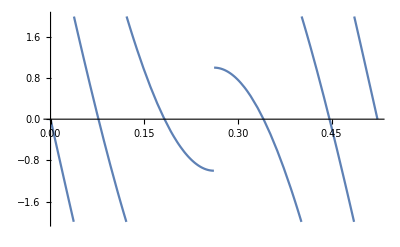

```mathematica
Plot[(1-2 Quotient[theta,Pi/12])(2-Mod[nn Sin[6 theta]-2,4]),{theta,0,Pi/6}]
```

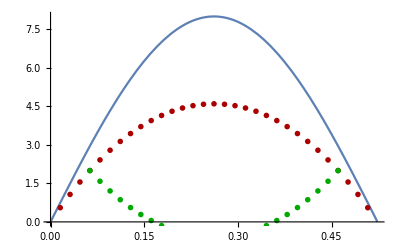

```mathematica
Show[{Plot[nn Sin[6 theta],{theta,0,Pi/6}],
ListPlot[inter2nd[nn],PlotStyle->{PointSize[0.01],Darker[Red]},Epilog->{Line[{{0,nn},{Pi/6,nn}}]}],ListPlot[realInter2ndAvg,PlotStyle->{PointSize[0.01],Darker[Green]},Epilog->{Line[{{0,nn},{Pi/6,nn}}]}]}]
```

One missed point is where both happen to be zero!

```mathematica
intersect=errorMinTheta[4];
TableForm[{intersect[[All,1]],intersect[[All,2]]}]
```

0
0 | (ArcTan[1/(15 √3)] ArcTan[(√3)/17])/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17])
ArcTan[1/(15 √3)]/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17]) | (ArcTan[1/(7 √3)] ArcTan[(√3)/17])/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17])
ArcTan[1/(7 √3)]/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17]) | (ArcTan[(√3)/17] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13])
ArcTan[(√3)/13]/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13]) | (-ArcTan[1/(7 √3)] ArcTan[(√3)/17]+ArcTan[1/(3 √3)] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13])
(-ArcTan[(√3)/17]+ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13]) | (ArcTan[1/(3 √3)]^2-ArcTan[(√3)/17] ArcTan[(√3)/13])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13])
(ArcTan[1/(3 √3)]-ArcTan[(√3)/17])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13]) | ArcTan[1/(3 √3)]
0 | (-ArcTan[1/(3 √3)]^2+ArcTan[5/(11 √3)] ArcTan[(3 √3)/19])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19])
(-ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]) | (-ArcTan[1/(3 √3)] ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19] ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5])
(-ArcTan[1/(3 √3)]+ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5]) | (-ArcTan[5/(11 √3)] ArcTan[(3 √3)/19]+ArcTan[(√3)/5]^2)/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5])
(-ArcTan[(3 √3)/19]+ArcTan[(√3)/5])/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5]) | ArcTan[(√3)/5]
0 | (ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]-ArcTan[(√3)/5]^2)/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5])
(ArcTan[7/(9 √3)]-ArcTan[(√3)/5])/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5]) | (-ArcTan[5/(7 √3)] ArcTan[(√3)/5]+ArcTan[7/(9 √3)] ArcTan[(3 √3)/11])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11])
(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11]) | (-ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]+1/6 π ArcTan[(3 √3)/11])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11])
(π/6-ArcTan[5/(7 √3)])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11]) | (-ArcTan[7/(9 √3)] ArcTan[(3 √3)/11]+1/6 π ArcTan[(7 √3)/23])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23])
(π/6-ArcTan[(3 √3)/11])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23]) | (π^2/36-ArcTan[7/(9 √3)] ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23])
(π/6-ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23]) | π/6
0
0
0 | 1
1 | 2
1 | 3
1 | 3
2 | 4
2 | 4
2 | 5
3 | 6
3 | 6
4 | 6
4 | 7
5 | 7
6 | 8
6 | 8
7 | 8
8 | 9
9

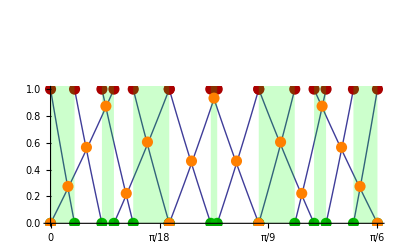

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],ListPlot[intersect[[All,1]],PlotStyle->{PointSize[0.02],Orange}]}]
```

in each range we want to find the point of intersection between the errors for this we need to know which of the individual regions we are in for each of the channels.

```mathematica
Clear[plotErrorWithLinesAndPointsOne,plotErrorWithLinesAndPointsTwo];
plotErrorWithLinesAndPointsOne[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsOne[nn];Show[{Plot[{errOne[θ,nn,IntegerPart]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
plotErrorWithLinesAndPointsTwo[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsTwo[nn];Show[{Plot[{errTwo[θ,nn,IntegerPart]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
```

```mathematica
setupThetaRanges[n_]:=Module[{},
Clear[thetaOneVals,thetaOneMid,thetaOneRange,thetaOneToPoint,thetaTwoVals,thetaTwoMid,thetaTwoRange,thetaTwoToPoint,thetaVals,thetaMid,thetaRange,thetaToPoint];
thetaOneVals=thetaOne[n];
thetaOneMid=(Rest[thetaOneVals]+Most[thetaOneVals])/2;
thetaOneRange=Thread[Inequality[Most[thetaOneVals],Less,Mod[ θ,Pi/6],LessEqual,Rest[thetaOneVals]]];
thetaOneToPoint=Function[{θ},Evaluate[Piecewise[{{0,θ==0},Sequence@@Table[{i,thetaOneRange[[i]]},{i,1,Length[thetaOneRange]}]},Length[thetaOneRange]+1]]];
SetAttributes[thetaOneToPoint,Listable];
thetaTwoVals=thetaTwo[n];
thetaTwoMid=(Rest[thetaTwoVals]+Most[thetaTwoVals])/2;
thetaTwoRange=Thread[Inequality[Most[thetaTwoVals],Less,Mod[ θ,Pi/6],LessEqual,Rest[thetaTwoVals]]];
thetaTwoToPoint=Function[{θ},Evaluate[Piecewise[{{0,θ==0},Sequence@@Table[{i,thetaTwoRange[[i]]},{i,1,Length[thetaTwoRange]}]},Length[thetaOneRange]+1]]];
SetAttributes[thetaTwoToPoint,Listable];
thetaVals=Sort[Union[thetaOneVals,thetaTwoVals],Less];
thetaMid=(Rest[thetaVals]+Most[thetaVals])/2 ;
thetaRange = Thread[Inequality[Most[thetaVals],Less,Mod[ θ,Pi/6],LessEqual,Rest[thetaVals]]];
thetaToPoint=Function[{θ},{thetaOneToPoint[θ],thetaTwoToPoint[θ]}];
SetAttributes[thetaToPoint,Listable];
]
```

Union::normal: Nonatomic expression expected at position 1 in Union[6].

ListPlot::lpn: 6. is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[6].

ListPlot::lpn: 6. is not a list of numbers or pairs of numbers.

Part::partw: Part 2 of ptsOne[6] does not exist.

Part::partw: Part 2 of ptsOne[6.] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: ptsOne[6.] ⟦ 2 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

Show::gcomb: Could not combine the graphics objects in ….

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Union::normal: Nonatomic expression expected at position 1 in Union[6].

General::stop: Further output of Union :: normal will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

Part::partd: Part specification thetaMid ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification thetaMid ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification thetaMid ⟦ 5 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

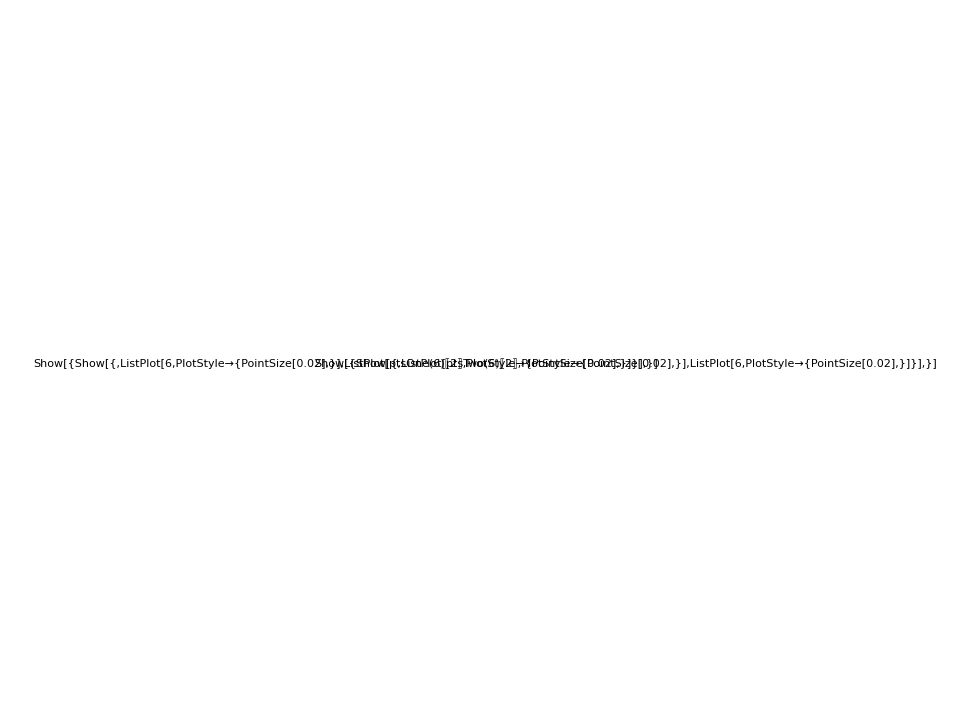

```mathematica
nn=6;GraphicsRow[{Show[{plotErrorWithLinesAndPointsOne[nn],plotRegionsFromList[thetaOne[nn],Yellow,0.4]}],Show[{plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaTwo[nn],Blue,0.2]}],Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]]}]
}]
```

```mathematica
TableForm[N[thetaFunc[6]]]
```

0. | 0.0558146 | 0.114961 | 0.177296 | 0.242564 | 0.310383 | 0.380251 | 0.451555 | 0.523599
0. | 0.0720439 | 0.143348 | 0.213216 | 0.281035 | 0.346302 | 0.408638 | 0.467784 | 0.523599

```mathematica
Column[{Plot[Evaluate[distinctErrorFunc[θ,6,Round][[1]]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All},Epilog->lines[[2]]],
Plot[Evaluate[distinctErrorFunc[θ,6,Round][[2]]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All},Epilog->lines[[1]]],
Plot[Evaluate[distinctErrorFunc[θ,6,Round]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All},Epilog->lines[[1]]]}]
```

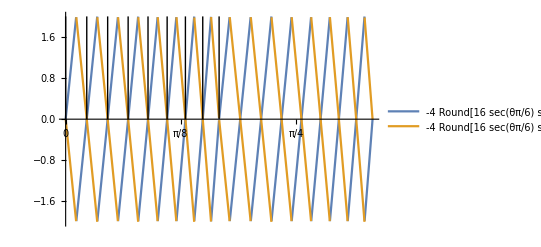
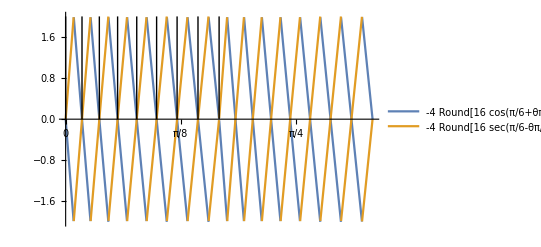
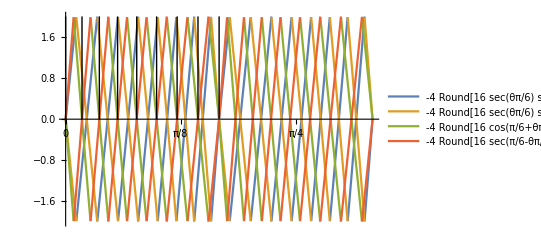

```mathematica
lines=Map[Line[{{#,0},{#,2}}]&,thetaFunc[6],{2}];
Column[{Plot[Evaluate[distinctErrorFunc[θ,6,Round][[1]]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All},Epilog->lines[[2]]],
Plot[Evaluate[distinctErrorFunc[θ,6,Round][[2]]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All},Epilog->lines[[1]]],
Plot[Evaluate[distinctErrorFunc[θ,6,Round]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All},Epilog->lines[[1]]]}]
```

```mathematica
thetaOne[n_]:=Block[{fun},fun[y_]:=ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))];Table[fun[i/(2^(n-1))],{i,2^(n-1),0,-1}]]
thetaTwo[n_]:=Block[{funTwo},funTwo[y_]:=ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))];Table[funTwo[i/(2^(n-1))],{i,0,2^(n-3)}]]
```

to find the zeros we need to solve

√3 2^(n-3) tan(θ)==int(√3 2^(n-3) tan(θ))

2^(n-2) sin(θ) sec(π/6-θ)==int(2^(n-2) sin(θ) sec(π/6-θ))

```mathematica
FullSimplify[Assuming[Element[θ,Reals]&& θ≥ 0 && θ≤ Pi/6,errOne[θ,n,int]==0]];
TraditionalForm[%]
```

2^n (√3 tan(θ)-1)==2 int(2^(n-1) (√3 tan(θ)-1))

```mathematica
FullSimplify[Assuming[Element[θ,Reals]&& θ≥ 0 && θ≤ Pi/6,errTwo[θ,n,int]==0]];
TraditionalForm[%]
```

int(-2^n sin(θ+π/6) sec(θ))+2^n sin(θ+π/6) sec(θ)==0

Solutions are where 
(√3)/2  tan(θ) == m 2^(2-n)    where 0≤ m≤ 2^(n-2)
 sin(θ) sec(π/6-θ) == m 2^(2-n)    where 0≤ m≤ 2^(n-2)

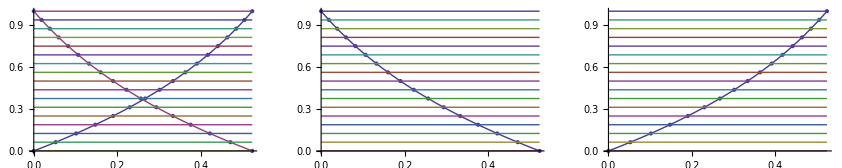

```mathematica
Block[{n=4},dev=Table[m 2^(-n),{m,0,2^n}];
fun=Flatten[{Sec[π/6+θ] Sin[θ],Csc[π/6+θ] Sin[π/6 - θ],dev}];
funA=Flatten[{Csc[π/6+θ] Sin[π/6 - θ],dev}];
funB=Flatten[{Sec[π/6+θ] Sin[θ],dev}];
funcA=Function[{y},ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))],Listable];
funcB=Function[{y},ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))],Listable];
ptsA=Transpose[{funcA[dev],dev}];
ptsB=Transpose[{funcB[dev],dev}];
GraphicsRow[{
Show[{ListPlot[ptsB,PlotStyle->PointSize[Large]],ListPlot[ptsA,PlotStyle->PointSize[Large]],Plot[Evaluate[fun],{θ,0,Pi/6}]}],
Show[{ListPlot[ptsA,PlotStyle->PointSize[Large]],Plot[Evaluate[funA],{θ,0,Pi/6}]}],
Show[{ListPlot[ptsB,PlotStyle->PointSize[Large]],Plot[Evaluate[funB],{θ,0,Pi/6}]}]
}]]
```

```mathematica
Clear[θ]
Simplify[Solve[y== Csc[π/6+θ] Sin[π/6 - θ],θ]]/.C[1]->0
```

{{θ→ArcTan[-(√3 (1+y))/(√(1+y+y^2)),(-1+y)/(√(1+y+y^2))]},{θ→ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))]}}

```mathematica
Clear[θ]
Simplify[Solve[y== Sec[π/6+θ] Sin[θ],θ]]/.C[1]->0
```

{{θ→ArcTan[(-2-y)/(√(1+y+y^2)),-(√3 y)/(√(1+y+y^2))]},{θ→ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))]}}

For a given value of n there are 2^(n - 1) + 1 zeros between 0 and Pi/6

```mathematica
thetaOne[n_]:=Block[{fun},fun[y_]:=ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))];Table[fun[i/(2^(n-1))],{i,2^(n-1),0,-1}]]
thetaTwo[n_]:=Block[{funTwo},funTwo[y_]:=ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))];Table[funTwo[i/(2^(n-1))],{i,0,2^(n-1)}]]
```

```mathematica
thetaOne[n_]:=Block[{fun},fun[y_]:=ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))];Table[fun[i/(2^(n))],{i,2^(n),0,-1}]]
thetaTwo[n_]:=Block[{funTwo},funTwo[y_]:=ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))];Table[funTwo[i/(2^(n))],{i,0,2^(n)}]]
```

```mathematica
(scale["fR","qR"] qR[θ,n]-fR[θ]).(2^n RGBCube["RGB"])
```

(-(Piecewise[{{{{1,1,1},{-Sec[θ] Sin[π/6+θ],1,-Sec[θ] Sin[π/6-θ]},{-Cos[π/6+θ] Sec[π/6-θ],-Sec[π/6-θ] Sin[θ],1}}, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {{{1,1,1},{1,-Cos[θ] Csc[π/6+θ],Csc[π/6+θ] Sin[π/6-θ]},{-Cos[π/6+θ] Sec[π/6-θ],-Sec[π/6-θ] Sin[θ],1}}, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {{{1,1,1},{1,-Cos[θ] Csc[π/6+θ],Csc[π/6+θ] Sin[π/6-θ]},{Cos[π/6+θ] Csc[θ],1,-Cos[π/6-θ] Csc[θ]}}, π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {{{1,1,1},{Csc[π/6-θ] Sin[π/6+θ],-Cos[θ] Csc[π/6-θ],1},{Cos[π/6+θ] Csc[θ],1,-Cos[π/6-θ] Csc[θ]}}, π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {{{1,1,1},{Csc[π/6-θ] Sin[π/6+θ],-Cos[θ] Csc[π/6-θ],1},{1,Sec[π/6+θ] Sin[θ],-Cos[π/6-θ] Sec[π/6+θ]}}, (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {{{1,1,1},{-Sec[θ] Sin[π/6+θ],1,-Sec[θ] Sin[π/6-θ]},{1,Sec[π/6+θ] Sin[θ],-Cos[π/6-θ] Sec[π/6+θ]}}, (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}])+(Piecewise[{{{{1,1,1},{-Round[2^(-2+n) Sec[θ] Sin[π/6+θ]],Round[2^(-2+n)],-Round[2^(-2+n) Sec[θ] Sin[π/6-θ]]},{-Round[2^(-2+n) Cos[π/6+θ] Sec[π/6-θ]],-Round[2^(-2+n) Sec[π/6-θ] Sin[θ]],Round[2^(-2+n)]}}, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {{{1,1,1},{Round[2^(-2+n)],-Round[2^(-2+n) Cos[θ] Csc[π/6+θ]],Round[2^(-2+n) Csc[π/6+θ] Sin[π/6-θ]]},{-Round[2^(-2+n) Cos[π/6+θ] Sec[π/6-θ]],-Round[2^(-2+n) Sec[π/6-θ] Sin[θ]],Round[2^(-2+n)]}}, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {{{1,1,1},{Round[2^(-2+n)],-Round[2^(-2+n) Cos[θ] Csc[π/6+θ]],Round[2^(-2+n) Csc[π/6+θ] Sin[π/6-θ]]},{Round[2^(-2+n) Cos[π/6+θ] Csc[θ]],Round[2^(-2+n)],-Round[2^(-2+n) Cos[π/6-θ] Csc[θ]]}}, π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {{{1,1,1},{Round[2^(-2+n) Csc[π/6-θ] Sin[π/6+θ]],-Round[2^(-2+n) Cos[θ] Csc[π/6-θ]],Round[2^(-2+n)]},{Round[2^(-2+n) Cos[π/6+θ] Csc[θ]],Round[2^(-2+n)],-Round[2^(-2+n) Cos[π/6-θ] Csc[θ]]}}, π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {{{1,1,1},{Round[2^(-2+n) Csc[π/6-θ] Sin[π/6+θ]],-Round[2^(-2+n) Cos[θ] Csc[π/6-θ]],Round[2^(-2+n)]},{Round[2^(-2+n)],Round[2^(-2+n) Sec[π/6+θ] Sin[θ]],-Round[2^(-2+n) Cos[π/6-θ] Sec[π/6+θ]]}}, (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {{{1,1,1},{-Round[2^(-2+n) Sec[θ] Sin[π/6+θ]],Round[2^(-2+n)],-Round[2^(-2+n) Sec[θ] Sin[π/6-θ]]},{Round[2^(-2+n)],Round[2^(-2+n) Sec[π/6+θ] Sin[θ]],-Round[2^(-2+n) Cos[π/6-θ] Sec[π/6+θ]]}}, (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]) scale[fR,qR]).{{0,2^n,2^n,0,0,0,2^n,2^n},{0,0,2^n,2^n,2^n,0,0,2^n},{0,0,0,0,2^n,2^n,2^n,2^n}}

```mathematica
fRError
```

Function[{θ,n,round},Piecewise[{{{{0,0,0},{-2^-n round[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],0,-2^-n round[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]},{-2^-n round[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ],-2^-n round[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ],0}}, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {{{0,0,0},{0,-Cos[θ] Csc[π/6+θ]-2^-n round[-2^n Cos[θ] Csc[π/6+θ]],-2^-n round[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]},{-2^-n round[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ],-2^-n round[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ],0}}, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {{{0,0,0},{0,-Cos[θ] Csc[π/6+θ]-2^-n round[-2^n Cos[θ] Csc[π/6+θ]],-2^-n round[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]},{Cos[π/6+θ] Csc[θ]-2^-n round[2^n Cos[π/6+θ] Csc[θ]],0,-Cos[π/6-θ] Csc[θ]-2^-n round[-2^n Cos[π/6-θ] Csc[θ]]}}, π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {{{0,0,0},{-2^-n round[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ],-Cos[θ] Csc[π/6-θ]-2^-n round[-2^n Cos[θ] Csc[π/6-θ]],0},{Cos[π/6+θ] Csc[θ]-2^-n round[2^n Cos[π/6+θ] Csc[θ]],0,-Cos[π/6-θ] Csc[θ]-2^-n round[-2^n Cos[π/6-θ] Csc[θ]]}}, π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {{{0,0,0},{-2^-n round[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ],-Cos[θ] Csc[π/6-θ]-2^-n round[-2^n Cos[θ] Csc[π/6-θ]],0},{0,-2^-n round[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ],-2^-n round[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]}}, (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {{{0,0,0},{-2^-n round[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],0,-2^-n round[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]},{0,-2^-n round[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ],-2^-n round[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]}}, (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]]

```mathematica
fRError=Function[{θ,n,round},Evaluate[simpleError[θ,n,fR,round]]];
fRErrorCube=Function[{θ,n,round},Evaluate[ApplyToPiecewise[#.(2^n RGBCube["RGB"])&,fRError[θ,n,round]]]];
```

```mathematica
Row[{"fRError[θ] = fR[θ]- Approx[fR[θ]] = ",ApplyToPiecewise[ MatrixForm,fRError[θ,n,Round]]}]
```

fRError[θ] = fR[θ]- Approx[fR[θ]] = Piecewise[{{(0 | 0 | 0
2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ] | 0 | 2^-n Round[2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]
2^-n Round[2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ] | 2^-n Round[2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ] | 0), 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {(0 | 0 | 0
0 | -Cos[θ] Csc[π/6+θ]+2^-n Round[2^n Cos[θ] Csc[π/6+θ]] | -2^-n Round[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]
2^-n Round[2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ] | 2^-n Round[2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ] | 0), π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {(0 | 0 | 0
0 | -Cos[θ] Csc[π/6+θ]+2^-n Round[2^n Cos[θ] Csc[π/6+θ]] | -2^-n Round[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]
Cos[π/6+θ] Csc[θ]-2^-n Round[2^n Cos[π/6+θ] Csc[θ]] | 0 | -Cos[π/6-θ] Csc[θ]+2^-n Round[2^n Cos[π/6-θ] Csc[θ]]), π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {(0 | 0 | 0
-2^-n Round[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ]+2^-n Round[2^n Cos[θ] Csc[π/6-θ]] | 0
Cos[π/6+θ] Csc[θ]-2^-n Round[2^n Cos[π/6+θ] Csc[θ]] | 0 | -Cos[π/6-θ] Csc[θ]+2^-n Round[2^n Cos[π/6-θ] Csc[θ]]), π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {(0 | 0 | 0
-2^-n Round[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ]+2^-n Round[2^n Cos[θ] Csc[π/6-θ]] | 0
0 | -2^-n Round[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ] | 2^-n Round[2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]), (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {(0 | 0 | 0
2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ] | 0 | 2^-n Round[2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]
0 | -2^-n Round[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ] | 2^-n Round[2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]), (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

As expected the second and third rows have one zero error element each meaning that there are three possible combinations corresponding to corner maximal errors.

```mathematica
(fRError[θ,n,Round][[1,1,1]])/. 0->Sequence[]
```

{{},{2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]},{2^-n Round[2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ],2^-n Round[2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]}}

```mathematica
nonZeroErrors=Function[{θ,n,round},Evaluate[ApplyToPiecewise[ (((#)/. 0->Sequence[])/. List[]-> List[0,0])&,fRError[θ,n,Round]]]];
ApplyToPiecewise[ MatrixForm,nonZeroErrors[θ,n,Round]]
```

Piecewise[{{(0 | 0
2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ] | 2^-n Round[2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]
2^-n Round[2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ] | 2^-n Round[2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]), 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {(0 | 0
-Cos[θ] Csc[π/6+θ]+2^-n Round[2^n Cos[θ] Csc[π/6+θ]] | -2^-n Round[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]
2^-n Round[2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ] | 2^-n Round[2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]), π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {(0 | 0
-Cos[θ] Csc[π/6+θ]+2^-n Round[2^n Cos[θ] Csc[π/6+θ]] | -2^-n Round[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]
Cos[π/6+θ] Csc[θ]-2^-n Round[2^n Cos[π/6+θ] Csc[θ]] | -Cos[π/6-θ] Csc[θ]+2^-n Round[2^n Cos[π/6-θ] Csc[θ]]), π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {(0 | 0
-2^-n Round[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ]+2^-n Round[2^n Cos[θ] Csc[π/6-θ]]
Cos[π/6+θ] Csc[θ]-2^-n Round[2^n Cos[π/6+θ] Csc[θ]] | -Cos[π/6-θ] Csc[θ]+2^-n Round[2^n Cos[π/6-θ] Csc[θ]]), π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {(0 | 0
-2^-n Round[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ]+2^-n Round[2^n Cos[θ] Csc[π/6-θ]]
-2^-n Round[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ] | 2^-n Round[2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]), (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {(0 | 0
2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ] | 2^-n Round[2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]
-2^-n Round[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ] | 2^-n Round[2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]), (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

```mathematica
Evaluate[sumError[θ,5,Round]]
```

Piecewise[{{{0,0,1/32 (-32+Round[(64 Sin[θ])/(√3 Cos[θ]+Sin[θ])]+Round[32-(64 Sin[θ])/(√3 Cos[θ]+Sin[θ])])}, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {{0,1/32 (-32+Round[(64 Cos[θ])/(Cos[θ]+√3 Sin[θ])]+Round[32-(64 Cos[θ])/(Cos[θ]+√3 Sin[θ])]),1/32 (-32+Round[(64 Sin[θ])/(√3 Cos[θ]+Sin[θ])]+Round[32-(64 Sin[θ])/(√3 Cos[θ]+Sin[θ])])}, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {{0,1/32 (-32+Round[(64 Cos[θ])/(Cos[θ]+√3 Sin[θ])]+Round[32-(64 Cos[θ])/(Cos[θ]+√3 Sin[θ])]),0}, π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {{0,1/32 (-32+Round[(64 Cos[θ])/(Cos[θ]-√3 Sin[θ])]+Round[32+64/(-1+√3 Tan[θ])]),0}, π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {{0,1/32 (-32+Round[(64 Cos[θ])/(Cos[θ]-√3 Sin[θ])]+Round[32+64/(-1+√3 Tan[θ])]),1/32 (-32+Round[64/(1-√3 Cot[θ])]+Round[32+64/(-1+√3 Cot[θ])])}, (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {{0,0,1/32 (-32+Round[64/(1-√3 Cot[θ])]+Round[32+64/(-1+√3 Cot[θ])])}, (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

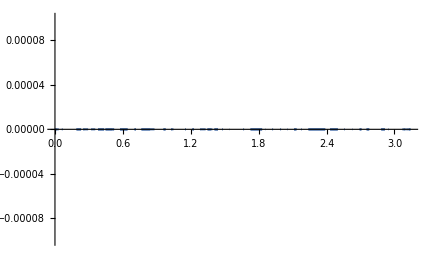

```mathematica
sumError=Function[{θ,n,round},ApplyToPiecewise[ FullSimplify[(#.{1,1})]&,nonZeroErrors[θ,n,Round]]];
Plot[Evaluate[sumError[θ,5,Round]],{θ,0,Pi},PlotLegends->"Expressions",PlotRange->{{0,Pi},{-0.0001,0.0001}}]
```

```mathematica
Evaluate[nonZeroErrors[θ,3,Round]]
```

Piecewise[{{{{0,0},{1/8 Round[8 Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],1/8 Round[8 Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]},{1/8 Round[8 Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ],1/8 Round[8 Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]}}, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {{{0,0},{-Cos[θ] Csc[π/6+θ]+1/8 Round[8 Cos[θ] Csc[π/6+θ]],-1/8 Round[8 Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]},{1/8 Round[8 Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ],1/8 Round[8 Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]}}, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {{{0,0},{-Cos[θ] Csc[π/6+θ]+1/8 Round[8 Cos[θ] Csc[π/6+θ]],-1/8 Round[8 Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]},{Cos[π/6+θ] Csc[θ]-1/8 Round[8 Cos[π/6+θ] Csc[θ]],-Cos[π/6-θ] Csc[θ]+1/8 Round[8 Cos[π/6-θ] Csc[θ]]}}, π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {{{0,0},{-1/8 Round[8 Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ],-Cos[θ] Csc[π/6-θ]+1/8 Round[8 Cos[θ] Csc[π/6-θ]]},{Cos[π/6+θ] Csc[θ]-1/8 Round[8 Cos[π/6+θ] Csc[θ]],-Cos[π/6-θ] Csc[θ]+1/8 Round[8 Cos[π/6-θ] Csc[θ]]}}, π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {{{0,0},{-1/8 Round[8 Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ],-Cos[θ] Csc[π/6-θ]+1/8 Round[8 Cos[θ] Csc[π/6-θ]]},{-1/8 Round[8 Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ],1/8 Round[8 Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]}}, (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {{{0,0},{1/8 Round[8 Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],1/8 Round[8 Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]},{-1/8 Round[8 Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ],1/8 Round[8 Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]}}, (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

```mathematica
line1=Function[{θ,n,round},ApplyToPiecewise[#[[2,1]]&,nonZeroErrors[θ,n,round]]];
line2=Function[{θ,n,round},ApplyToPiecewise[#[[3,1]]&,nonZeroErrors[θ,n,Round]]];
line3=Function[{θ,n,round},ApplyToPiecewise[#[[2,2]]&,nonZeroErrors[θ,n,Round]]];
line4=Function[{θ,n,round},ApplyToPiecewise[#[[3,2]]&,nonZeroErrors[θ,n,Round]]];
```

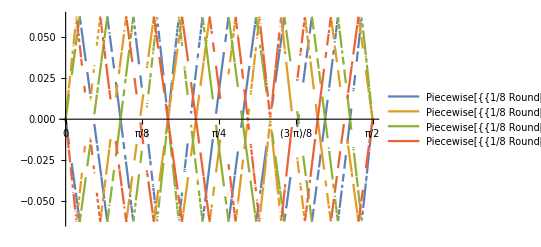

```mathematica
Plot[Evaluate[{line1[θ,3,Round],line2[θ,3,Round],line3[θ,3,Round],line4[θ,3,Round]}],{θ,0,Pi/2},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All}]
```

```mathematica
nonZeroErrors[θ,n,Round]
```

Piecewise[{{{{0,0},{2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]},{2^-n Round[2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ],2^-n Round[2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]}}, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {{{0,0},{-Cos[θ] Csc[π/6+θ]+2^-n Round[2^n Cos[θ] Csc[π/6+θ]],-2^-n Round[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]},{2^-n Round[2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ],2^-n Round[2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]}}, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {{{0,0},{-Cos[θ] Csc[π/6+θ]+2^-n Round[2^n Cos[θ] Csc[π/6+θ]],-2^-n Round[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]},{Cos[π/6+θ] Csc[θ]-2^-n Round[2^n Cos[π/6+θ] Csc[θ]],-Cos[π/6-θ] Csc[θ]+2^-n Round[2^n Cos[π/6-θ] Csc[θ]]}}, π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {{{0,0},{-2^-n Round[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ],-Cos[θ] Csc[π/6-θ]+2^-n Round[2^n Cos[θ] Csc[π/6-θ]]},{Cos[π/6+θ] Csc[θ]-2^-n Round[2^n Cos[π/6+θ] Csc[θ]],-Cos[π/6-θ] Csc[θ]+2^-n Round[2^n Cos[π/6-θ] Csc[θ]]}}, π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {{{0,0},{-2^-n Round[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ],-Cos[θ] Csc[π/6-θ]+2^-n Round[2^n Cos[θ] Csc[π/6-θ]]},{-2^-n Round[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ],2^-n Round[2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]}}, (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {{{0,0},{2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]},{-2^-n Round[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ],2^-n Round[2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]}}, (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

Check that there are only 4 distinct functions which repeat every Pi/6 intival

```mathematica
shiftedError=Function[{θ,n,round},Evaluate[Map[Simplify[#]&,Table[(nonZeroErrors[θ,n,Round][[1,i+1,1]])/.θ-> θ+i Pi/6 ,{i,0,5}],3]]];
Map[MatrixForm,shiftedError[θ,n,round]]
Map[Union[Flatten[#]]&,shiftedError[θ,n,round]]
Thread[Equal[Most[%],Rest[%]]]
```

{(0 | 0
2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ] | 2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ])
2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)] | 2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ]),(0 | 0
2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)] | 2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ]
2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ]) | 2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]),(0 | 0
2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ]) | 2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]
2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ] | 2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)]),(0 | 0
2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)] | 2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ]
2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ] | 2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ])),(0 | 0
2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ]) | 2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]
2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)] | 2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ]),(0 | 0
2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ] | 2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)]
2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ]) | 2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ])}

{{0,2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)],2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ],2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ])},{0,2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)],2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ],2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ])},{0,2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)],2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ],2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ])},{0,2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)],2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ],2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ])},{0,2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)],2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ],2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ])},{0,2^-n Round[2^n Cos[π/6+θ] Sec[1/6 (π-6 θ)]]-Cos[π/6+θ] Sec[1/6 (π-6 θ)],2^-n Round[2^n Sec[1/6 (π-6 θ)] Sin[θ]]-Sec[1/6 (π-6 θ)] Sin[θ],2^-n Round[2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ],2^-n Round[2^n Sec[θ] Sin[1/6 (π-6 θ)]]+1/2 (-1+√3 Tan[θ])}}

True

```mathematica
distinctErrorFunc=Function[{θ,n,round},Evaluate[nonZeroErrors[θ,n,round][[1,1,1,{2,3}]]/. θ -> Mod[θ,Pi/6]]];
```

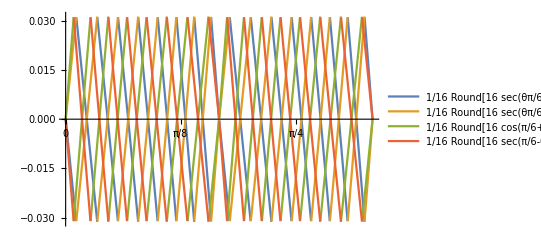

```mathematica
Plot[Evaluate[distinctErrorFunc[θ,4,Round]],{θ,0,Pi/3},PlotLegends->"Expressions",Ticks->{PiTicks[0,Pi/2,12],All}]
```

```mathematica
ApplyToPiecewise[ MatrixForm,fRError[θ,n,Round]]
```

```mathematica
simpleError[θ,n,ffR,round]
```

-ffR[θ]+2^-n round[2^n ffR[θ]]

```mathematica
RGBCube["RGB"]
```

{{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}}

```mathematica
ApplyToPiecewise[ MatrixForm[#]&,fR[θ]]
```

Piecewise[{{(1 | 1 | 1
-Sec[θ] Sin[π/6+θ] | 1 | -Sec[θ] Sin[π/6-θ]
-Cos[π/6+θ] Sec[π/6-θ] | -Sec[π/6-θ] Sin[θ] | 1), 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {(1 | 1 | 1
1 | -Cos[θ] Csc[π/6+θ] | Csc[π/6+θ] Sin[π/6-θ]
-Cos[π/6+θ] Sec[π/6-θ] | -Sec[π/6-θ] Sin[θ] | 1), π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {(1 | 1 | 1
1 | -Cos[θ] Csc[π/6+θ] | Csc[π/6+θ] Sin[π/6-θ]
Cos[π/6+θ] Csc[θ] | 1 | -Cos[π/6-θ] Csc[θ]), π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {(1 | 1 | 1
Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ] | 1
Cos[π/6+θ] Csc[θ] | 1 | -Cos[π/6-θ] Csc[θ]), π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {(1 | 1 | 1
Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ] | 1
1 | Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ]), (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {(1 | 1 | 1
-Sec[θ] Sin[π/6+θ] | 1 | -Sec[θ] Sin[π/6-θ]
1 | Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ]), (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

```mathematica
ApplyToPiecewise[ MatrixForm[#.RGBCube["RGB"]]&,fR[θ]]
```

Piecewise[{{(0 | 1 | 2 | 1 | 2 | 1 | 2 | 3
0 | -Sec[θ] Sin[π/6+θ] | 1-Sec[θ] Sin[π/6+θ] | 1 | 1-Sec[θ] Sin[π/6-θ] | -Sec[θ] Sin[π/6-θ] | -Sec[θ] Sin[π/6-θ]-Sec[θ] Sin[π/6+θ] | 1-Sec[θ] Sin[π/6-θ]-Sec[θ] Sin[π/6+θ]
0 | -Cos[π/6+θ] Sec[π/6-θ] | -Cos[π/6+θ] Sec[π/6-θ]-Sec[π/6-θ] Sin[θ] | -Sec[π/6-θ] Sin[θ] | 1-Sec[π/6-θ] Sin[θ] | 1 | 1-Cos[π/6+θ] Sec[π/6-θ] | 1-Cos[π/6+θ] Sec[π/6-θ]-Sec[π/6-θ] Sin[θ]), 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {(0 | 1 | 2 | 1 | 2 | 1 | 2 | 3
0 | 1 | 1-Cos[θ] Csc[π/6+θ] | -Cos[θ] Csc[π/6+θ] | -Cos[θ] Csc[π/6+θ]+Csc[π/6+θ] Sin[π/6-θ] | Csc[π/6+θ] Sin[π/6-θ] | 1+Csc[π/6+θ] Sin[π/6-θ] | 1-Cos[θ] Csc[π/6+θ]+Csc[π/6+θ] Sin[π/6-θ]
0 | -Cos[π/6+θ] Sec[π/6-θ] | -Cos[π/6+θ] Sec[π/6-θ]-Sec[π/6-θ] Sin[θ] | -Sec[π/6-θ] Sin[θ] | 1-Sec[π/6-θ] Sin[θ] | 1 | 1-Cos[π/6+θ] Sec[π/6-θ] | 1-Cos[π/6+θ] Sec[π/6-θ]-Sec[π/6-θ] Sin[θ]), π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {(0 | 1 | 2 | 1 | 2 | 1 | 2 | 3
0 | 1 | 1-Cos[θ] Csc[π/6+θ] | -Cos[θ] Csc[π/6+θ] | -Cos[θ] Csc[π/6+θ]+Csc[π/6+θ] Sin[π/6-θ] | Csc[π/6+θ] Sin[π/6-θ] | 1+Csc[π/6+θ] Sin[π/6-θ] | 1-Cos[θ] Csc[π/6+θ]+Csc[π/6+θ] Sin[π/6-θ]
0 | Cos[π/6+θ] Csc[θ] | 1+Cos[π/6+θ] Csc[θ] | 1 | 1-Cos[π/6-θ] Csc[θ] | -Cos[π/6-θ] Csc[θ] | -Cos[π/6-θ] Csc[θ]+Cos[π/6+θ] Csc[θ] | 1-Cos[π/6-θ] Csc[θ]+Cos[π/6+θ] Csc[θ]), π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {(0 | 1 | 2 | 1 | 2 | 1 | 2 | 3
0 | Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ]+Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ] | 1-Cos[θ] Csc[π/6-θ] | 1 | 1+Csc[π/6-θ] Sin[π/6+θ] | 1-Cos[θ] Csc[π/6-θ]+Csc[π/6-θ] Sin[π/6+θ]
0 | Cos[π/6+θ] Csc[θ] | 1+Cos[π/6+θ] Csc[θ] | 1 | 1-Cos[π/6-θ] Csc[θ] | -Cos[π/6-θ] Csc[θ] | -Cos[π/6-θ] Csc[θ]+Cos[π/6+θ] Csc[θ] | 1-Cos[π/6-θ] Csc[θ]+Cos[π/6+θ] Csc[θ]), π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {(0 | 1 | 2 | 1 | 2 | 1 | 2 | 3
0 | Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ]+Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ] | 1-Cos[θ] Csc[π/6-θ] | 1 | 1+Csc[π/6-θ] Sin[π/6+θ] | 1-Cos[θ] Csc[π/6-θ]+Csc[π/6-θ] Sin[π/6+θ]
0 | 1 | 1+Sec[π/6+θ] Sin[θ] | Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ]+Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ] | 1-Cos[π/6-θ] Sec[π/6+θ] | 1-Cos[π/6-θ] Sec[π/6+θ]+Sec[π/6+θ] Sin[θ]), (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {(0 | 1 | 2 | 1 | 2 | 1 | 2 | 3
0 | -Sec[θ] Sin[π/6+θ] | 1-Sec[θ] Sin[π/6+θ] | 1 | 1-Sec[θ] Sin[π/6-θ] | -Sec[θ] Sin[π/6-θ] | -Sec[θ] Sin[π/6-θ]-Sec[θ] Sin[π/6+θ] | 1-Sec[θ] Sin[π/6-θ]-Sec[θ] Sin[π/6+θ]
0 | 1 | 1+Sec[π/6+θ] Sin[θ] | Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ]+Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ] | 1-Cos[π/6-θ] Sec[π/6+θ] | 1-Cos[π/6-θ] Sec[π/6+θ]+Sec[π/6+θ] Sin[θ]), (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

```mathematica
ApplyToPiecewise[MatrixFormCubeColor[#,0.7]&,fRErrorCube[θ,n,int]]
```

Piecewise[{{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]) | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]) | 0 | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]) | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]) | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ])+2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]) | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ])+2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ])
0 | 2^n (-2^-n int[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ]) | 2^n (-2^-n int[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ])+2^n (-2^-n int[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]) | 2^n (-2^-n int[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]) | 2^n (-2^-n int[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]) | 0 | 2^n (-2^-n int[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ]) | 2^n (-2^-n int[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ])+2^n (-2^-n int[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ])), 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2^n (-Cos[θ] Csc[π/6+θ]-2^-n int[-2^n Cos[θ] Csc[π/6+θ]]) | 2^n (-Cos[θ] Csc[π/6+θ]-2^-n int[-2^n Cos[θ] Csc[π/6+θ]]) | 2^n (-Cos[θ] Csc[π/6+θ]-2^-n int[-2^n Cos[θ] Csc[π/6+θ]])+2^n (-2^-n int[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-2^-n int[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-2^-n int[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-Cos[θ] Csc[π/6+θ]-2^-n int[-2^n Cos[θ] Csc[π/6+θ]])+2^n (-2^-n int[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ])
0 | 2^n (-2^-n int[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ]) | 2^n (-2^-n int[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ])+2^n (-2^-n int[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]) | 2^n (-2^-n int[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]) | 2^n (-2^-n int[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ]) | 0 | 2^n (-2^-n int[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ]) | 2^n (-2^-n int[-2^n Cos[π/6+θ] Sec[π/6-θ]]-Cos[π/6+θ] Sec[π/6-θ])+2^n (-2^-n int[-2^n Sec[π/6-θ] Sin[θ]]-Sec[π/6-θ] Sin[θ])), π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2^n (-Cos[θ] Csc[π/6+θ]-2^-n int[-2^n Cos[θ] Csc[π/6+θ]]) | 2^n (-Cos[θ] Csc[π/6+θ]-2^-n int[-2^n Cos[θ] Csc[π/6+θ]]) | 2^n (-Cos[θ] Csc[π/6+θ]-2^-n int[-2^n Cos[θ] Csc[π/6+θ]])+2^n (-2^-n int[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-2^-n int[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-2^-n int[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-Cos[θ] Csc[π/6+θ]-2^-n int[-2^n Cos[θ] Csc[π/6+θ]])+2^n (-2^-n int[2^n Csc[π/6+θ] Sin[π/6-θ]]+Csc[π/6+θ] Sin[π/6-θ])
0 | 2^n (Cos[π/6+θ] Csc[θ]-2^-n int[2^n Cos[π/6+θ] Csc[θ]]) | 2^n (Cos[π/6+θ] Csc[θ]-2^-n int[2^n Cos[π/6+θ] Csc[θ]]) | 0 | 2^n (-Cos[π/6-θ] Csc[θ]-2^-n int[-2^n Cos[π/6-θ] Csc[θ]]) | 2^n (-Cos[π/6-θ] Csc[θ]-2^-n int[-2^n Cos[π/6-θ] Csc[θ]]) | 2^n (-Cos[π/6-θ] Csc[θ]-2^-n int[-2^n Cos[π/6-θ] Csc[θ]])+2^n (Cos[π/6+θ] Csc[θ]-2^-n int[2^n Cos[π/6+θ] Csc[θ]]) | 2^n (-Cos[π/6-θ] Csc[θ]-2^-n int[-2^n Cos[π/6-θ] Csc[θ]])+2^n (Cos[π/6+θ] Csc[θ]-2^-n int[2^n Cos[π/6+θ] Csc[θ]])), π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^-n int[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-Cos[θ] Csc[π/6-θ]-2^-n int[-2^n Cos[θ] Csc[π/6-θ]])+2^n (-2^-n int[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-Cos[θ] Csc[π/6-θ]-2^-n int[-2^n Cos[θ] Csc[π/6-θ]]) | 2^n (-Cos[θ] Csc[π/6-θ]-2^-n int[-2^n Cos[θ] Csc[π/6-θ]]) | 0 | 2^n (-2^-n int[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-Cos[θ] Csc[π/6-θ]-2^-n int[-2^n Cos[θ] Csc[π/6-θ]])+2^n (-2^-n int[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ])
0 | 2^n (Cos[π/6+θ] Csc[θ]-2^-n int[2^n Cos[π/6+θ] Csc[θ]]) | 2^n (Cos[π/6+θ] Csc[θ]-2^-n int[2^n Cos[π/6+θ] Csc[θ]]) | 0 | 2^n (-Cos[π/6-θ] Csc[θ]-2^-n int[-2^n Cos[π/6-θ] Csc[θ]]) | 2^n (-Cos[π/6-θ] Csc[θ]-2^-n int[-2^n Cos[π/6-θ] Csc[θ]]) | 2^n (-Cos[π/6-θ] Csc[θ]-2^-n int[-2^n Cos[π/6-θ] Csc[θ]])+2^n (Cos[π/6+θ] Csc[θ]-2^-n int[2^n Cos[π/6+θ] Csc[θ]]) | 2^n (-Cos[π/6-θ] Csc[θ]-2^-n int[-2^n Cos[π/6-θ] Csc[θ]])+2^n (Cos[π/6+θ] Csc[θ]-2^-n int[2^n Cos[π/6+θ] Csc[θ]])), π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^-n int[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-Cos[θ] Csc[π/6-θ]-2^-n int[-2^n Cos[θ] Csc[π/6-θ]])+2^n (-2^-n int[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-Cos[θ] Csc[π/6-θ]-2^-n int[-2^n Cos[θ] Csc[π/6-θ]]) | 2^n (-Cos[θ] Csc[π/6-θ]-2^-n int[-2^n Cos[θ] Csc[π/6-θ]]) | 0 | 2^n (-2^-n int[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-Cos[θ] Csc[π/6-θ]-2^-n int[-2^n Cos[θ] Csc[π/6-θ]])+2^n (-2^-n int[2^n Csc[π/6-θ] Sin[π/6+θ]]+Csc[π/6-θ] Sin[π/6+θ])
0 | 0 | 2^n (-2^-n int[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ])+2^n (-2^-n int[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]) | 2^n (-2^-n int[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]) | 2^n (-2^-n int[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ])+2^n (-2^-n int[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ])), (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]) | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]) | 0 | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]) | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]) | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ])+2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]) | 2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ])+2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ])
0 | 0 | 2^n (-2^-n int[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ])+2^n (-2^-n int[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]) | 2^n (-2^-n int[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ]) | 2^n (-2^-n int[-2^n Cos[π/6-θ] Sec[π/6+θ]]-Cos[π/6-θ] Sec[π/6+θ])+2^n (-2^-n int[2^n Sec[π/6+θ] Sin[θ]]+Sec[π/6+θ] Sin[θ])), (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

```mathematica
fRErrorCube[θ,n,int][[1,1,1,2]]
```

{0,2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]),2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]),0,2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]),2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ]),2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ])+2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ]),2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ])+2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ])}

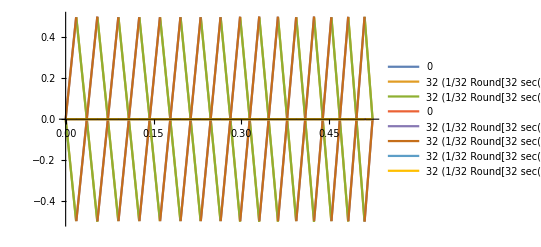

```mathematica
plt1=Plot[Evaluate[fRErrorCube[θ,5,Round][[1,1,1,2]]],{θ,0,Pi/6},PlotLegends->"Expressions"]
```

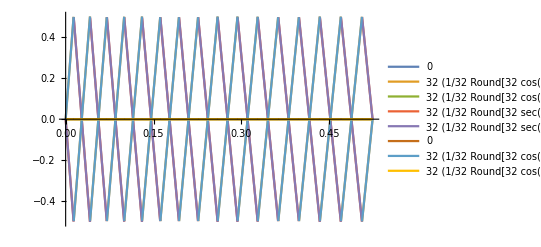

```mathematica
plt2=Plot[Evaluate[fRErrorCube[θ,5,Round][[1,1,1,3]]],{θ,0,Pi/6},PlotLegends->"Expressions"]
```

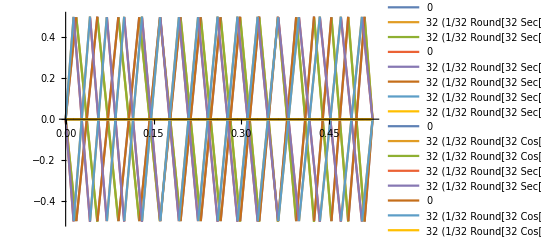

```mathematica
Show[plt1,plt2]
```

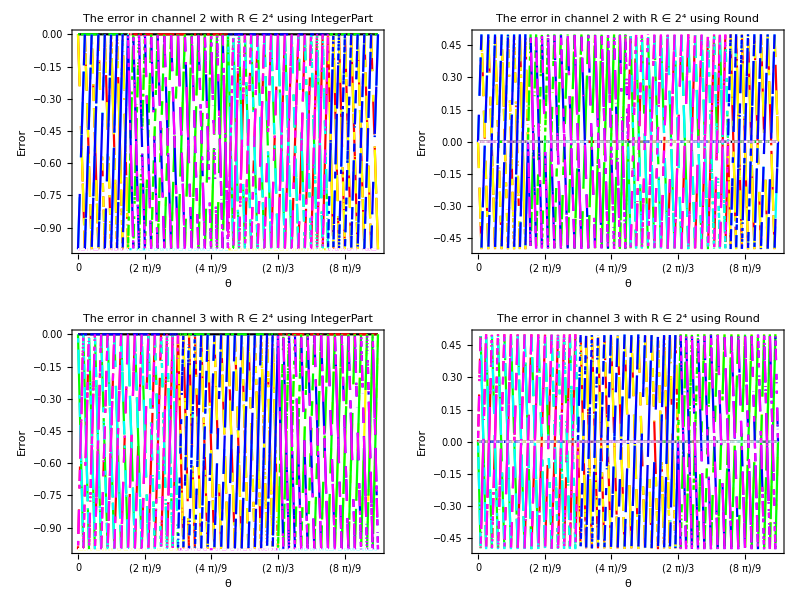

```mathematica
simpleErrorPlot[{0,Pi},fRErrorCube,4]
```

The base function for the channel error

```mathematica
2^n (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ])  2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ])
```

```mathematica
Clear[errOne,errTwo];
```

```mathematica
errOne[θ_,n_,int_]:=(2^n) (-2^-n int[-2^n Sec[θ] Sin[π/6-θ]]-Sec[θ] Sin[π/6-θ])
errTwo[θ_,n_,int_]:=2^n (-2^-n int[-2^n Sec[θ] Sin[π/6+θ]]-Sec[θ] Sin[π/6+θ])
```

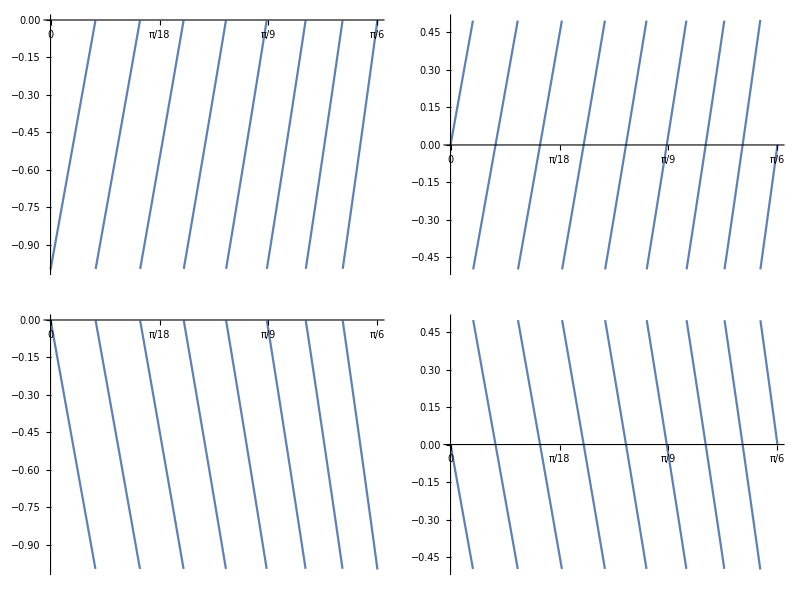

```mathematica
Grid[{{Plot[errOne[θ,4,IntegerPart],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],Plot[errOne[θ,4,Round],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}]},
{Plot[errTwo[θ,4,IntegerPart],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],Plot[errTwo[θ,4,Round],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}]}}]
```

```mathematica
{FullSimplify[errOne[θ,n,int]==0],FullSimplify[errTwo[θ,n,int]==0]}
```

{2^n (-1+√3 Tan[θ])==2 int[2^(-1+n) (-1+√3 Tan[θ])],int[-2^n Sec[θ] Sin[π/6+θ]]+2^n Sec[θ] Sin[π/6+θ]==0}

to find the zeros we need to solve

2^(n-1) (√3 tan(θ)-1)== int(2^(n-1) (√3 tan(θ)-1))

```mathematica
2^n sin(θ+π/6) sec(θ)==int(2^n sin(θ+π/6) sec(θ))
```

```mathematica
FullSimplify[Assuming[Element[θ,Reals]&& θ≥ 0 && θ≤ Pi/6,errOne[θ,n,int]==0]];
TraditionalForm[%]
```

2^n (√3 tan(θ)-1)==2 int(2^(n-1) (√3 tan(θ)-1))

```mathematica
FullSimplify[Assuming[Element[θ,Reals]&& θ≥ 0 && θ≤ Pi/6,errTwo[θ,n,int]==0]];
TraditionalForm[%]
```

int(-2^n sin(θ+π/6) sec(θ))+2^n sin(θ+π/6) sec(θ)==0

Solutions are where 
sin(θ) sec(θ+π/6) == m 2^-n    where 0≤ m≤ 2^n
sin(π/6 - θ) csc(θ+π/6) == m 2^-n    where 0≤ m≤ 2^n

```mathematica
Block[{n=4},dev=Table[m 2^(-n),{m,0,2^n}];
fun=Flatten[{Sec[π/6+θ] Sin[θ],Csc[π/6+θ] Sin[π/6 - θ],dev}];
funA=Flatten[{Csc[π/6+θ] Sin[π/6 - θ],dev}];
funB=Flatten[{Sec[π/6+θ] Sin[θ],dev}];
funcA=Function[{y},ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))],Listable];
funcB=Function[{y},ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))],Listable];
ptsA=Transpose[{funcA[dev],dev}];
ptsB=Transpose[{funcB[dev],dev}];
GraphicsRow[{
Show[{ListPlot[ptsB,PlotStyle->PointSize[Large]],ListPlot[ptsA,PlotStyle->PointSize[Large]],Plot[Evaluate[fun],{θ,0,Pi/6}]}],
Show[{ListPlot[ptsA,PlotStyle->PointSize[Large]],Plot[Evaluate[funA],{θ,0,Pi/6}]}],
Show[{ListPlot[ptsB,PlotStyle->PointSize[Large]],Plot[Evaluate[funB],{θ,0,Pi/6}]}]
}]]
```

-Graphics-

```mathematica
Clear[θ]
Simplify[Solve[y== Csc[π/6+θ] Sin[π/6 - θ],θ]]/.C[1]->0
```

{{θ→ArcTan[-(√3 (1+y))/(√(1+y+y^2)),(-1+y)/(√(1+y+y^2))]},{θ→ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))]}}

```mathematica
Clear[θ]
Simplify[Solve[y== Sec[π/6+θ] Sin[θ],θ]]/.C[1]->0
```

{{θ→ArcTan[(-2-y)/(√(1+y+y^2)),-(√3 y)/(√(1+y+y^2))]},{θ→ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))]}}

For a given value of n there are 2^(n - 1) + 1 zeros between 0 and Pi/6

```mathematica
thetaOne[n_]:=Block[{fun},fun[y_]:=ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))];Table[fun[i/(2^(n-1))],{i,2^(n-1),0,-1}]]
thetaTwo[n_]:=Block[{funTwo},funTwo[y_]:=ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))];Table[funTwo[i/(2^(n-1))],{i,0,2^(n-1)}]]
```

```mathematica
thetaOne[n_]:=Block[{fun},fun[y_]:=ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))];Table[fun[i/(2^(n))],{i,2^(n),0,-1}]]
thetaTwo[n_]:=Block[{funTwo},funTwo[y_]:=ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))];Table[funTwo[i/(2^(n))],{i,0,2^(n)}]]
```

```mathematica
nn=4;
setupThetaRanges[nn];
```

The min and max points are then found by using the values for theta

```mathematica
Clear[ptsOne,ptsTwo]
ptsOne[n_]:=Module[{thetaPts},thetaPts=thetaOne[n];{Transpose[{Most[thetaPts],Table[1,{i,1,2^(n)}]}],Transpose[{Rest[thetaPts],Table[0,{i,1,2^(n)}]}]}]
ptsTwo[n_]:=Module[{thetaPts},thetaPts=thetaTwo[n];{Transpose[{Most[thetaPts],Table[0,{i,1,2^(n)}]}],Transpose[{Rest[thetaPts],Table[1,{i,1,2^(n)}]}]}]
```

```mathematica
Clear[plotErrorWithLinesAndPointsOne,plotErrorWithLinesAndPointsTwo];
plotErrorWithLinesAndPointsOne[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsOne[nn];Show[{Plot[{errOne[θ,nn,IntegerPart]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
plotErrorWithLinesAndPointsTwo[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsTwo[nn];Show[{Plot[{errTwo[θ,nn,IntegerPart]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
```

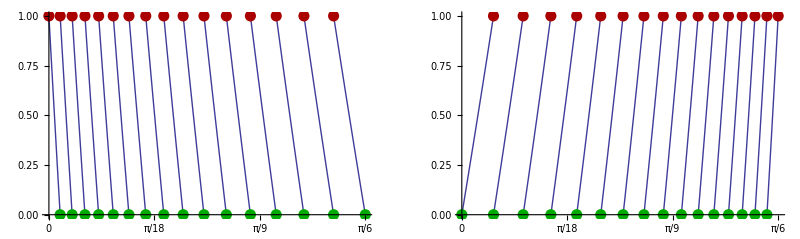

```mathematica
GraphicsRow[{plotErrorWithLinesAndPointsOne[4],plotErrorWithLinesAndPointsTwo[4]}]
```

```mathematica
Grid[{{plotErrorWithLinesAndPointsOne[4],plotErrorWithLinesAndPointsTwo[4]}}]
```

-Graphics-

We now need to find the intersecting points between the channels.
  To do this we first need to divide up the range into regions where there is only one intersection.

```mathematica
nn=4;
setupThetaRanges[nn];
```

```mathematica
TableForm[{thetaOneVals,thetaTwoVals}]
```

0 | ArcTan[1/(15 √3)] | ArcTan[1/(7 √3)] | ArcTan[(√3)/13] | ArcTan[1/(3 √3)] | ArcTan[5/(11 √3)] | ArcTan[(√3)/5] | ArcTan[7/(9 √3)] | π/6
0 | ArcTan[(√3)/17] | ArcTan[1/(3 √3)] | ArcTan[(3 √3)/19] | ArcTan[(√3)/5] | ArcTan[5/(7 √3)] | ArcTan[(3 √3)/11] | ArcTan[(7 √3)/23] | π/6

in each range we want to find the point of intersection between the errors for this we need to know which of the individual regions we are in for each of the channels.

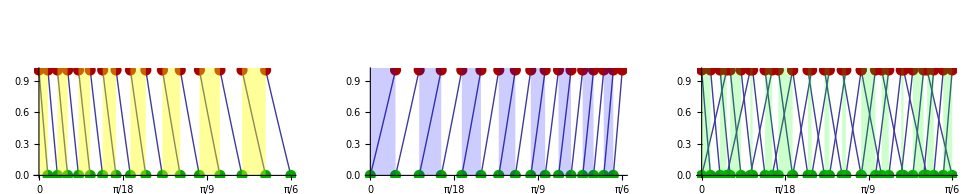

```mathematica
GraphicsRow[{Show[{plotErrorWithLinesAndPointsOne[nn],plotRegionsFromList[thetaOne[nn],Yellow,0.4]}],Show[{plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaTwo[nn],Blue,0.2]}],Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]]}]
}]
```

in each of the green intersecting regions we need the equatiuon of the lines to find the point of intersection. We use a linear approximation to find the points of intersection.

```mathematica
thetaMidPoints =Map[thetaToPoint,thetaMid];
pts1=ptsOne[nn];
pts2=ptsTwo[nn];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]]
```

{{0.0278999,0.274781},{0.0574832,0.566142},{0.0886554,0.873151},{0.121276,0.222839},{0.155194,0.6057},{0.225777,0.46404},{0.261799,0.932906},{0.297822,0.46404},{0.368404,0.6057},{0.402322,0.222839},{0.434943,0.873151},{0.466116,0.566142},{0.495699,0.274781}}

```mathematica
plotErrorIntersect[nn_,color_:Red,size_:0.02]:=Module[{minMaxPts},
thetaRanges[nn]; pts1=ptsOne[nn];
pts2=ptsTwo[nn];thetaMidPoints=Map[thetaToPoint,thetaMid];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]];
ListPlot[intersect,PlotStyle->{PointSize[size],Darker[color]}]]
```

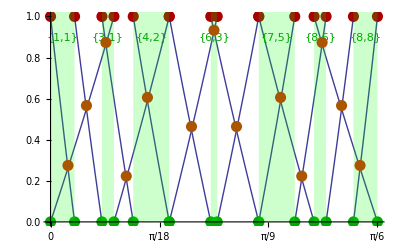

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],plotErrorIntersect[nn,Orange]}]
```

One missed point is where both happen to be zero!

```mathematica
intersect=errorMinTheta[4];
TableForm[{intersect[[All,1]],intersect[[All,2]]}]
```

0
0 | (ArcTan[1/(15 √3)] ArcTan[(√3)/17])/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17])
ArcTan[1/(15 √3)]/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17]) | (ArcTan[1/(7 √3)] ArcTan[(√3)/17])/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17])
ArcTan[1/(7 √3)]/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17]) | (ArcTan[(√3)/17] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13])
ArcTan[(√3)/13]/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13]) | (-ArcTan[1/(7 √3)] ArcTan[(√3)/17]+ArcTan[1/(3 √3)] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13])
(-ArcTan[(√3)/17]+ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13]) | (ArcTan[1/(3 √3)]^2-ArcTan[(√3)/17] ArcTan[(√3)/13])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13])
(ArcTan[1/(3 √3)]-ArcTan[(√3)/17])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13]) | ArcTan[1/(3 √3)]
0 | (-ArcTan[1/(3 √3)]^2+ArcTan[5/(11 √3)] ArcTan[(3 √3)/19])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19])
(-ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]) | (-ArcTan[1/(3 √3)] ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19] ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5])
(-ArcTan[1/(3 √3)]+ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5]) | (-ArcTan[5/(11 √3)] ArcTan[(3 √3)/19]+ArcTan[(√3)/5]^2)/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5])
(-ArcTan[(3 √3)/19]+ArcTan[(√3)/5])/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5]) | ArcTan[(√3)/5]
0 | (ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]-ArcTan[(√3)/5]^2)/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5])
(ArcTan[7/(9 √3)]-ArcTan[(√3)/5])/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5]) | (-ArcTan[5/(7 √3)] ArcTan[(√3)/5]+ArcTan[7/(9 √3)] ArcTan[(3 √3)/11])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11])
(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11]) | (-ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]+1/6 π ArcTan[(3 √3)/11])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11])
(π/6-ArcTan[5/(7 √3)])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11]) | (-ArcTan[7/(9 √3)] ArcTan[(3 √3)/11]+1/6 π ArcTan[(7 √3)/23])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23])
(π/6-ArcTan[(3 √3)/11])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23]) | (π^2/36-ArcTan[7/(9 √3)] ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23])
(π/6-ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23]) | π/6
0
0
0 | 1
1 | 2
1 | 3
1 | 3
2 | 4
2 | 4
2 | 5
3 | 6
3 | 6
4 | 6
4 | 7
5 | 7
6 | 8
6 | 8
7 | 8
8 | 9
9

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],ListPlot[intersect[[All,1]],PlotStyle->{PointSize[0.02],Orange}]}]
```

-Graphics-

The relationship to the round error

The intersecting points where the combined error is minimised are at the same points as for the truncated function in the theta direction.

```mathematica
intersectRound=Map[convRound,intersect];
intersectRoundPos=Map[classifyByPosition,intersectRound];
```

```mathematica
Clear[plotErrorWithLinesAndPointsOne,plotErrorWithLinesAndPointsTwo];
plotErrorWithLinesAndPointsOneR[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsOne[nn];Show[{Plot[{errOne[θ,nn,Round]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
plotErrorWithLinesAndPointsTwoR[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsTwo[nn];Show[{Plot[{errTwo[θ,nn,Round]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
```

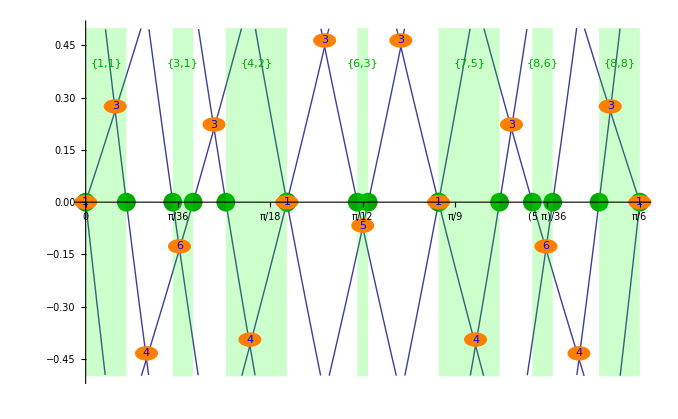

```mathematica
Show[{plotErrorWithLinesAndPointsOneR[nn],plotErrorWithLinesAndPointsTwoR[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid],{-0.5,0.5}],Graphics[Map[numDisk,intersectRoundPos]]},PlotRange->{{0,Pi/6},{-0.5,0.5}}]
```

Next we need to classify the points by the size of the error

One way to classify is by the order of the points on the lines.

```mathematica
intersectPos=Map[classifyByPosition,intersect];
```

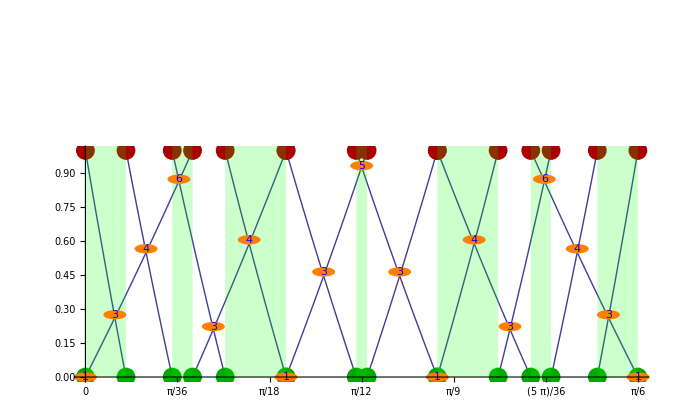

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],Graphics[Map[numDisk,intersectPos]]}]
```

Another is by the size of the error relative to negative powers of two ie 1, 0.5, 0.25, ...

```mathematica
classifyByNegPowerOfTwo[{x_,y_,class_}]:={x,y,Ceiling[-Log[Abs[y]]/Log[2]]}
```

```mathematica
intersectClassified=Map[classifyByNegPowerOfTwo,intersect]
```

{{0,0,∞},{(ArcTan[1/(15 √3)] ArcTan[(√3)/17])/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17]),ArcTan[1/(15 √3)]/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17]),2},{(ArcTan[1/(7 √3)] ArcTan[(√3)/17])/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17]),ArcTan[1/(7 √3)]/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17]),1},{(ArcTan[(√3)/17] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13]),ArcTan[(√3)/13]/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13]),1},{(-ArcTan[1/(7 √3)] ArcTan[(√3)/17]+ArcTan[1/(3 √3)] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13]),(-ArcTan[(√3)/17]+ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13]),3},{(ArcTan[1/(3 √3)]^2-ArcTan[(√3)/17] ArcTan[(√3)/13])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13]),(ArcTan[1/(3 √3)]-ArcTan[(√3)/17])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13]),1},{ArcTan[1/(3 √3)],0,∞},{(-ArcTan[1/(3 √3)]^2+ArcTan[5/(11 √3)] ArcTan[(3 √3)/19])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]),(-ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]),2},{(-ArcTan[1/(3 √3)] ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19] ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5]),(-ArcTan[1/(3 √3)]+ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5]),1},{(-ArcTan[5/(11 √3)] ArcTan[(3 √3)/19]+ArcTan[(√3)/5]^2)/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5]),(-ArcTan[(3 √3)/19]+ArcTan[(√3)/5])/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5]),2},{ArcTan[(√3)/5],0,∞},{(ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]-ArcTan[(√3)/5]^2)/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5]),(ArcTan[7/(9 √3)]-ArcTan[(√3)/5])/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5]),1},{(-ArcTan[5/(7 √3)] ArcTan[(√3)/5]+ArcTan[7/(9 √3)] ArcTan[(3 √3)/11])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11]),(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11]),3},{(-ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]+1/6 π ArcTan[(3 √3)/11])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11]),(π/6-ArcTan[5/(7 √3)])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11]),1},{(-ArcTan[7/(9 √3)] ArcTan[(3 √3)/11]+1/6 π ArcTan[(7 √3)/23])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23]),(π/6-ArcTan[(3 √3)/11])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23]),1},{(π^2/36-ArcTan[7/(9 √3)] ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23]),(π/6-ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23]),2},{π/6,0,∞}}

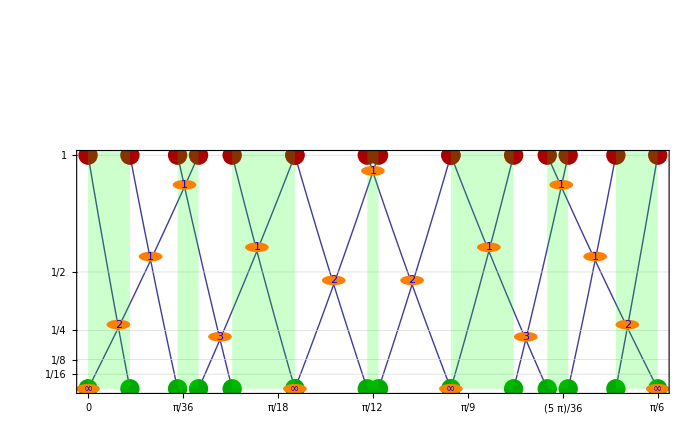

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],Graphics[Map[numDisk,intersectClassified]]},Frame->True,GridLines->{None,Table[N[2^(-i)],{i,0,4}]},FrameTicks->{PiTicks[0,Pi/6,6],Table[{N[2^(-i)],2^(-i)},{i,0,4}]}]
```

```mathematica
intersectRoundClassified=Map[classifyByNegPowerOfTwo,intersectRound];
```

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],Graphics[Map[numDisk,intersectRoundClassified]]},Frame->True,GridLines->{None,Table[N[2^(-i)],{i,0,4}]},FrameTicks->{PiTicks[0,Pi/6,6],Table[{N[2^(-i)],2^(-i)},{i,0,4}]}]
```

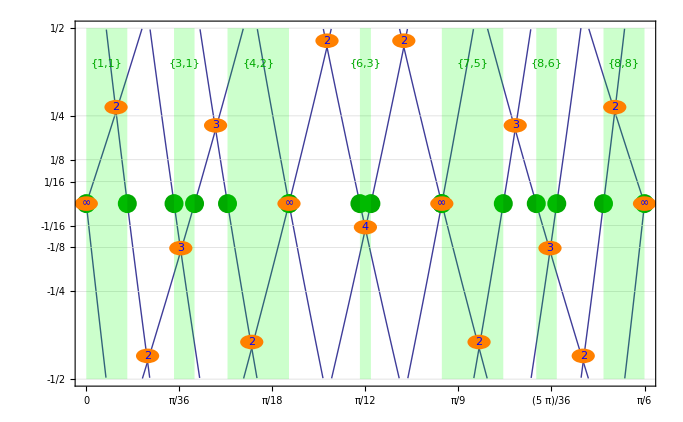

```mathematica
Show[{plotErrorWithLinesAndPointsOneR[nn],plotErrorWithLinesAndPointsTwoR[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid],{-0.5,0.5}],Graphics[Map[numDisk,intersectRoundClassified]]},PlotRange->{{0,Pi/6},{-0.5,0.5}},Frame->True,GridLines->{None,fracTicks[nn][[All,1]]},FrameTicks->{PiTicks[0,Pi/6,6],fracTicks[nn]}]
```

## Approximating rR with fR

```mathematica
ApplyToPiecewise[MatrixFormCubeColor[#,0.7]&,fRScaledErrorCube[θ,n,int]]
```

Piecewise[{{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6+θ]]+Sin[π/6+θ]) | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6+θ]]+Sin[π/6+θ]) | 0 | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6-θ]]+Sin[π/6-θ]) | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6-θ]]+Sin[π/6-θ]) | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6-θ]]+Sin[π/6-θ])+2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6+θ]]+Sin[π/6+θ]) | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6-θ]]+Sin[π/6-θ])+2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6+θ]]+Sin[π/6+θ])
0 | 2^n (Cos[π/6+θ]-2^(1-n) int[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ]) | 2^n (Cos[π/6+θ]-2^(1-n) int[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ]) | 0 | 2^n (-Cos[π/6-θ]+2^(1-n) int[2^(-1+n) Cos[π/6-θ] Csc[θ]] Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) int[2^(-1+n) Cos[π/6-θ] Csc[θ]] Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) int[2^(-1+n) Cos[π/6-θ] Csc[θ]] Sin[θ])+2^n (Cos[π/6+θ]-2^(1-n) int[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) int[2^(-1+n) Cos[π/6-θ] Csc[θ]] Sin[θ])+2^n (Cos[π/6+θ]-2^(1-n) int[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ])), π/6≤Mod[θ,π/2]<π/3}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^(1-n) int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ])+2^n (-2^(1-n) int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ]) | 0 | 2^n (-2^(1-n) int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ])+2^n (-2^(1-n) int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+Sin[π/6+θ])
0 | 2^n (Cos[π/6+θ]-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]) | 2^n (Cos[π/6+θ]-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]])+2^n (-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Sec[π/6-θ] Sin[θ]]+Sin[θ]) | 2^n (-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Sec[π/6-θ] Sin[θ]]+Sin[θ]) | 2^n (-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Sec[π/6-θ] Sin[θ]]+Sin[θ]) | 0 | 2^n (Cos[π/6+θ]-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]) | 2^n (Cos[π/6+θ]-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]])+2^n (-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Sec[π/6-θ] Sin[θ]]+Sin[θ])), π/3≤Mod[θ,π/2]<π/2}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ])+2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]) | 2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]) | 2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ])+2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ])
0 | 0 | 2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ]) | 2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] int[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]])+2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] int[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]) | 2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] int[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]) | 2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] int[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]])+2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ])), Mod[θ,π/2]≥0||Mod[θ,π/2]<π/2}, {Null, True}}]

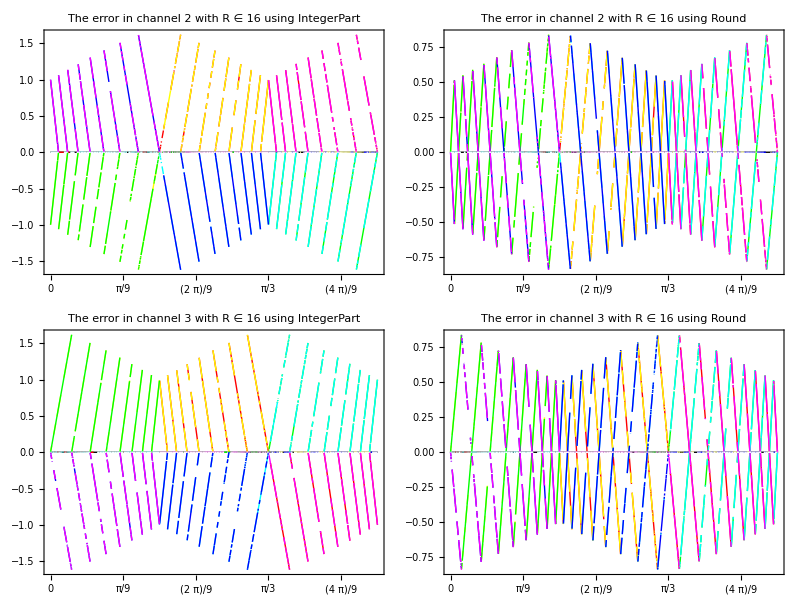

```mathematica
simpleErrorPlot[{0,Pi/2},fRScaledErrorCube,4]
```

The base function for the channel error

```mathematica
2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]) 2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ])
```

```mathematica
errTwo[θ_,n_,int_]:=2^n*((-2^(1 - n))*Cos[Pi/6 + θ]*int[2^(-1 + n)*Sec[Pi/6 + θ]*Sin[θ]] + Sin[θ])
```

```mathematica
errOne[θ_,n_,int_]:=2^n*(Sin[Pi/6 - θ] - 2^(1 - n)*int[2^(-1 + n)*Csc[Pi/6 + θ]*Sin[Pi/6 - θ]]*Sin[Pi/6 + θ]);
```

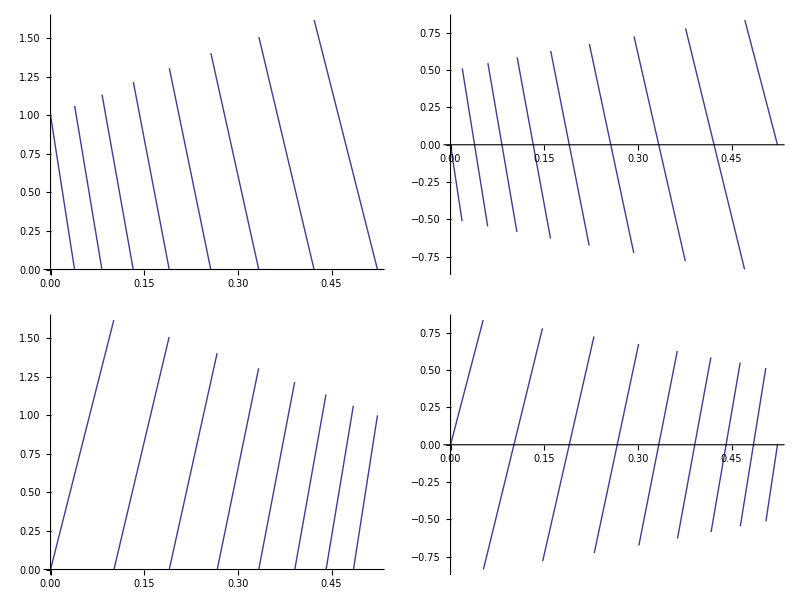

```mathematica
Grid[{{Plot[errOne[θ,4,IntegerPart],{θ,0,Pi/6}],Plot[errOne[θ,4,Round],{θ,0,Pi/6}]},
{Plot[errTwo[θ,4,IntegerPart],{θ,0,Pi/6}],Plot[errTwo[θ,4,Round],{θ,0,Pi/6}]}}]
```

to find the zeros we need to solve

sin(π/6-θ)==2^(1-n) sin(θ+π/6) int(2^(n-1) sin(π/6-θ) csc(θ+π/6))

```mathematica
2^(n-1) sin(π/6-θ) csc(θ+π/6)== int(2^(n-1) sin(π/6-θ) csc(θ+π/6))
```

```mathematica
Simplify[Assuming[Element[θ,Reals]&& θ≥ 0 && θ≤ Pi/6, Solve[y== Csc[π/6+θ] Sin[π/6 - θ],θ]]]
```

{{θ→ConditionalExpression[ArcTan[-(√3 (1+y))/(√(1+y+y^2)),(-1+y)/(√(1+y+y^2))]+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))]+2 π C[1],C[1]∈Integers]}}

For a given value of n there are 2^(n - 1) + 1 zeros between 0 and Pi/6

```mathematica
thetaOne[n_]:=Block[{fun},fun[y_]:=ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))];Table[fun[i/(2^(n-1))],{i,2^(n-1),0,-1}]]
thetaTwo[n_]:=Block[{funTwo},funTwo[y_]:=ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))];Table[funTwo[i/(2^(n-1))],{i,0,2^(n-1)}]]
```

```mathematica
nn=4;
setupThetaRanges[nn];
```

The maximum error is given by Sin[θ+π/6] for 0≤ θ≤ Pi/6

```mathematica
maxErrOne[θ_]:=2 Sin[Mod[θ,π/6]+π/6]
maxErrTwo[θ_]:=2 Sin[π/6+Mod[-θ,π/6]]
SetAttributes[maxErrOne,Listable]
SetAttributes[maxErrTwo,Listable]
```

The min and max points are then found by using the values for theta with the max error function

```mathematica
ptsOne[n_]:=Module[{thetaPts},thetaPts=thetaOne[n];{Transpose[{Most[thetaPts],maxErrOne[Most[thetaPts]]}],Transpose[{Rest[thetaPts],Table[0,{i,1,2^(n-1)}]}]}]
ptsTwo[n_]:=Module[{thetaPts},thetaPts=thetaTwo[n];{Transpose[{Most[thetaPts],Table[0,{i,1,2^(n-1)}]}],Transpose[{Rest[thetaPts],maxErrTwo[Rest[thetaPts]]}]}]
```

```mathematica
Clear[plotErrorWithLinesAndPointsOne,plotErrorWithLinesAndPointsTwo];
plotErrorWithLinesAndPointsOne[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsOne[nn];Show[{Plot[{err[θ,nn,IntegerPart],maxErrOne[θ]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
plotErrorWithLinesAndPointsTwo[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsTwo[nn];Show[{Plot[{errTwo[θ,nn,IntegerPart],maxErrTwo[θ]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
```

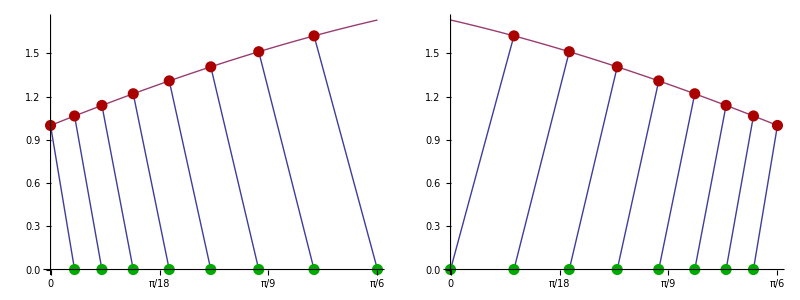

```mathematica
Grid[{{plotErrorWithLinesAndPointsOne[4],plotErrorWithLinesAndPointsTwo[4]}}]
```

We now need to find the intersecting points between the channels.
  To do this we first need to divide up the range into regions where there is only one intersection.

```mathematica
nn=4;
setupThetaRanges[nn];
```

```mathematica
TableForm[{thetaOneVals,thetaTwoVals}]
```

0 | ArcTan[1/(15 √3)] | ArcTan[1/(7 √3)] | ArcTan[(√3)/13] | ArcTan[1/(3 √3)] | ArcTan[5/(11 √3)] | ArcTan[(√3)/5] | ArcTan[7/(9 √3)] | π/6
0 | ArcTan[(√3)/17] | ArcTan[1/(3 √3)] | ArcTan[(3 √3)/19] | ArcTan[(√3)/5] | ArcTan[5/(7 √3)] | ArcTan[(3 √3)/11] | ArcTan[(7 √3)/23] | π/6

in each range we want to find the point of intersection between the errors for this we need to know which of the individual regions we are in for each of the channels.

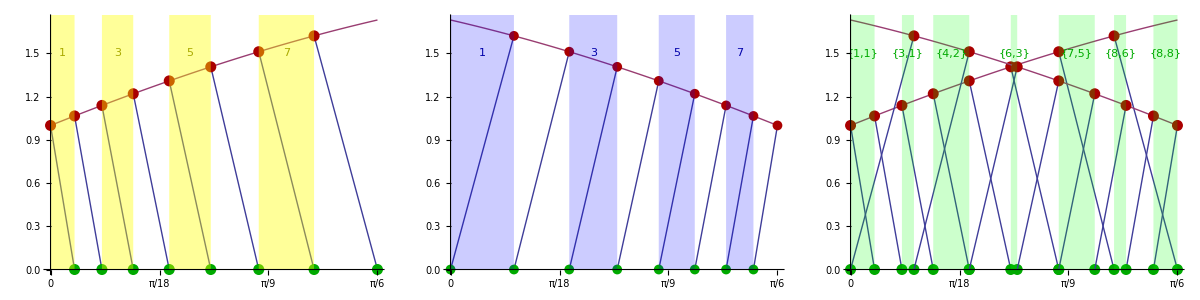

```mathematica
Grid[{{Show[{plotErrorWithLinesAndPointsOne[nn],plotRegionsFromList[thetaOne[nn],Yellow,0.4]}],Show[{plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaTwo[nn],Blue,0.2]}],Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]]}]
}}]
```

in each of the green intersecting regions we need the equatiuon of the lines to find the point of intersection. We use a linear approximation to find the points of intersection.

```mathematica
thetaMidPoints =Map[thetaToPoint,thetaMid];
pts1=ptsOne[nn];
pts2=ptsTwo[nn];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]]
```

{{0.0238288,0.380605},{0.0496731,0.793405},{0.0777568,1.24197},{0.119187,0.301249},{0.150569,0.836795},{0.224585,0.631033},{0.261799,1.31251},{0.299014,0.631033},{0.37303,0.836795},{0.404411,0.301249},{0.445842,1.24197},{0.473926,0.793405},{0.49977,0.380605}}

```mathematica
plotErrorIntersect[nn_,color_:Red,size_:0.02]:=Module[{minMaxPts},
thetaRanges[nn]; pts1=ptsOne[nn];
pts2=ptsTwo[nn];thetaMidPoints=Map[thetaToPoint,thetaMid];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]];
ListPlot[intersect,PlotStyle->{PointSize[size],Darker[color]}]]
```

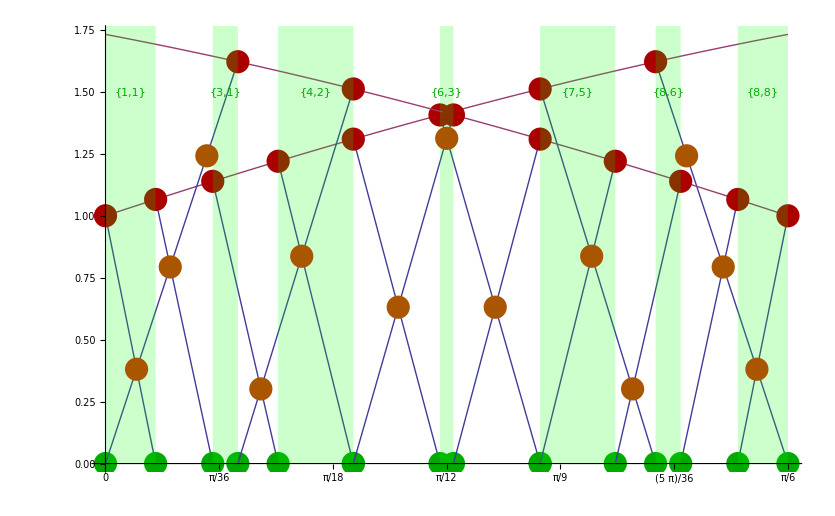

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],plotErrorIntersect[nn,Orange]}]
```

## Generating LookupTables

Generate base table

```mathematica
Do[intersect[n]=errorMinTheta[n];Print[StringJoin["Processing : ",ToString[n]]],{n,2,7}]
```

Processing : 2

Processing : 3

Processing : 4

Processing : 5

Processing : 6

Processing : 7

```mathematica
Save[StringJoin[NotebookDirectory[],"errorMinsIntersect.nb"],"intersect"]
```

```mathematica
Get[StringJoin[NotebookDirectory[],"errorMinsIntersect.nb"]];
```

```mathematica
Do[
intersectRound[n]=Map[convRound,intersect[n]];
Print[StringJoin["Processing : ",ToString[n]]],{n,2,12}];
```

Processing : 2

Processing : 3

Processing : 4

Processing : 5

Processing : 6

Processing : 7

Processing : 8

Processing : 9

Processing : 10

Processing : 11

Processing : 12

```mathematica
Clear[thetaGood]
```

```mathematica
Do[
intersectClassified[n]=Map[classifyByNegPowerOfTwo,intersect[n]];
intersectRoundClassified[n]=Map[classifyByNegPowerOfTwo,intersectRound[n]];
thetaGood[1,        n,IntegerPart] = intersectClassified[n][[All,1]];
Do[
thetaGood[2^(-m),    n,IntegerPart]=Extract[thetaGood[1,n,IntegerPart],Position[Map[#> m&,intersectClassified[n][[All,2]]],True]];
thetaGood[2^(-m),    n,Round]=Extract[thetaGood[1,n,IntegerPart],Position[Map[#> m&,intersectRoundClassified[n][[All,2]]],True]];
,{m,1,3}];
Print[StringJoin["Processing : ",ToString[n]]],{n,2,12}]
```

Processing : 2

Processing : 3

Processing : 4

Processing : 5

Processing : 6

Processing : 7

Processing : 8

Processing : 9

Processing : 10

Processing : 11

Processing : 12

```mathematica
Definition[thetaGood]
```

«1»

```mathematica
thetaGood[1/4,7,IntegerPart]
```

{{0,0},{(-ArcTan[1/(63 √3)] ArcTan[1/(43 √3)]+ArcTan[(√3)/125] ArcTan[(√3)/65])/(-ArcTan[1/(63 √3)]-ArcTan[1/(43 √3)]+ArcTan[(√3)/125]+ArcTan[(√3)/65]),(-ArcTan[1/(43 √3)]+ArcTan[(√3)/125])/(-ArcTan[1/(63 √3)]-ArcTan[1/(43 √3)]+ArcTan[(√3)/125]+ArcTan[(√3)/65])},{(-ArcTan[5/(123 √3)] ArcTan[(√3)/65]+ArcTan[(√3)/61] ArcTan[(3 √3)/131])/(-ArcTan[5/(123 √3)]-ArcTan[(√3)/65]+ArcTan[(√3)/61]+ArcTan[(3 √3)/131]),(-ArcTan[(√3)/65]+ArcTan[(√3)/61])/(-ArcTan[5/(123 √3)]-ArcTan[(√3)/65]+ArcTan[(√3)/61]+ArcTan[(3 √3)/131])},{(-ArcTan[1/(15 √3)] ArcTan[(3 √3)/131]+ArcTan[1/(11 √3)] ArcTan[(3 √3)/119])/(-ArcTan[1/(15 √3)]+ArcTan[1/(11 √3)]-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119]),(-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119])/(-ArcTan[1/(15 √3)]+ArcTan[1/(11 √3)]-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119])},{(-ArcTan[5/(59 √3)] ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)] ArcTan[(5 √3)/133])/(-ArcTan[5/(59 √3)]-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)]+ArcTan[(5 √3)/133]),(-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)])/(-ArcTan[5/(59 √3)]-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)]+ArcTan[(5 √3)/133])},{(-ArcTan[(√3)/29] ArcTan[(5 √3)/133]+ArcTan[13/(115 √3)] ArcTan[(3 √3)/67])/(ArcTan[13/(115 √3)]-ArcTan[(√3)/29]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67]),(ArcTan[13/(115 √3)]-ArcTan[(5 √3)/133])/(ArcTan[13/(115 √3)]-ArcTan[(√3)/29]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67])},{(-ArcTan[11/(53 √3)] ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)] ArcTan[(11 √3)/139])/(-ArcTan[11/(53 √3)]-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)]+ArcTan[(11 √3)/139]),(-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)])/(-ArcTan[11/(53 √3)]-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)]+ArcTan[(11 √3)/139])},{(-ArcTan[(√3)/13] ArcTan[(11 √3)/139]+ArcTan[25/(103 √3)] ArcTan[(3 √3)/35])/(ArcTan[25/(103 √3)]-ArcTan[(√3)/13]-ArcTan[(11 √3)/139]+ArcTan[(3 √3)/35]),(ArcTan[25/(103 √3)]-ArcTan[(11 √3)/139])/(ArcTan[25/(103 √3)]-ArcTan[(√3)/13]-ArcTan[(11 √3)/139]+ArcTan[(3 √3)/35])},{(-ArcTan[13/(47 √3)] ArcTan[(9 √3)/101]+ArcTan[7/(25 √3)] ArcTan[(7 √3)/71])/(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)]-ArcTan[(9 √3)/101]+ArcTan[(7 √3)/71]),(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)])/(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)]-ArcTan[(9 √3)/101]+ArcTan[(7 √3)/71])},{(ArcTan[31/(97 √3)] ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49] ArcTan[(15 √3)/143])/(ArcTan[31/(97 √3)]+ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49]-ArcTan[(15 √3)/143]),(ArcTan[31/(97 √3)]-ArcTan[(15 √3)/143])/(ArcTan[31/(97 √3)]+ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49]-ArcTan[(15 √3)/143])},{ArcTan[1/(3 √3)],0},{(ArcTan[35/(93 √3)] ArcTan[19/(49 √3)]-ArcTan[17/(47 √3)] ArcTan[(9 √3)/73])/(-ArcTan[17/(47 √3)]+ArcTan[35/(93 √3)]+ArcTan[19/(49 √3)]-ArcTan[(9 √3)/73]),(ArcTan[35/(93 √3)]-ArcTan[(9 √3)/73])/(-ArcTan[17/(47 √3)]+ArcTan[35/(93 √3)]+ArcTan[19/(49 √3)]-ArcTan[(9 √3)/73])},{(-ArcTan[35/(93 √3)] ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23] ArcTan[(5 √3)/37])/(-ArcTan[35/(93 √3)]-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23]+ArcTan[(5 √3)/37]),(-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23])/(-ArcTan[35/(93 √3)]-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23]+ArcTan[(5 √3)/37])},{(-ArcTan[(3 √3)/23] ArcTan[(5 √3)/37]+ArcTan[37/(91 √3)] ArcTan[(21 √3)/149])/(ArcTan[37/(91 √3)]-ArcTan[(3 √3)/23]-ArcTan[(5 √3)/37]+ArcTan[(21 √3)/149]),(ArcTan[37/(91 √3)]-ArcTan[(5 √3)/37])/(ArcTan[37/(91 √3)]-ArcTan[(3 √3)/23]-ArcTan[(5 √3)/37]+ArcTan[(21 √3)/149])},{(ArcTan[11/(21 √3)] ArcTan[7/(13 √3)]-ArcTan[43/(85 √3)] ArcTan[(27 √3)/155])/(-ArcTan[43/(85 √3)]+ArcTan[11/(21 √3)]+ArcTan[7/(13 √3)]-ArcTan[(27 √3)/155]),(ArcTan[11/(21 √3)]-ArcTan[(27 √3)/155])/(-ArcTan[43/(85 √3)]+ArcTan[11/(21 √3)]+ArcTan[7/(13 √3)]-ArcTan[(27 √3)/155])},{(-ArcTan[11/(21 √3)] ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83] ArcTan[(29 √3)/157])/(-ArcTan[11/(21 √3)]-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83]+ArcTan[(29 √3)/157]),(-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83])/(-ArcTan[11/(21 √3)]-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83]+ArcTan[(29 √3)/157])},{(-ArcTan[(15 √3)/83] ArcTan[(29 √3)/157]+ArcTan[23/(41 √3)] ArcTan[(15 √3)/79])/(ArcTan[23/(41 √3)]-ArcTan[(15 √3)/83]-ArcTan[(29 √3)/157]+ArcTan[(15 √3)/79]),(ArcTan[23/(41 √3)]-ArcTan[(29 √3)/157])/(ArcTan[23/(41 √3)]-ArcTan[(15 √3)/83]-ArcTan[(29 √3)/157]+ArcTan[(15 √3)/79])},{ArcTan[(√3)/5],0},{(ArcTan[49/(79 √3)] ArcTan[17/(27 √3)]-ArcTan[(√3)/5] ArcTan[(33 √3)/161])/(ArcTan[49/(79 √3)]+ArcTan[17/(27 √3)]-ArcTan[(√3)/5]-ArcTan[(33 √3)/161]),(ArcTan[49/(79 √3)]-ArcTan[(33 √3)/161])/(ArcTan[49/(79 √3)]+ArcTan[17/(27 √3)]-ArcTan[(√3)/5]-ArcTan[(33 √3)/161])},{(-ArcTan[25/(39 √3)] ArcTan[(9 √3)/41]+ArcTan[37/(55 √3)] ArcTan[(17 √3)/77])/(-ArcTan[25/(39 √3)]+ArcTan[37/(55 √3)]-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77]),(-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77])/(-ArcTan[25/(39 √3)]+ArcTan[37/(55 √3)]-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77])},{(ArcTan[53/(75 √3)] ArcTan[5/(7 √3)]-ArcTan[13/(19 √3)] ArcTan[(39 √3)/167])/(-ArcTan[13/(19 √3)]+ArcTan[53/(75 √3)]+ArcTan[5/(7 √3)]-ArcTan[(39 √3)/167]),(ArcTan[53/(75 √3)]-ArcTan[(39 √3)/167])/(-ArcTan[13/(19 √3)]+ArcTan[53/(75 √3)]+ArcTan[5/(7 √3)]-ArcTan[(39 √3)/167])},{(-ArcTan[53/(75 √3)] ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37] ArcTan[(21 √3)/85])/(-ArcTan[53/(75 √3)]-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]+ArcTan[(21 √3)/85]),(-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37])/(-ArcTan[53/(75 √3)]-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]+ArcTan[(21 √3)/85])},{(ArcTan[59/(69 √3)] ArcTan[13/(15 √3)]-ArcTan[29/(35 √3)] ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]+ArcTan[13/(15 √3)]-ArcTan[(51 √3)/179]),(ArcTan[59/(69 √3)]-ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]+ArcTan[13/(15 √3)]-ArcTan[(51 √3)/179])},{(-ArcTan[59/(69 √3)] ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17] ArcTan[(27 √3)/91])/(-ArcTan[59/(69 √3)]-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]+ArcTan[(27 √3)/91]),(-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17])/(-ArcTan[59/(69 √3)]-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]+ArcTan[(27 √3)/91])},{(-ArcTan[55/(61 √3)] ArcTan[(5 √3)/17]+ArcTan[61/(67 √3)] ArcTan[(7 √3)/23])/(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)]-ArcTan[(5 √3)/17]+ArcTan[(7 √3)/23]),(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)])/(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)]-ArcTan[(5 √3)/17]+ArcTan[(7 √3)/23])},{(-ArcTan[61/(67 √3)] ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)] ArcTan[(59 √3)/187])/(-ArcTan[61/(67 √3)]-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]+ArcTan[(59 √3)/187]),(-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)])/(-ArcTan[61/(67 √3)]-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]+ArcTan[(59 √3)/187])},{(-ArcTan[31/(33 √3)] ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65] ArcTan[(31 √3)/95])/(-ArcTan[31/(33 √3)]-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65]+ArcTan[(31 √3)/95]),(-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65])/(-ArcTan[31/(33 √3)]-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65]+ArcTan[(31 √3)/95])},{π/6,0}}

```mathematica
thetaGood[1/2,7,IntegerPart]
```

{{0,0},{(ArcTan[1/(127 √3)] ArcTan[1/(43 √3)])/(ArcTan[1/(127 √3)]+ArcTan[1/(43 √3)]),ArcTan[1/(127 √3)]/(ArcTan[1/(127 √3)]+ArcTan[1/(43 √3)])},{(-ArcTan[1/(63 √3)] ArcTan[1/(43 √3)]+ArcTan[(√3)/125] ArcTan[(√3)/65])/(-ArcTan[1/(63 √3)]-ArcTan[1/(43 √3)]+ArcTan[(√3)/125]+ArcTan[(√3)/65]),(-ArcTan[1/(43 √3)]+ArcTan[(√3)/125])/(-ArcTan[1/(63 √3)]-ArcTan[1/(43 √3)]+ArcTan[(√3)/125]+ArcTan[(√3)/65])},{(-ArcTan[1/(43 √3)] ArcTan[(√3)/125]+ArcTan[1/(31 √3)] ArcTan[(√3)/65])/(-ArcTan[1/(43 √3)]+ArcTan[1/(31 √3)]-ArcTan[(√3)/125]+ArcTan[(√3)/65]),(-ArcTan[1/(43 √3)]+ArcTan[1/(31 √3)])/(-ArcTan[1/(43 √3)]+ArcTan[1/(31 √3)]-ArcTan[(√3)/125]+ArcTan[(√3)/65])},{(-ArcTan[5/(123 √3)] ArcTan[(√3)/65]+ArcTan[(√3)/61] ArcTan[(3 √3)/131])/(-ArcTan[5/(123 √3)]-ArcTan[(√3)/65]+ArcTan[(√3)/61]+ArcTan[(3 √3)/131]),(-ArcTan[(√3)/65]+ArcTan[(√3)/61])/(-ArcTan[5/(123 √3)]-ArcTan[(√3)/65]+ArcTan[(√3)/61]+ArcTan[(3 √3)/131])},{(-ArcTan[(√3)/65] ArcTan[(√3)/61]+ArcTan[7/(121 √3)] ArcTan[(3 √3)/131])/(ArcTan[7/(121 √3)]-ArcTan[(√3)/65]-ArcTan[(√3)/61]+ArcTan[(3 √3)/131]),(ArcTan[7/(121 √3)]-ArcTan[(√3)/65])/(ArcTan[7/(121 √3)]-ArcTan[(√3)/65]-ArcTan[(√3)/61]+ArcTan[(3 √3)/131])},{(-ArcTan[1/(15 √3)] ArcTan[(3 √3)/131]+ArcTan[1/(11 √3)] ArcTan[(3 √3)/119])/(-ArcTan[1/(15 √3)]+ArcTan[1/(11 √3)]-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119]),(-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119])/(-ArcTan[1/(15 √3)]+ArcTan[1/(11 √3)]-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119])},{(-ArcTan[5/(59 √3)] ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)] ArcTan[(5 √3)/133])/(-ArcTan[5/(59 √3)]-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)]+ArcTan[(5 √3)/133]),(-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)])/(-ArcTan[5/(59 √3)]-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)]+ArcTan[(5 √3)/133])},{(-ArcTan[1/(11 √3)] ArcTan[11/(117 √3)]+ArcTan[(√3)/29] ArcTan[(5 √3)/133])/(-ArcTan[1/(11 √3)]-ArcTan[11/(117 √3)]+ArcTan[(√3)/29]+ArcTan[(5 √3)/133]),(-ArcTan[1/(11 √3)]+ArcTan[(√3)/29])/(-ArcTan[1/(11 √3)]-ArcTan[11/(117 √3)]+ArcTan[(√3)/29]+ArcTan[(5 √3)/133])},{(-ArcTan[(√3)/29] ArcTan[(5 √3)/133]+ArcTan[13/(115 √3)] ArcTan[(3 √3)/67])/(ArcTan[13/(115 √3)]-ArcTan[(√3)/29]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67]),(ArcTan[13/(115 √3)]-ArcTan[(5 √3)/133])/(ArcTan[13/(115 √3)]-ArcTan[(√3)/29]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67])},{(-ArcTan[13/(115 √3)] ArcTan[(5 √3)/133]+ArcTan[7/(57 √3)] ArcTan[(3 √3)/67])/(-ArcTan[13/(115 √3)]+ArcTan[7/(57 √3)]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67]),(ArcTan[7/(57 √3)]-ArcTan[(5 √3)/133])/(-ArcTan[13/(115 √3)]+ArcTan[7/(57 √3)]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67])},{(ArcTan[1/(7 √3)] ArcTan[7/(45 √3)]-ArcTan[(5 √3)/113] ArcTan[(3 √3)/67])/(ArcTan[1/(7 √3)]+ArcTan[7/(45 √3)]-ArcTan[(5 √3)/113]-ArcTan[(3 √3)/67]),(ArcTan[1/(7 √3)]-ArcTan[(3 √3)/67])/(ArcTan[1/(7 √3)]+ArcTan[7/(45 √3)]-ArcTan[(5 √3)/113]-ArcTan[(3 √3)/67])},{(-ArcTan[17/(111 √3)] ArcTan[7/(45 √3)]+ArcTan[(3 √3)/55] ArcTan[(√3)/17])/(-ArcTan[17/(111 √3)]-ArcTan[7/(45 √3)]+ArcTan[(3 √3)/55]+ArcTan[(√3)/17]),(-ArcTan[7/(45 √3)]+ArcTan[(3 √3)/55])/(-ArcTan[17/(111 √3)]-ArcTan[7/(45 √3)]+ArcTan[(3 √3)/55]+ArcTan[(√3)/17])},{(-ArcTan[19/(109 √3)] ArcTan[(√3)/17]+ArcTan[5/(27 √3)] ArcTan[(9 √3)/137])/(-ArcTan[19/(109 √3)]+ArcTan[5/(27 √3)]-ArcTan[(√3)/17]+ArcTan[(9 √3)/137]),(ArcTan[5/(27 √3)]-ArcTan[(√3)/17])/(-ArcTan[19/(109 √3)]+ArcTan[5/(27 √3)]-ArcTan[(√3)/17]+ArcTan[(9 √3)/137])},{(ArcTan[11/(53 √3)] ArcTan[5/(23 √3)]-ArcTan[(7 √3)/107] ArcTan[(9 √3)/137])/(ArcTan[11/(53 √3)]+ArcTan[5/(23 √3)]-ArcTan[(7 √3)/107]-ArcTan[(9 √3)/137]),(ArcTan[11/(53 √3)]-ArcTan[(9 √3)/137])/(ArcTan[11/(53 √3)]+ArcTan[5/(23 √3)]-ArcTan[(7 √3)/107]-ArcTan[(9 √3)/137])},{(-ArcTan[11/(53 √3)] ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)] ArcTan[(11 √3)/139])/(-ArcTan[11/(53 √3)]-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)]+ArcTan[(11 √3)/139]),(-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)])/(-ArcTan[11/(53 √3)]-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)]+ArcTan[(11 √3)/139])},{(-ArcTan[5/(23 √3)] ArcTan[23/(105 √3)]+ArcTan[(√3)/13] ArcTan[(11 √3)/139])/(-ArcTan[5/(23 √3)]-ArcTan[23/(105 √3)]+ArcTan[(√3)/13]+ArcTan[(11 √3)/139]),(-ArcTan[5/(23 √3)]+ArcTan[(√3)/13])/(-ArcTan[5/(23 √3)]-ArcTan[23/(105 √3)]+ArcTan[(√3)/13]+ArcTan[(11 √3)/139])},{(-ArcTan[(√3)/13] ArcTan[(11 √3)/139]+ArcTan[25/(103 √3)] ArcTan[(3 √3)/35])/(ArcTan[25/(103 √3)]-ArcTan[(√3)/13]-ArcTan[(11 √3)/139]+ArcTan[(3 √3)/35]),(ArcTan[25/(103 √3)]-ArcTan[(11 √3)/139])/(ArcTan[25/(103 √3)]-ArcTan[(√3)/13]-ArcTan[(11 √3)/139]+ArcTan[(3 √3)/35])},{(-ArcTan[13/(51 √3)] ArcTan[(3 √3)/35]+ArcTan[13/(47 √3)] ArcTan[(9 √3)/101])/(-ArcTan[13/(51 √3)]+ArcTan[13/(47 √3)]-ArcTan[(3 √3)/35]+ArcTan[(9 √3)/101]),(-ArcTan[(3 √3)/35]+ArcTan[(9 √3)/101])/(-ArcTan[13/(51 √3)]+ArcTan[13/(47 √3)]-ArcTan[(3 √3)/35]+ArcTan[(9 √3)/101])},{(-ArcTan[13/(47 √3)] ArcTan[(9 √3)/101]+ArcTan[7/(25 √3)] ArcTan[(7 √3)/71])/(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)]-ArcTan[(9 √3)/101]+ArcTan[(7 √3)/71]),(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)])/(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)]-ArcTan[(9 √3)/101]+ArcTan[(7 √3)/71])},{(-ArcTan[29/(99 √3)] ArcTan[(7 √3)/71]+ArcTan[(5 √3)/49] ArcTan[(15 √3)/143])/(-ArcTan[29/(99 √3)]-ArcTan[(7 √3)/71]+ArcTan[(5 √3)/49]+ArcTan[(15 √3)/143]),(-ArcTan[(7 √3)/71]+ArcTan[(5 √3)/49])/(-ArcTan[29/(99 √3)]-ArcTan[(7 √3)/71]+ArcTan[(5 √3)/49]+ArcTan[(15 √3)/143])},{(ArcTan[31/(97 √3)] ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49] ArcTan[(15 √3)/143])/(ArcTan[31/(97 √3)]+ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49]-ArcTan[(15 √3)/143]),(ArcTan[31/(97 √3)]-ArcTan[(15 √3)/143])/(ArcTan[31/(97 √3)]+ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49]-ArcTan[(15 √3)/143])},{ArcTan[1/(3 √3)],0},{(-ArcTan[1/(3 √3)]^2+ArcTan[(11 √3)/95] ArcTan[(17 √3)/145])/(-2 ArcTan[1/(3 √3)]+ArcTan[(11 √3)/95]+ArcTan[(17 √3)/145]),(-ArcTan[1/(3 √3)]+ArcTan[(11 √3)/95])/(-2 ArcTan[1/(3 √3)]+ArcTan[(11 √3)/95]+ArcTan[(17 √3)/145])},{(-ArcTan[(11 √3)/95] ArcTan[(17 √3)/145]+ArcTan[17/(47 √3)] ArcTan[(9 √3)/73])/(ArcTan[17/(47 √3)]-ArcTan[(11 √3)/95]-ArcTan[(17 √3)/145]+ArcTan[(9 √3)/73]),(ArcTan[17/(47 √3)]-ArcTan[(17 √3)/145])/(ArcTan[17/(47 √3)]-ArcTan[(11 √3)/95]-ArcTan[(17 √3)/145]+ArcTan[(9 √3)/73])},{(ArcTan[35/(93 √3)] ArcTan[19/(49 √3)]-ArcTan[17/(47 √3)] ArcTan[(9 √3)/73])/(-ArcTan[17/(47 √3)]+ArcTan[35/(93 √3)]+ArcTan[19/(49 √3)]-ArcTan[(9 √3)/73]),(ArcTan[35/(93 √3)]-ArcTan[(9 √3)/73])/(-ArcTan[17/(47 √3)]+ArcTan[35/(93 √3)]+ArcTan[19/(49 √3)]-ArcTan[(9 √3)/73])},{(-ArcTan[35/(93 √3)] ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23] ArcTan[(5 √3)/37])/(-ArcTan[35/(93 √3)]-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23]+ArcTan[(5 √3)/37]),(-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23])/(-ArcTan[35/(93 √3)]-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23]+ArcTan[(5 √3)/37])},{(-ArcTan[(3 √3)/23] ArcTan[(5 √3)/37]+ArcTan[37/(91 √3)] ArcTan[(21 √3)/149])/(ArcTan[37/(91 √3)]-ArcTan[(3 √3)/23]-ArcTan[(5 √3)/37]+ArcTan[(21 √3)/149]),(ArcTan[37/(91 √3)]-ArcTan[(5 √3)/37])/(ArcTan[37/(91 √3)]-ArcTan[(3 √3)/23]-ArcTan[(5 √3)/37]+ArcTan[(21 √3)/149])},{(-ArcTan[19/(45 √3)] ArcTan[(21 √3)/149]+ArcTan[11/(25 √3)] ArcTan[(13 √3)/89])/(-ArcTan[19/(45 √3)]+ArcTan[11/(25 √3)]-ArcTan[(21 √3)/149]+ArcTan[(13 √3)/89]),(-ArcTan[(21 √3)/149]+ArcTan[(13 √3)/89])/(-ArcTan[19/(45 √3)]+ArcTan[11/(25 √3)]-ArcTan[(21 √3)/149]+ArcTan[(13 √3)/89])},{(-ArcTan[11/(25 √3)] ArcTan[(13 √3)/89]+ArcTan[5/(11 √3)] ArcTan[(23 √3)/151])/(-ArcTan[11/(25 √3)]+ArcTan[5/(11 √3)]-ArcTan[(13 √3)/89]+ArcTan[(23 √3)/151]),(-ArcTan[11/(25 √3)]+ArcTan[5/(11 √3)])/(-ArcTan[11/(25 √3)]+ArcTan[5/(11 √3)]-ArcTan[(13 √3)/89]+ArcTan[(23 √3)/151])},{(-ArcTan[5/(11 √3)] ArcTan[(23 √3)/151]+ArcTan[41/(87 √3)] ArcTan[(3 √3)/19])/(-ArcTan[5/(11 √3)]+ArcTan[41/(87 √3)]-ArcTan[(23 √3)/151]+ArcTan[(3 √3)/19]),(ArcTan[41/(87 √3)]-ArcTan[(23 √3)/151])/(-ArcTan[5/(11 √3)]+ArcTan[41/(87 √3)]-ArcTan[(23 √3)/151]+ArcTan[(3 √3)/19])},{(-ArcTan[41/(87 √3)] ArcTan[(3 √3)/19]+ArcTan[25/(51 √3)] ArcTan[(7 √3)/43])/(-ArcTan[41/(87 √3)]+ArcTan[25/(51 √3)]-ArcTan[(3 √3)/19]+ArcTan[(7 √3)/43]),(-ArcTan[(3 √3)/19]+ArcTan[(7 √3)/43])/(-ArcTan[41/(87 √3)]+ArcTan[25/(51 √3)]-ArcTan[(3 √3)/19]+ArcTan[(7 √3)/43])},{(-ArcTan[25/(51 √3)] ArcTan[(7 √3)/43]+ArcTan[43/(85 √3)] ArcTan[(13 √3)/77])/(-ArcTan[25/(51 √3)]+ArcTan[43/(85 √3)]-ArcTan[(7 √3)/43]+ArcTan[(13 √3)/77]),(-ArcTan[25/(51 √3)]+ArcTan[43/(85 √3)])/(-ArcTan[25/(51 √3)]+ArcTan[43/(85 √3)]-ArcTan[(7 √3)/43]+ArcTan[(13 √3)/77])},{(ArcTan[11/(21 √3)] ArcTan[7/(13 √3)]-ArcTan[43/(85 √3)] ArcTan[(27 √3)/155])/(-ArcTan[43/(85 √3)]+ArcTan[11/(21 √3)]+ArcTan[7/(13 √3)]-ArcTan[(27 √3)/155]),(ArcTan[11/(21 √3)]-ArcTan[(27 √3)/155])/(-ArcTan[43/(85 √3)]+ArcTan[11/(21 √3)]+ArcTan[7/(13 √3)]-ArcTan[(27 √3)/155])},{(-ArcTan[11/(21 √3)] ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83] ArcTan[(29 √3)/157])/(-ArcTan[11/(21 √3)]-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83]+ArcTan[(29 √3)/157]),(-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83])/(-ArcTan[11/(21 √3)]-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83]+ArcTan[(29 √3)/157])},{(-ArcTan[(15 √3)/83] ArcTan[(29 √3)/157]+ArcTan[23/(41 √3)] ArcTan[(15 √3)/79])/(ArcTan[23/(41 √3)]-ArcTan[(15 √3)/83]-ArcTan[(29 √3)/157]+ArcTan[(15 √3)/79]),(ArcTan[23/(41 √3)]-ArcTan[(29 √3)/157])/(ArcTan[23/(41 √3)]-ArcTan[(15 √3)/83]-ArcTan[(29 √3)/157]+ArcTan[(15 √3)/79])},{(ArcTan[47/(81 √3)] ArcTan[31/(53 √3)]-ArcTan[23/(41 √3)] ArcTan[(15 √3)/79])/(-ArcTan[23/(41 √3)]+ArcTan[47/(81 √3)]+ArcTan[31/(53 √3)]-ArcTan[(15 √3)/79]),(ArcTan[47/(81 √3)]-ArcTan[(15 √3)/79])/(-ArcTan[23/(41 √3)]+ArcTan[47/(81 √3)]+ArcTan[31/(53 √3)]-ArcTan[(15 √3)/79])},{(-ArcTan[47/(81 √3)] ArcTan[31/(53 √3)]+ArcTan[(√3)/5]^2)/(-ArcTan[47/(81 √3)]-ArcTan[31/(53 √3)]+2 ArcTan[(√3)/5]),(-ArcTan[31/(53 √3)]+ArcTan[(√3)/5])/(-ArcTan[47/(81 √3)]-ArcTan[31/(53 √3)]+2 ArcTan[(√3)/5])},{ArcTan[(√3)/5],0},{(ArcTan[49/(79 √3)] ArcTan[17/(27 √3)]-ArcTan[(√3)/5] ArcTan[(33 √3)/161])/(ArcTan[49/(79 √3)]+ArcTan[17/(27 √3)]-ArcTan[(√3)/5]-ArcTan[(33 √3)/161]),(ArcTan[49/(79 √3)]-ArcTan[(33 √3)/161])/(ArcTan[49/(79 √3)]+ArcTan[17/(27 √3)]-ArcTan[(√3)/5]-ArcTan[(33 √3)/161])},{(-ArcTan[49/(79 √3)] ArcTan[17/(27 √3)]+ArcTan[25/(39 √3)] ArcTan[(35 √3)/163])/(-ArcTan[49/(79 √3)]-ArcTan[17/(27 √3)]+ArcTan[25/(39 √3)]+ArcTan[(35 √3)/163]),(-ArcTan[17/(27 √3)]+ArcTan[25/(39 √3)])/(-ArcTan[49/(79 √3)]-ArcTan[17/(27 √3)]+ArcTan[25/(39 √3)]+ArcTan[(35 √3)/163])},{(-ArcTan[25/(39 √3)] ArcTan[(9 √3)/41]+ArcTan[37/(55 √3)] ArcTan[(17 √3)/77])/(-ArcTan[25/(39 √3)]+ArcTan[37/(55 √3)]-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77]),(-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77])/(-ArcTan[25/(39 √3)]+ArcTan[37/(55 √3)]-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77])},{(-ArcTan[37/(55 √3)] ArcTan[(17 √3)/77]+ArcTan[13/(19 √3)] ArcTan[(19 √3)/83])/(-ArcTan[37/(55 √3)]+ArcTan[13/(19 √3)]-ArcTan[(17 √3)/77]+ArcTan[(19 √3)/83]),(-ArcTan[37/(55 √3)]+ArcTan[13/(19 √3)])/(-ArcTan[37/(55 √3)]+ArcTan[13/(19 √3)]-ArcTan[(17 √3)/77]+ArcTan[(19 √3)/83])},{(ArcTan[53/(75 √3)] ArcTan[5/(7 √3)]-ArcTan[13/(19 √3)] ArcTan[(39 √3)/167])/(-ArcTan[13/(19 √3)]+ArcTan[53/(75 √3)]+ArcTan[5/(7 √3)]-ArcTan[(39 √3)/167]),(ArcTan[53/(75 √3)]-ArcTan[(39 √3)/167])/(-ArcTan[13/(19 √3)]+ArcTan[53/(75 √3)]+ArcTan[5/(7 √3)]-ArcTan[(39 √3)/167])},{(-ArcTan[53/(75 √3)] ArcTan[5/(7 √3)]+ArcTan[(41 √3)/169] ArcTan[(9 √3)/37])/(-ArcTan[53/(75 √3)]-ArcTan[5/(7 √3)]+ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]),(-ArcTan[5/(7 √3)]+ArcTan[(9 √3)/37])/(-ArcTan[53/(75 √3)]-ArcTan[5/(7 √3)]+ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37])},{(-ArcTan[53/(75 √3)] ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37] ArcTan[(21 √3)/85])/(-ArcTan[53/(75 √3)]-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]+ArcTan[(21 √3)/85]),(-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37])/(-ArcTan[53/(75 √3)]-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]+ArcTan[(21 √3)/85])},{(ArcTan[55/(73 √3)] ArcTan[43/(57 √3)]-ArcTan[(9 √3)/37] ArcTan[(21 √3)/85])/(ArcTan[55/(73 √3)]+ArcTan[43/(57 √3)]-ArcTan[(9 √3)/37]-ArcTan[(21 √3)/85]),(ArcTan[55/(73 √3)]-ArcTan[(21 √3)/85])/(ArcTan[55/(73 √3)]+ArcTan[43/(57 √3)]-ArcTan[(9 √3)/37]-ArcTan[(21 √3)/85])},{(-ArcTan[55/(73 √3)] ArcTan[(11 √3)/43]+ArcTan[7/(9 √3)] ArcTan[(45 √3)/173])/(-ArcTan[55/(73 √3)]+ArcTan[7/(9 √3)]-ArcTan[(11 √3)/43]+ArcTan[(45 √3)/173]),(ArcTan[7/(9 √3)]-ArcTan[(11 √3)/43])/(-ArcTan[55/(73 √3)]+ArcTan[7/(9 √3)]-ArcTan[(11 √3)/43]+ArcTan[(45 √3)/173])},{(-ArcTan[7/(9 √3)] ArcTan[23/(29 √3)]+ArcTan[(19 √3)/71] ArcTan[(47 √3)/175])/(-ArcTan[7/(9 √3)]-ArcTan[23/(29 √3)]+ArcTan[(19 √3)/71]+ArcTan[(47 √3)/175]),(-ArcTan[23/(29 √3)]+ArcTan[(19 √3)/71])/(-ArcTan[7/(9 √3)]-ArcTan[23/(29 √3)]+ArcTan[(19 √3)/71]+ArcTan[(47 √3)/175])},{(ArcTan[29/(35 √3)] ArcTan[49/(59 √3)]-ArcTan[(19 √3)/71] ArcTan[(3 √3)/11])/(ArcTan[29/(35 √3)]+ArcTan[49/(59 √3)]-ArcTan[(19 √3)/71]-ArcTan[(3 √3)/11]),(ArcTan[29/(35 √3)]-ArcTan[(3 √3)/11])/(ArcTan[29/(35 √3)]+ArcTan[49/(59 √3)]-ArcTan[(19 √3)/71]-ArcTan[(3 √3)/11])},{(-ArcTan[29/(35 √3)] ArcTan[(25 √3)/89]+ArcTan[59/(69 √3)] ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]-ArcTan[(25 √3)/89]+ArcTan[(51 √3)/179]),(ArcTan[59/(69 √3)]-ArcTan[(25 √3)/89])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]-ArcTan[(25 √3)/89]+ArcTan[(51 √3)/179])},{(ArcTan[59/(69 √3)] ArcTan[13/(15 √3)]-ArcTan[29/(35 √3)] ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]+ArcTan[13/(15 √3)]-ArcTan[(51 √3)/179]),(ArcTan[59/(69 √3)]-ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]+ArcTan[13/(15 √3)]-ArcTan[(51 √3)/179])},{(-ArcTan[59/(69 √3)] ArcTan[13/(15 √3)]+ArcTan[(53 √3)/181] ArcTan[(5 √3)/17])/(-ArcTan[59/(69 √3)]-ArcTan[13/(15 √3)]+ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]),(-ArcTan[13/(15 √3)]+ArcTan[(5 √3)/17])/(-ArcTan[59/(69 √3)]-ArcTan[13/(15 √3)]+ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17])},{(-ArcTan[59/(69 √3)] ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17] ArcTan[(27 √3)/91])/(-ArcTan[59/(69 √3)]-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]+ArcTan[(27 √3)/91]),(-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17])/(-ArcTan[59/(69 √3)]-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]+ArcTan[(27 √3)/91])},{(-ArcTan[55/(61 √3)] ArcTan[(5 √3)/17]+ArcTan[61/(67 √3)] ArcTan[(7 √3)/23])/(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)]-ArcTan[(5 √3)/17]+ArcTan[(7 √3)/23]),(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)])/(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)]-ArcTan[(5 √3)/17]+ArcTan[(7 √3)/23])},{(ArcTan[29/(31 √3)] ArcTan[31/(33 √3)]-ArcTan[61/(67 √3)] ArcTan[(57 √3)/185])/(-ArcTan[61/(67 √3)]+ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]-ArcTan[(57 √3)/185]),(ArcTan[31/(33 √3)]-ArcTan[(57 √3)/185])/(-ArcTan[61/(67 √3)]+ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]-ArcTan[(57 √3)/185])},{(-ArcTan[61/(67 √3)] ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)] ArcTan[(59 √3)/187])/(-ArcTan[61/(67 √3)]-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]+ArcTan[(59 √3)/187]),(-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)])/(-ArcTan[61/(67 √3)]-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]+ArcTan[(59 √3)/187])},{(-ArcTan[31/(33 √3)] ArcTan[(15 √3)/47]+ArcTan[61/(63 √3)] ArcTan[(21 √3)/65])/(-ArcTan[31/(33 √3)]+ArcTan[61/(63 √3)]-ArcTan[(15 √3)/47]+ArcTan[(21 √3)/65]),(-ArcTan[(15 √3)/47]+ArcTan[(21 √3)/65])/(-ArcTan[31/(33 √3)]+ArcTan[61/(63 √3)]-ArcTan[(15 √3)/47]+ArcTan[(21 √3)/65])},{(-ArcTan[31/(33 √3)] ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65] ArcTan[(31 √3)/95])/(-ArcTan[31/(33 √3)]-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65]+ArcTan[(31 √3)/95]),(-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65])/(-ArcTan[31/(33 √3)]-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65]+ArcTan[(31 √3)/95])},{(π^2/36-ArcTan[(21 √3)/65] ArcTan[(63 √3)/191])/(π/3-ArcTan[(21 √3)/65]-ArcTan[(63 √3)/191]),(π/6-ArcTan[(63 √3)/191])/(π/3-ArcTan[(21 √3)/65]-ArcTan[(63 √3)/191])},{π/6,0}}

```mathematica
Save[StringJoin[NotebookDirectory[],"errorMinsThetaGood.nb"],"thetaGood"];
```

```mathematica
Get[StringJoin[NotebookDirectory[],"errorMinsThetaGood.nb"]];
```

```mathematica
nearestMinPos[θ_,list_:thetaGood[1/2,7,IntegerPart][[All,1]]]:=Module[{},Ordering[Map[Abs[(#- {Mod[θ,Pi/6],0})[[1]]]&,list],{1}][[1]]];
nearestMin[θ_,list_:thetaGood[1/2,7,IntegerPart][[All,1]]]:=Module[{pos},pos = nearestMinPos[θ,list];{Quotient[θ,Pi/6] Pi/6,0} + list[[pos]]]
```

```mathematica
CFormTable[list_]:= Map[NumberForm[#,{18,17},NumberPadding->{"","0"}]& , N[list]]
```

```mathematica
CFormTable[thetaGood[1/2,7,IntegerPart][[All,1]]]
```

{0.00000000000000000,0.00339610895840325,0.01374296917365025,0.01724464584534448,0.02790727543575958,0.03151377567696647,0.04248882730150490,0.05369461752341520,0.05748045247612755,0.06512688625498292,0.06898705947201238,0.08071271726878000,0.09265048012254600,0.10479218393140060,0.11712842403107090,0.12545545119752160,0.12964854674490860,0.13809161804831330,0.15089117030593700,0.15950815616425560,0.17254856891055130,0.18131200163770730,0.19012560334646680,0.19454962577344720,0.20342886698336310,0.21234524551290230,0.22129329080903410,0.23026741212248330,0.24376501627352540,0.25277926823047870,0.26179938779914920,0.27081950736782060,0.27983375932477350,0.29333136347581540,0.30230548478926350,0.31125353008539700,0.32016990861493610,0.32904914982485260,0.33347317225183210,0.34228677396059250,0.35105020668774720,0.36409061943404270,0.37270760529236310,0.38550715754998620,0.39395022885338900,0.39814332440077680,0.40647035156722690,0.41880659166689710,0.43094829547575220,0.44288605832951710,0.45461171612628630,0.45847188934331640,0.46611832312217190,0.46990415807488140,0.48110994829679400,0.49208499992133210,0.49569150016254310,0.50635412975295500,0.50985580642464540,0.52020266663989880,0.52359877559829880}

## Testing the Approximation

For color in a 2^n unsigned representation we desire to represent the rotation in such a way that the rotaed space is in 2^(2n). 
To this end the rotation must be in 2^(n-2)signed. Using the factored representation we can gain 1 bit to give 2^(n-1)signed.

```mathematica
colorMat[mat_,positive_:Red,neg_:Blue,different_:Framed]:=Module[{pos,out}, 
pos=Position[Sign[mat],1];out=MapAt[Style[#,positive]&,mat,pos]; 
pos=Position[Sign[mat],-1];out=MapAt[Style[#,neg]&,out,pos];
pos=Position[matSameSign[mat],0];out=MapAt[different[#]&,out,pos];
 out];
```

```mathematica
Clear[gridPrint]
gridPrint[fun_,form_:Identity]:={Style[HoldForm[fun],Bold],mForm[form[colorMat[fun]]]}
SetAttributes[gridPrint,HoldFirst]
```

```mathematica
Clear[approxReport];
approxReport[θ_,n_,round_:IntegerPart]:=Block[{qR,aR,nR,error,ptsError,aRnRGrid,aRnRError,minMaxError,errLimits,thetastr},
qR=round[fR[θ,2^(n-1)]];
aR = scale["nYAB","YAB"][θ] scale["YAB","rR"] scale["rR","fR"][θ,2^(n-1)] qR;
nR=scale["nYAB","YAB"][θ] scale["YAB","rR"] rR[θ];
wrkBits=Ceiling[N[Log[Max[(qR.((2^n)RGBCube[RGB]))]]/Log[2]]];
aRnRGrid=Grid[{Sequence@@Transpose[{
gridPrint[scale["nYAB","YAB"][θ]],gridPrint[scale["YAB","rR"]],gridPrint[scale["rR","fR"][θ,2^(n-1)]],gridPrint[qR],gridPrint[aR,NumberForm[#,{5,4}]&]}],
Sequence@@Transpose[{gridPrint[scale["nYAB","YAB"][θ]],gridPrint[scale["YAB","rR"]],gridPrint[rR[θ],NumberForm[#,{5,4}]&],{SpanFromLeft,SpanFromLeft},gridPrint[nR,NumberForm[#,{5,4}]&]}]}
,Alignment->Center, Frame -> All,Spacings-> 1,Background->{None,{LightGreen,None,LightGreen,None}}];
error = aR-nR;
ptsError = 2^n error . RGBCube[RGB];
minMaxError = Map[{Min[#],Max[#]}&,Threshold[ptsError],1];
errLimits=Row[{mForm[Transpose[minMaxError][[1]]]," < (aR - nR) . ",mForm[2^n RGBCube[RGB]]," < ",mForm[Transpose[minMaxError][[2]]]}];
aRnRError=Column[gridPrint[(aR-nR)2^n],Center, Frame -> All,Spacings-> 1,Background->{LightGreen,None}];
thetastr = StringJoin["θ = ",ToString[θ,TraditionalForm]];
Panel[Grid[{{aRnRGrid,SpanFromLeft},{aRnRError,errLimits}}],{thetastr},{Top}]]
```

```mathematica
tG=N[thetaGood[1,8-1,IntegerPart][[All,1]]]
```

{0.,0.00339611,0.00681868,0.0102676,0.013743,0.0172446,0.0207727,0.0243269,0.0279073,0.0315138,0.0351463,0.0388047,0.0424888,0.0461987,0.049934,0.0536946,0.0574805,0.0612913,0.0651269,0.0689871,0.0728716,0.0767802,0.0807127,0.0846688,0.0886482,0.0926505,0.0966755,0.100723,0.104792,0.108883,0.112995,0.117128,0.121282,0.125455,0.129649,0.133861,0.138092,0.142341,0.146607,0.150891,0.155192,0.159508,0.16384,0.168187,0.172549,0.176924,0.181312,0.185713,0.190126,0.19455,0.198984,0.203429,0.207883,0.212345,0.216816,0.221293,0.225777,0.230267,0.234762,0.239262,0.243765,0.248271,0.252779,0.257289,0.261799,0.26631,0.27082,0.275328,0.279834,0.284337,0.288836,0.293331,0.297821,0.302305,0.306783,0.311254,0.315716,0.32017,0.324614,0.329049,0.333473,0.337886,0.342287,0.346675,0.35105,0.355412,0.359759,0.364091,0.368407,0.372708,0.376991,0.381258,0.385507,0.389738,0.39395,0.398143,0.402317,0.40647,0.410603,0.414716,0.418807,0.422876,0.426923,0.430948,0.434951,0.43893,0.442886,0.446819,0.450727,0.454612,0.458472,0.462307,0.466118,0.469904,0.473665,0.4774,0.48111,0.484794,0.488452,0.492085,0.495692,0.499272,0.502826,0.506354,0.509856,0.513331,0.51678,0.520203,0.523599}

```mathematica
tB=(Most[tG]+Rest[tG])/2;
```

```mathematica
thetaBad=Union[tG,tB];
```

```mathematica
thetaBad=Sort[N[thetaBad]]
```

{0.,0.00169805,0.00339611,0.00510739,0.00681868,0.00854316,0.0102676,0.0120053,0.013743,0.0154938,0.0172446,0.0190087,0.0207727,0.0225498,0.0243269,0.0261171,0.0279073,0.0297105,0.0315138,0.03333,0.0351463,0.0369755,0.0388047,0.0406468,0.0424888,0.0443437,0.0461987,0.0480663,0.049934,0.0518143,0.0536946,0.0555875,0.0574805,0.0593859,0.0612913,0.0632091,0.0651269,0.067057,0.0689871,0.0709293,0.0728716,0.0748259,0.0767802,0.0787465,0.0807127,0.0826908,0.0846688,0.0866585,0.0886482,0.0906493,0.0926505,0.094663,0.0966755,0.0986992,0.100723,0.102758,0.104792,0.106838,0.108883,0.110939,0.112995,0.115062,0.117128,0.119205,0.121282,0.123369,0.125455,0.127552,0.129649,0.131755,0.133861,0.135976,0.138092,0.140216,0.142341,0.144474,0.146607,0.148749,0.150891,0.153041,0.155192,0.15735,0.159508,0.161674,0.16384,0.166014,0.168187,0.170368,0.172549,0.174736,0.176924,0.179118,0.181312,0.183512,0.185713,0.187919,0.190126,0.192338,0.19455,0.196767,0.198984,0.201207,0.203429,0.205656,0.207883,0.210114,0.212345,0.21458,0.216816,0.219054,0.221293,0.223535,0.225777,0.228022,0.230267,0.232515,0.234762,0.237012,0.239262,0.241513,0.243765,0.246018,0.248271,0.250525,0.252779,0.255034,0.257289,0.259544,0.261799,0.264055,0.26631,0.268565,0.27082,0.273074,0.275328,0.277581,0.279834,0.282085,0.284337,0.286587,0.288836,0.291084,0.293331,0.295576,0.297821,0.300063,0.302305,0.304544,0.306783,0.309018,0.311254,0.313485,0.315716,0.317943,0.32017,0.322392,0.324614,0.326832,0.329049,0.331261,0.333473,0.33568,0.337886,0.340086,0.342287,0.344481,0.346675,0.348863,0.35105,0.353231,0.355412,0.357585,0.359759,0.361925,0.364091,0.366249,0.368407,0.370557,0.372708,0.37485,0.376991,0.379125,0.381258,0.383383,0.385507,0.387623,0.389738,0.391844,0.39395,0.396047,0.398143,0.40023,0.402317,0.404394,0.40647,0.408537,0.410603,0.41266,0.414716,0.416761,0.418807,0.420841,0.422876,0.4249,0.426923,0.428936,0.430948,0.432949,0.434951,0.43694,0.43893,0.440908,0.442886,0.444852,0.446819,0.448773,0.450727,0.452669,0.454612,0.456542,0.458472,0.46039,0.462307,0.464213,0.466118,0.468011,0.469904,0.471784,0.473665,0.475532,0.4774,0.479255,0.48111,0.482952,0.484794,0.486623,0.488452,0.490269,0.492085,0.493888,0.495692,0.497482,0.499272,0.501049,0.502826,0.50459,0.506354,0.508105,0.509856,0.511593,0.513331,0.515056,0.51678,0.518491,0.520203,0.521901,0.523599}

```mathematica
thetaGoodBad[n_]:=Module[{tG,tB,thetaBad},
tG=thetaGood[1,n-1,IntegerPart][[All,1]];
tB=(Most[tG]+Rest[tG])/2;
thetaBad=Union[tG,tB];
Sort[N[thetaBad]]]
```

```mathematica
Manipulate[
thetaBad=thetaGoodBad[n];
ϕ=N[nearestMin[θ,thetaGood[1,n-1,IntegerPart]][[1]]];
ψ=N[nearestMin[θ,thetaGood[1/2,n-1,IntegerPart]][[1]]];
Grid[{{approxReport[θ,n],approxReport[θ,n,Round]},{approxReport[ϕ,n],approxReport[ϕ,n,Round]},{approxReport[ψ,n],approxReport[ψ,n,Round]}}],{θ,-Pi,Pi},{{n,8},2,32,1},{round,{IntegerPart,Round}}]
```

```mathematica
Manipulate[
thetaBad=thetaGoodBad[n];
Switch[correction,
0,      ϕ=θ,
1,      ϕ=N[nearestMin[θ,thetaGood[1,n-1,IntegerPart]][[1]]],
1/2,ϕ=N[nearestMin[θ,thetaGood[1/2,n-1,IntegerPart]][[1]]]
]
Grid[{{approxReport[ϕ,n,round]}}],{θ,-Pi,Pi},{{n,8},2,32,1},{round,{IntegerPart,Round}},{correction,{0,1,1/2}}]
```

## The discretisation problem. Is the transform One to One?

The final problem is difficult to predict as we have taken care to allow sufficient space for all the information present in the RGB cube to be represented in the rotated space. However, the discretisation process causes one final difficulty. If we imagine the RGB space as a large cube composed of 255^3 individial cubes then what we have done is to rotate that large cube and construct a box large enough to fit its new orientation, when we discretise the new space it is like rotating each individual cube as well. this pushes some apart leaving gaps and makes some overlap. Mathematically we find that for some values the transform is 2->1 or worse making the transform irriversable and loosing information. The problem is characterised by the rotation of a unit cube with the question, what are the minimum distances in the new axis to the next values?

```mathematica
RGBCube["RGB"]
```

{{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}}

```mathematica
YAB[θ].{{1,0,0},{0,1,0},{0,0,1}}
```

{{1/(√3),1/(√3),1/(√3)},{-√(2/3) Sin[π/6+θ],√(2/3) Cos[θ],-√(2/3) Sin[π/6-θ]},{-√(2/3) Cos[π/6+θ],-√(2/3) Sin[θ],√(2/3) Cos[π/6-θ]}}

If we ensure that the luminocity axis is discretised so that 4 corners lie in  each region, cutting the cube in half, then the discretisation problem is reduced to a and b axis.

```mathematica
{Min[{-√(2/3) Sin[π/6+θ],√(2/3) Cos[θ],-√(2/3) Sin[π/6-θ]}],Min[{-√(2/3) Cos[π/6+θ],-√(2/3) Sin[θ],√(2/3) Cos[π/6-θ]}]}
```

{Min[√(2/3) Cos[θ],-√(2/3) Sin[π/6-θ],-√(2/3) Sin[π/6+θ]],Min[√(2/3) Cos[π/6-θ],-√(2/3) Cos[π/6+θ],-√(2/3) Sin[θ]]}

```mathematica
PiTicks[0,2Pi]
```

{{0.,0},{1.0472,π/3},{2.0944,(2 π)/3},{3.14159,π},{4.18879,(4 π)/3},{5.23599,(5 π)/3},{6.28319,2 π}}

```mathematica
minScale[θ_]:={1,1/2 √(3/2) Sec[π/6-Mod[θ-π/6,π/3]],1/2 √(3/2) Sec[π/6-Mod[θ,π/3]]}
```

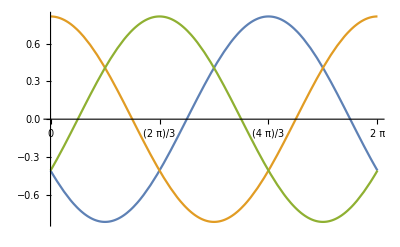

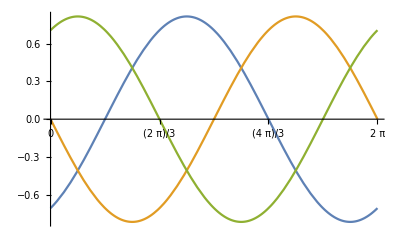

```mathematica
Plot[{-√(2/3) Sin[π/6+θ],√(2/3) Cos[θ],-√(2/3) Sin[π/6-θ]},{θ,0,2 Pi},Ticks->{PiTicks[0,2Pi],Automatic}]
Plot[{-√(2/3) Cos[π/6+θ],-√(2/3) Sin[θ],√(2/3) Cos[π/6-θ]},{θ,0,2 Pi},Ticks->{PiTicks[0,2Pi],Automatic}]
```

```mathematica
Definition["scale"]
```

scale[nYAB,YAB][θ_]:={1/(√3),1/2 √(3/2) Sec[π/6-Mod[θ-π/6,π/3]],1/2 √(3/2) Sec[π/6-Mod[θ,π/3]]}
 
scale[nYAB,rR][θ_]:={1/3,1/2 Sec[π/6-Mod[-π/6+θ,π/3]],1/2 Sec[π/6-Mod[θ,π/3]]}
 
scale[rR,fR][θ_]:=Piecewise[{{{1,-Sin[π/6+θ],-Cos[π/6+θ]}, 0≤Mod[θ,π/2]<π/6}, {{1,Cos[θ],-Sin[θ]}, π/6≤Mod[θ,π/2]<π/3}, {{1,-Sin[π/6-θ],Cos[π/6-θ]}, π/3≤Mod[θ,π/2]<π/2}, {Null, True}}]
 
scale[rR,qR][θ_,n_:8]:=Piecewise[{{{1,-(2^(2-n) Sin[π/6+θ]),-(2^(2-n) Cos[π/6+θ])}, 0≤Mod[θ,π/2]<π/6}, {{1,2^(2-n) Cos[θ],-(2^(2-n) Sin[θ])}, π/6≤Mod[θ,π/2]<π/3}, {{1,-(2^(2-n) Sin[π/6-θ]),2^(2-n) Cos[π/6-θ]}, π/3≤Mod[θ,π/2]<π/2}, {Null, True}}]
 
scale[qR,rR][θ_,n_:8]:=Piecewise[{{{1,-(2^(-2+n) Csc[π/6+θ]),-(2^(-2+n) Sec[π/6+θ])}, 0≤Mod[θ,π/2]<π/6}, {{1,2^(-2+n) Sec[θ],-(2^(-2+n) Csc[θ])}, π/6≤Mod[θ,π/2]<π/3}, {{1,-(2^(-2+n) Csc[π/6-θ]),2^(-2+n) Sec[π/6-θ]}, π/3≤Mod[θ,π/2]<π/2}, {Null, True}}]
 
scale[qR,fR][θ_,n_:8]:={1,2^(n-1),2^(n-1)}
 
scale[YAB,rR]={1/(√3),√(2/3),√(2/3)}

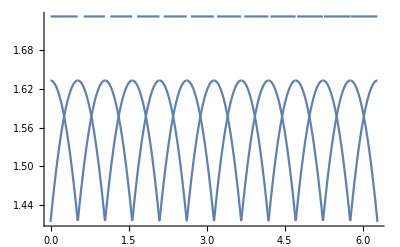

{1/(√3),1/2 √(3/2) Sec[π/6-Mod[-π/6+θ_,π/3]],1/2 √(3/2) Sec[π/6-Mod[θ_,π/3]]}

```mathematica
Plot[1/scale["nYAB","YAB"][θ],{θ,0,2 Pi}]
scale["nYAB","YAB"][θ_]
```